{0.203891,1.08936,0.70794,1.66811,1.68345,1.87913,0.0524269,1.54774,1.16051,1.96792,1.37283,0.856026,1.20816,0.455662,1.11635,0.228564,0.448638,1.25138,1.60883,0.705698,1.93453,1.42292,1.68006,0.861022,0.550963,1.74993,0.0814445,1.21519,0.623566,1.11796,1.9276,1.68528,1.09474,0.911086,0.405244,0.719087,1.79803,0.601924,1.48428,0.186346,1.82172,1.10147,0.892326,1.62491,0.264448,0.922695,1.66131,0.0132889,1.27236,0.792538,0.0698312,1.86943,1.14475,0.268638,1.32543,1.10288,1.67672,0.838955,1.56662,0.312045,0.548522,1.71008,1.18595,1.32031,0.930372,0.501426,0.975031,1.97127,0.928375,0.807759,0.000830329,0.601448,0.907426,0.390133,0.0213459,1.0582,1.60788,1.15057,0.66974,0.905891,1.18284,1.85009,1.10894,0.982336,0.754252,1.35018,0.154353,1.16277,1.68183,1.82647,1.93141,1.47107,1.08523,0.379565,1.71756,0.817716,0.428793,0.524917,1.5172,1.5081}

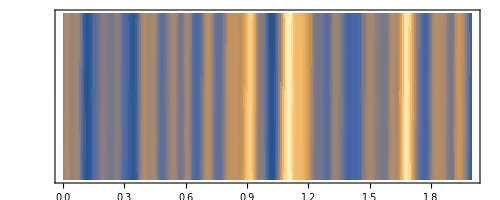

```mathematica
data=RandomReal[2,100];
data
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[data,.02],x],0}],{x,0,2},{y,0,.04},AspectRatio->Automatic,PlotPoints->{200,2},FrameTicks->{Automatic,None},PlotRangePadding->None]
```

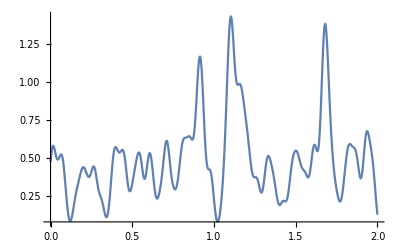

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[data,.02],x],{x,0,2}]
```

```mathematica
data3={1.3358898,0.83184433,1.4916142,1.09361713,1.34538623,0.92991561,1.31397876,0.92178127,1.20100388,1.40378328,1.21296198,1.3966429,0.74880581,1.42496749,0.80024503,1.4462353,1.21849477,0.78696235,1.44270173,0.99896451,1.41247392,0.79570853,1.287961,0.69274273,1.20148182,0.97270553,1.30956231,1.0893515,1.49817328,1.00588461,1.24544248,0.87539825,1.31282829,1.49737507,1.19919443,1.36458453,1.27711822,0.78367129,1.27299635,0.72618125,1.46459035,1.07913892,1.49262916,1.14262435,1.2632854,1.04040922,1.4527469,1.23148738,1.28995309,1.44234605,1.17095581,1.37296115,1.03346466,0.82048119,1.18151579,0.9212036,1.48498879,1.02889967,1.3892317,1.05307122,1.23859544,0.94944227,1.27892631,0.95790067,0.9552729,0.7817994,1.47615177,1.21467194,1.31592726,0.82355988,1.19003977,0.73121834,1.19317563,0.80251991,1.21193117,0.81161252,1.09481837,1.26448991,0.92272704,1.04598383,1.32450577,0.89323267,1.30332444,0.81081135,1.02314009,1.40787955,0.6222551,0.92563634,1.45140001,1.05980074,1.07621396,0.78626352,1.32341383,1.48510745,1.17724495,1.42979379,0.80897514,1.21570392,0.8467518,1.33589292,1.0745182,1.43138276,1.12847189,1.46613664,0.80556852,1.22840856,0.98363716,1.48631616,0.75503128,1.49462783,0.76661263,1.49660517,0.98856726,1.48080083,0.67828645,1.04785233,1.46394583,1.02787027,1.48412862,1.09775026,1.11934778,0.90507331,1.29876614,1.08055174,1.49053046,1.04850919,1.47721148,0.86859671,1.4312469,1.04248685,1.47230633,1.08636987,1.08273891,1.35036594,1.0809086,1.40289625,1.48058035,1.41527217,1.2104048,1.16441427,0.91849264,1.25258044,0.93935979,1.26888161,1.3230582,0.85442453,1.31560388,0.85042884,1.39697132,1.03737936,1.13392881,0.86220799,0.97328184,1.37596849,0.82618617,1.19870394,1.29477555,0.8487135,1.18079391,0.7743323,1.13918845,1.4689054,1.00330878,1.24972222,1.02958597,1.37980951,0.78981519,1.21530434,1.45782522,0.85105979,1.4484505,0.82553054,0.84815423,1.44570419,0.71838385,1.23072784,1.10165594,1.48202665,0.8529572,1.15637038,1.44419258,0.88716692,1.3701218,0.82075465,0.82330242,1.22999439,1.04525172,1.38365008,1.4842276,1.12703713,1.26158669,0.89571894,1.45786773,0.82684784,1.46330427,0.81665652,1.32411573,0.82070517,1.2072504,0.72039788,1.35549427,0.77266684,1.45754815,0.84271172,0.89051775,1.24868477,1.18259796,1.47734883,0.78090858,1.47802147,0.65297858,1.31210413,1.3508105,1.28092213,1.44232521,1.38898346,1.36716148,0.84376319,1.40321691,0.98851139,0.82467677,1.30193222,0.79338212,1.43927095,0.88925916,1.19687158,1.07385665,1.45079087,1.46677397,0.99757336,1.23268503,0.83584088,1.29184888,1.14718133,1.16816994,1.00161929,0.99499631,1.28869245,0.9176221,1.27115302,0.80108908,1.22886232,0.86568509,1.38495912,1.47879392,0.94370192,1.21934602,0.81610346,1.00430848,0.6705309,1.31112755,0.90157299,1.42017213,0.72126584,1.47938869,0.93172111,1.49802584,0.81694901,1.37462546,0.88128592,1.29061494,1.48716669,0.8284078,1.01835522,1.38493424,0.69911948,1.36089957,0.68484769,1.45804773,1.18236256,1.36700494,1.06114344,0.90385264,1.39694517,0.90169019,1.30846099,1.10829777,1.42922792,0.90242923,1.36531505,1.15396225,1.47757045,1.13268335,1.43746025,1.43473499,0.84819389,1.20984351,0.72861024,0.85207913,1.46001973,0.80279667,1.47411289,0.85235943,1.40551257,0.86419718,1.32975879,0.97504391,1.14857323,1.13123966,1.35608982,1.23429906,1.43616452,0.9582553,1.15254306,1.35718214,0.94368248,1.28611505,0.90615243,1.17125263,1.41549393,0.93658208,1.26722385,1.29913726,1.10298348,1.22691129,1.00738472,1.34467514,0.9733445,1.18805713,0.91768668,1.06475834,1.45917789,0.96177569,1.35544887,1.31988558,1.4802646,1.1351595,1.3423735,0.80485112,1.31534075,0.96530738,1.44498748,1.49482491,1.35399663,1.47485183,1.36259011,0.63646525,1.29951391,0.68085619,1.43500392,1.41201628,1.07369142,1.2313474,0.93999603,0.87560605,1.22245772,0.98688153,1.42358542,0.59449781,1.23224874,0.69099836,1.49059739,0.80056904,1.45107205,0.86708292,1.42679513,1.24560855,0.94633553,1.37733291,1.07597699,1.48188889,1.25823406,1.16184288,0.94559113,1.41137135,0.88786528,1.32182902,0.77922914,0.947757,1.42362085,0.82807037,1.34336317,0.91160981,1.49645086,0.97586062,1.48386728,0.82371183,1.36143551,0.90668563,1.48026071,1.38605752,0.70783374,1.43654441,0.76761104,1.45762654,0.94847145,1.39813054,1.01001958,1.44769344,0.84912736,1.13063693,0.67206467,0.62514722,1.09070866,0.86347098,1.42042598,0.91084716,1.47295528,0.84756332,1.46713325,1.4465103,0.76024033,1.36096548,0.83010899,1.40431791,1.19329848,0.99841677,0.81004097,1.41110083,0.90249274,1.44009012,1.00625438,1.19660779,0.83368139,1.47300294,1.09602679,1.39569028,1.14406321,1.38208907,1.10840711,1.38786373,1.02887521,1.15604897,0.8420156,0.98279831,1.11467668,1.09845324,1.23306198,0.95147801,1.49539493,0.75335702,1.34836766,0.96549402,1.49309223,0.88110859,1.40016058,0.67868745,1.05576808,0.9002084,1.3366578,1.04626472,1.22709188,1.04093079,1.23916546,1.15152895,1.48138575,1.03236201,1.41841867,0.87146336,1.14564792,1.12037314,1.45552591,0.80600353,1.20923464,0.96613451,1.31707926,1.41266405,1.38871976,1.27915114,1.24096336,1.43342125,0.68512533,1.39686082,0.69085529,0.71474996,1.22697423,0.88346186,1.4953661,0.94487129,1.4389781,1.06998805,1.47770174,1.42784519,0.79869576,1.14084526,0.56597074,1.07465349,1.28322354,1.28508351,1.48334647,1.47025005,1.04717509,1.2138532,0.74970002,1.17539064,1.45717915,1.10769201,1.42519869,1.09722992,1.47033929,0.95166907,1.37767379,1.21432516,1.31344475,1.21280144,1.3160815,1.20828013,1.40170574,1.20934641,1.41476164,1.43461037,1.32834411,1.02346048,0.94949092,1.34589938,0.7048691,1.35730874,0.73570262,0.94257371,1.37852428,1.04007817,1.44156537,1.39702506,0.76287261,1.41671773,0.8346077,1.18218113,0.92439921,1.49693746,1.23178864,1.40516669,0.98108636,1.48500622,1.03156544,1.07634582,1.24704448,1.25389257,1.44529992,0.68645225,0.93227356,1.10348634,1.44787798,1.2048304,1.06248982,1.34017074,1.18715947,0.8846612,1.48262989,0.70771529,1.45964492,1.20188716,1.49936255,1.05518397,1.33049339,0.78425542,1.29838169,0.94608172,1.39492513,1.08452483,1.41416094,0.64572211,0.87693654,1.19196357,1.32130479,1.15778797,1.25239662,0.80151557,1.13726641,0.94143278,1.32084671,0.84030769,1.42557601,0.7358174,1.43707948,1.42485438,1.24815251,1.38667217,1.08480209,0.79225487,1.22613127,0.94196791,1.43349557,1.06190402,1.37772884,1.16083769,1.42779654,0.97014529,1.31930394,0.98453907,1.42565929,0.78367981,1.35066774,0.89865717,1.36215322,0.91345714,1.28923357,0.90315516,1.41584359,0.69328624,1.07904826,0.83264461,1.2426827,0.70738086,1.35659422,0.69689047,1.27279412,1.45858705,1.10691362,0.96332582,0.64517015,0.92242594,1.46538595,0.9373137,1.42458825,1.45113084,1.21887224,1.1681716,0.93458938,1.45553531,1.30556767,0.79791314,0.7149089,1.39244461,0.64797932,1.28948634,0.58803711,1.33560666,0.9802911,1.25418,0.84141507,0.8398078,1.40256115,0.7567416,1.4216058,0.77947693,1.4281518,0.84361384,1.36036627,1.04429911,1.25941711,1.21473806,1.44033628,0.84889729,1.26665619,0.71486203,1.10432816,1.22204683,0.67398887,1.46156181,0.9089036,1.48764827,0.89356354,1.38084136,0.75048388,0.79965127,1.47841509,0.63923201,1.23023775,0.98504019,1.27311707,0.94651376,1.27978159,1.2868096,0.81309896,1.27174632,0.81403619,0.98975857,1.48557974,0.80451996,1.2874049,1.29651516,0.8595319,1.08235756,0.73008705,1.03699351,1.45154172,0.95998418,1.29917348,0.94247368,1.37691479,0.69991551,1.11848047,1.42075284,1.16740822,1.46254696,1.17860065,1.24511288,1.49009967,1.01185631,1.28503297,1.38993172,0.98833561,1.28890306,0.81439695,0.73891091,1.0559289,0.97430025,1.37494151,1.37185695,0.70987222,1.18683339,0.5743659,0.93110981,1.25972226,1.14810788,1.49622022,1.48114623,0.98330629,1.39482357,0.90007195,1.2197449,1.49453521,1.00493534,1.42471491,1.29771307,1.03280879,1.0834922,0.83184264,0.86121291,1.41284889,0.85033127,1.43836231,0.81253073,1.48881192,0.66582419,1.33661217,1.2925741,0.84904363,1.45211033,1.00518316,1.45280113,1.38270259,0.97618418,0.92631582,0.68438749,1.48975242,0.66437285,1.40416468,1.14607257,0.89540334,1.44551813,1.13636956,1.13257299,0.63752543,1.42006074,0.83489525,1.20162874,0.98513875,1.46300025,1.24733395,1.48710441,0.90959183,1.49291392,0.96729214,0.9800036,1.38811907,1.05477741,1.38003381,1.41391985,0.77810878,1.4617718,0.87714558,1.42271753,1.09521342,1.49316604,1.12632783,0.7433308,1.42915177,0.66833287,1.3494157,1.10058456,1.44960995,0.99798992,1.21504067,0.85960901,1.2671252,0.96677026,1.39672288,0.96013391,1.44909709,0.82224602,1.25558333,1.45931646,0.8812245,1.371276,0.83723713,0.78217106,1.46557363,0.62687392,1.23986743,0.60671105,1.3248227,0.67705881,1.42311131,1.44594501,0.92563749,1.489691,1.04756078,0.98814954,1.27482341,0.70515085,0.92345951,0.88663882,1.20027496,1.01692796,1.41099822,1.13116485,1.32818772,1.14312414,1.40802526,1.41002073,0.91253697,1.22729159,0.7183128,1.05097578,1.40395446,1.12049735,1.47943005,1.25408254,1.49296706,1.11048965,1.45045395,1.1776955,1.32341833,1.26462606,1.44862492,1.35613225,0.83685502,1.33485325,0.87000185,1.15883217,1.47094819,1.15537796,1.32773236,1.14403503,0.87343287,1.13177182,0.86068823,1.26836021,0.72821607,1.45596704,0.79688345,1.33860536,1.47070957,0.96180565,1.03871871,0.847076,1.12194086,1.12099793,1.37994325,1.10447847,0.74823327,1.38849766,0.97787652,0.80625009,1.26205566,0.90780658,1.47289899,1.33534348,1.05738329,1.47824275,1.21948372,0.65034308,0.89369053,1.10893069,1.47134043,0.89983382,1.36532722,1.03758237,1.48482209,1.29680122,0.80703883,1.4083882,0.90005951,1.20463997,1.43196673,1.25656817,1.40997119,0.59655341,1.27550633,0.68993218,1.43348075,0.78010298,1.35047771,0.8079494,1.4422088,0.97062871,1.34626591,0.94590189,1.22546682,1.45706985,0.92435072,1.39705202,0.80834224,0.61280188,1.36638223,0.62210719,1.34323202,0.54213467,0.87385897,0.9765253,1.45971156,1.10685044,1.44509843,1.13194289,1.44444008,0.80475309,1.49206248,0.77911785,1.49304424,0.885744,1.44555103,0.6708688,1.18965328,0.98646509,1.28107347,1.06288372,1.49248415,1.23306586,0.63798029,1.46583367,0.78383158,1.17150102,1.01168568,1.40435571,1.21111579,1.38462238,1.14146308,1.29853484,1.07338976,1.42369547,1.08826368,1.43296622,1.15541663,1.48940122,0.676714,1.34140686,0.68120457,0.82180125,1.49657653,0.79837383,1.44396629,0.80585034,1.44033066,0.7591527,1.39298245,1.15903793,0.74460006,1.35842132,0.92786231,1.25305976,0.90771874,1.13334484,0.81045752,0.98398908,0.58871175,1.47909091,0.96934908,1.04489679,0.6824323,1.40126591,0.98870078,1.48781935,0.73790488,1.21613233,0.59049695,1.30437345,0.9324453,1.24758014,0.86742941,1.45975001,1.41093113,1.00506527,0.96410131,1.28482276,0.98151059,1.49476409,1.087596,1.23839389,0.84028471,1.26948621,0.91943338,0.8327361,1.33717517,0.94544317,1.46393385,1.42237795,0.96154647,1.34120227,0.94486359,1.11680508,0.95376943,1.49242378,1.31239757,1.26538387,0.84721939,1.34152397,0.85068984,1.47655665,1.00337158,1.49683235,0.86873462,1.0592189,1.35776668,1.12061191,1.43540327,1.40854597,1.15563126,1.4330008,1.16005161,1.47168782,1.09499065,1.23505576,0.92405273,0.99562805,1.41824361,1.03592333,1.49949969,1.25665209,0.56759659,1.42369897,0.66847953,1.45635097,0.76696773,1.4462515,0.85444741,1.10848881,1.41350571,1.07419097,1.42345449,0.85974007,1.41627645,0.77406987,1.33029324,1.1759546,1.0475786,1.48692837,1.26572858,1.16973826,0.7928216,1.33909152,0.9692795,1.42968132,1.2953788,1.38926516,1.29236326,0.58617121,0.92773569,0.99164266,1.45608551,1.27623477,0.87929061,1.11570436,0.75656194,1.40899949,1.27562221,1.32736903,1.20916927,1.01831074,1.24571608,1.26125172,1.4734221,0.95072491,1.18921368,1.24683941,1.45685266,1.43044097,0.68413977,1.33614675,0.60016177,1.3374396,0.88063671,1.41524707,0.83391212,0.95568275,1.23692003,1.13211238,1.37338031,1.42624398,0.90858473,1.37961363,0.82202894,1.13031691,0.70942045,1.35739436,0.95533817,1.01165023,1.41447543,0.8539258,1.40777866,1.48548978,0.91844267,1.38481784,0.92384446,0.91879726,1.32365397,1.03568597,1.3629838,1.42392097,1.10014489,1.23664551,0.92041314,1.35036295,0.80193799,1.40688985,0.90151734,1.45397639,1.00812347,1.37721756,0.97454683,1.25398191,1.02528002,1.48652994,1.15116272,1.28687037,0.78153566,1.33083447,0.86090771,0.69349409,0.90842328,1.14789096,1.44298391,0.75911592,1.00270203,0.96044567,1.23536624,1.27277482,0.93447274,1.32441729,0.96124377,1.22429496,1.46445674,1.05573072,1.24234416,1.32474563,0.54620828,1.49619641,0.62310624,1.11154057,1.49426281,0.83716752,1.13668781,1.47694105,0.70263759,1.48452151,0.70978973,1.41045848,1.19386003,1.29130718,0.98932271,1.3351368,1.10421254,1.30307174,1.02542384,0.68825436,1.35423009,0.75053344,1.35646976,1.49011562,0.88352201,1.24852126,0.72464778,1.23649539,0.83540376,1.17851401,0.83106023,0.87607367,1.32114983,0.72981003,1.15118452,1.38913144,1.18160387,1.33905682,1.06165776,1.4612714,0.72630239,1.445985,0.72618919,1.32680982,0.94311059,0.96987742,0.66974026,1.47097375,0.96773889,1.43909517,0.97513314,1.49547837,0.77326834,1.36457151,0.75549114,0.88583085,1.41743016,0.90972157,1.3979671,0.99494072,1.38962927,0.84572524,1.19741735,1.0344452,0.76787273,1.38407347,1.02022474,0.93660335,0.80630742,1.48175985,1.28618589,1.44499152,0.97522938,1.49333284,1.1946734,0.80953459,1.12974285,0.83730634,1.14894045,1.26090403,1.40096877,1.24268913,1.47580149,0.91963866,1.36171295,1.12335414,1.47354812,1.22056244,1.45553437,0.93634306,1.22070393,0.87522669,1.17645476,1.01991375,1.28450089,1.19571935,1.48065261,0.94824342,1.23675299,1.13240463,1.23976302,1.00403003,1.08781121,1.36801855,1.21786196,1.33281822,1.17695471,1.42049345,1.0299491,1.35356161,1.00069413,0.89804959,0.5862468,1.44098592,0.98850776,1.43345115,0.95419772,1.4464935,0.87035796,1.23433163,0.83021276,1.36680393,0.92596377,1.16028147,1.08012026,1.30748849,1.22152264,0.90723904,1.24008689,1.02676552,1.33355012,1.01867667,1.09212442,1.287967,1.36361384,0.69036161,1.36087991,0.70785778,1.40494954,1.00184669,1.34061547,0.99030393,1.23568112,1.25352379,0.83357084,1.43855769,1.02891266,1.33934673,0.94225917,1.37207383,0.93604665,1.42263826,1.23824691,1.21018619,1.0512258,1.46538964,1.20615448,1.2365665,0.9668986,1.06973446,1.49637226,0.7290735,1.08738495,1.41007696,0.91863775,1.46940926,1.05486461,1.41541901,1.11633643,1.09283727,0.87880181,1.02386078,1.23521131,0.99857335,1.19411067,1.43094047,1.14338826,0.97929814,0.72113118,0.76028079,1.47603823,0.69241524,1.45730259,1.46481493,1.12578016,0.98369558,0.74073032,1.08266025,1.40825323,1.11853976,1.40582885,1.45957251,1.14527218,1.39498977,0.97230993,1.27413286,0.71186902,1.46314806,0.82919042,0.84543219,1.05689964,1.1249818,1.36013018,1.20633237,0.87504964,1.08122108,0.78215155,1.15279119,1.44175752,1.09746471,1.40579165,0.96757254,1.48540633,0.78803393,1.1711097,1.47550008,1.33250907,1.00046549,0.86602549,1.41187279,1.09891199,1.45418022,1.09169155,1.43705304,0.91430663,1.24214729,0.88855765,1.4421259,0.86763464,1.32973419,0.69589892,1.07586636,1.49304697,0.95090873,1.33436526,0.92209666,1.23316111,1.10570279,1.47302611,0.84323075,1.25572572,0.90433647,1.30754668,1.28938297,0.93709817,1.45094277,0.9836773,0.76471012,1.24615181,1.03699242,1.48685541,0.76190085,0.91099846,1.24123789,1.46136439,0.69420854,1.37057598,0.61198822,1.23341323,1.49346684,0.9703863,1.40581852,0.83865748,1.33170529,0.79676699,1.42276396,0.85488981,0.89074052,1.18827869,1.09017268,1.46249367,1.44060858,1.15877662,1.35688196,1.08214175,0.67473754,1.12563511,0.92745784,1.41242654,0.91059998,1.37777921,0.88928256,1.29586372,1.09977277,0.71070805,1.48106523,0.94900632,0.92363404,1.45999228,0.77952113,1.1260824,0.93596308,1.45878112,0.80259597,1.47034453,1.09639502,1.21162832,1.26803971,1.40020218,0.77137003,1.43364958,0.7771974,1.27410344,1.48769969,0.71517739,1.44838137,0.72170861,0.72730711,1.37946571,0.7814,1.38671954,0.88866698,1.20483349,1.13358491,1.48313273,1.4175445,0.79565934,1.36470281,0.86105079,1.00216471,1.22023287,1.13519405,1.48870648,1.46928295,0.8921914,1.29876484,0.67707229,1.48999274,1.22861963,1.16498101,0.99312381,1.26196737,0.63687409,1.30961847,0.65514264,0.84192281,1.24546549,0.90786227,1.32046377,1.16589476,1.43121178,1.03040033,1.32190434,1.34681917,0.84362822,1.22807488,0.72737146,1.30993568,0.68549762,1.41436754,0.68763537,1.09614942,0.71499723,1.48414193,0.96598761,1.23590004,0.81765818,1.34872883,0.893287,1.38089242,0.79676307,1.32432271,0.81867418,1.39903982,0.74292536,1.42818765,0.75616402,1.02261966,1.20123731,1.18988709,1.39371618,1.43779989,1.25402416,1.49359,1.35096207,1.47670734,0.87488178,1.30180544,0.82116858,1.18083853,0.82688569,1.30382127,0.96285991,1.0096368,0.7199796,1.48944779,1.10788438,1.01395776,1.26760141,1.04964437,1.22545577,1.21355838,0.67948035,1.28839722,0.73607893,0.91672009,1.28812531,0.96452199,1.41468716,0.83228519,1.38305748,0.73972281,1.35141466,1.41635041,1.0568346,1.4223726,0.93945963,1.05270414,1.32475311,0.85974728,1.20391853,1.16515467,1.34265691,1.21388049,1.41336144,1.08465075,1.37567834,0.90127255,1.25937991,0.74979014,1.27628389,0.92519056,1.4823487,1.45879038,1.06380202,1.29874062,0.91085557,1.48385018,1.01629983,1.1211121,0.76993469,1.14072019,1.24694089,1.25315514,1.39434869,1.40577178,0.90980749,1.33730555,0.90359731,1.01076845,1.47886578,0.90116548,1.43117101,1.43998934,0.94738912,1.32067575,0.79609024,1.3570899,1.05823611,1.34144513,1.04949633,1.37225689,0.95931145,1.34870539,0.89212526,1.08147543,1.44297554,1.06184762,1.44119695,1.04205738,0.79200745,1.42941622,1.04752807,0.80772489,1.25526696,1.04194108,1.44147781,1.18590639,1.46086514,0.74425591,0.9067805,0.93989562,1.4600651,0.94065162,1.33035832,1.38247083,1.08799258,1.17910035,0.91670421,0.65927112,1.47769927,0.62884249,1.41695641,0.8947222,1.37991502,0.92646555,1.38201077,0.89021031,1.19329942,0.99020764,1.41928047,1.42073126,1.157857,1.24128691,1.05395814,1.3107289,1.45684902,0.9306617,1.01464378,0.8707722,1.44878187,0.73018957,1.42437722,1.45902681,0.95571355,1.33347823,0.80989696,0.92524842,1.42342124,0.9232802,1.31369019,1.47356637,0.83170145,1.40553076,0.89793977,1.26896022,0.84988518,1.27097109,0.85229128,0.97762682,1.40112199,0.70495999,1.03722353,1.28852872,0.76814133,1.34193578,0.81225652,1.21796174,1.47597667,1.02735052,1.40217813,1.42379228,0.99530467,1.41246012,0.92605252,0.91878838,1.27029794,0.6621119,0.97546985,1.28108986,1.42341882,1.14927819,1.32618096,1.41740897,1.20560409,1.37747176,1.10972676,1.08265018,1.43269429,1.00141655,1.35344022,1.39433723,0.7836881,1.46550797,0.82875728,1.36748384,1.15375801,1.02922572,0.84632835,1.3128916,0.89132851,1.17674089,0.78017944,0.65263868,1.38960971,0.6599876,1.45208219,1.3853657,0.79911702,1.4459044,0.91804015,0.6995598,1.32438971,0.79786756,1.45757722,0.80675841,1.48064375,0.63459089,1.25576091,1.28070846,0.94153165,1.47376517,1.01679342,1.21295084,0.90964994,1.24870957,0.95489811,1.36027177,1.018742,1.25366575,0.8655185,1.45430751,1.16762328,1.49162649,1.19888092,1.36806942,0.90025302,1.2267857,0.71837318,1.40146089,1.00163191,1.21003649,0.92791425,1.43378282,1.13793813,1.01651347,0.78429189,1.21623408,1.00397846,1.44180342,1.24029999,1.24485031,1.47846354,0.95473658,1.12221851,0.68884813,1.4476932,0.76618803,1.46858897,1.30218213,0.79809727,1.43657233,0.79967861,1.07763708,1.37796861,1.12899161,1.48684774,0.94949,1.48099844,0.81629386,1.29178256,1.35491941,1.0198549,1.22542679,0.88164545,1.49336289,0.97131163,1.20052561,0.8364606,0.81309829,1.33884213,1.04378043,1.49492938,1.36304211,0.86082215,1.26903217,0.72525926,0.98272352,1.41486299,1.06733629,1.40429727,1.36640246,0.77162974,1.47024578,0.97384717,1.48264869,1.12236806,1.41150926,1.03821183,0.93446245,1.44638643,0.83343076,1.45750492,0.87617093,1.17960534,0.99392749,1.2504442,1.34734738,0.92386034,1.35840636,1.02763679,1.02030913,1.43779697,0.63529578,0.94449635,0.94738552,1.26766117,1.10436837,1.45513994,1.18417835,1.49660494,0.96994749,1.38962564,1.09424991,0.84980229,1.20022727,0.92339598,1.25166892,1.42362464,1.06832398,1.3155198,1.33767587,1.08257068,1.435023,1.17489506,0.9118147,1.4003485,0.69860724,1.16812592,1.23836826,0.76191195,1.08409166,0.65749284,0.96637491,1.06963378,0.9257983,1.02991122,1.16748325,1.42566417,1.07361772,1.40906791,1.45022747,1.12759826,1.10920625,0.82034864,1.37193539,1.137213,1.45021839,1.17575588,1.15117963,1.33181603,1.10353345,1.38947312,1.28202874,1.05126234,1.33226772,1.06731874,1.0293573,1.28462299,1.23232605,1.4969034,0.84096641,1.09280022,1.1034248,1.41013192,1.4531948,1.19231587,0.93345145,0.69264457,0.94816971,1.43017687,0.7541996,1.40692159,1.24142371,0.91679091,1.48883989,1.03640005,0.56709398,1.17460566,0.74719612,1.44816044,1.43294162,0.632563,1.37357263,0.57879807,0.86733116,1.46151706,1.0098387,1.48353845,1.49298577,0.69092314,1.34409209,0.588381,0.94770175,1.41626297,0.88836016,1.4705848,1.04977237,1.33473375,1.074399,1.31209024,1.1800864,0.88738038,1.06364485,0.80919508,1.46938304,1.33149977,1.29002181,1.16680719,1.44714836,0.92617569,1.23236305,0.81599665,1.26007184,1.06973812,1.37916415,1.09689577,1.44618529,1.10210936,1.47916165,1.14062444,0.69473071,1.08775538,0.89411145,1.31385403,1.4992406,1.05648825,1.38738066,0.88502546,1.2820772,1.48494445,1.17092759,1.29737895,1.41625077,0.68522582,1.42575436,0.79435772,1.12092018,1.46356242,0.98100408,1.36820273,1.42083847,1.32051552,1.21415552,1.11681221,1.44382308,1.16597059,1.28716439,1.00528144,1.48855236,1.1651008,1.3577175,0.94625308,1.42160516,1.09448099,1.12473148,0.75775511,0.99692355,1.38365788,1.01672773,1.43931729,1.46415485,0.84100993,1.45090687,0.77517278,1.48285039,0.84249131,1.34965211,0.75231812,1.42806837,0.80123621,1.41024314,0.79754468,1.14182814,1.36501854,0.89553739,1.12672642,0.89815601,1.41346501,0.76650669,1.17789936,0.73590653,1.41139906,0.71525753,1.43693968,0.58484325,1.14194551,0.74570025,1.42034644,0.65823458,1.38210162,0.72519785,1.45629543,1.49713162,1.26307332,1.32328237,1.07945551,0.87162735,1.27477156,0.95934305,1.31476751,0.80088252,1.06844809,1.03335241,1.36597106,1.31371504,0.83075826,1.13983108,0.70023716,1.13814054,0.80671512,1.46335638,1.07374848,1.02970607,1.48357943,1.02748386,1.49923986,1.47292437,1.13239631,1.08750136,0.83055911,0.82739058,1.30615363,0.97694768,1.37436691,1.46122827,1.13309035,0.99040384,0.69230576,1.12954049,0.80305876,1.41134688,1.11814319,1.48122139,0.89584182,1.39064421,0.84550749,1.42995922,1.16285298,1.48729285,1.18963082,1.45343343,1.2982615,1.48134553,1.23774545,0.6561831,1.48229223,0.81202624,1.49488401,1.15906779,0.7065907,1.26508843,0.78502516,1.40159724,0.94980773,1.38834949,0.92870829,1.49068886,0.96857045,1.43320608,0.96288473,1.18704362,1.45337656,0.98366144,1.19387958,0.97201452,1.24099838,1.0670936,1.38314637,0.99419185,1.42896865,0.92892417,1.34402339,1.30438603,0.60207122,1.46840836,0.7363128,1.46062899,1.11367947,1.35501523,1.03959845,1.18746661,0.79125736,1.14653549,0.76953852,0.84437472,1.30405349,0.78929983,1.29976664,1.3845809,1.24619334,1.0776452,0.90108794,0.63253143,0.74336832,1.27062716,1.43881051,0.65636889,1.34005804,0.70567608,1.43481474,1.44384813,1.15463282,1.27593454,0.99858716,0.73383686,1.2358158,0.79330015,1.33315152,1.4364939,1.19525689,1.07827463,0.91493883,1.35217202,1.13813827,1.28448549,1.03074539,1.38436037,0.85749126,1.24673245,0.69833072,0.84358289,1.31367909,0.68817612,1.17906788,0.70813472,1.43847207,0.75755358,1.36939227,1.22988488,0.64508091,1.44985394,0.77895082,1.0935463,1.48947592,0.57009158,0.86323477,1.06609662,1.44850032,0.83782648,1.12199416,1.13813066,1.4739922,1.00140575,1.49053495,1.47105642,1.07442344,1.23728426,0.76740185,1.18965409,0.70129009,1.49424916,0.85808157,1.4360795,0.97241799,1.45112126,1.1268799,0.83990184,1.45546893,0.79029244,1.37016337,1.11161701,0.66945529,1.42159257,0.95730459,1.12929698,1.41935942,1.00597724,1.47407639,1.29199674,1.47756716,0.80237276,0.98226533,1.47965844,0.90582551,1.29223519,0.91430538,1.35386277,0.90732219,1.43455739,0.88879396,1.4309389,1.12577306,1.38504305,1.04734581,1.16165234,0.95733669,1.21833181,1.02921959,0.75230559,1.39253214,0.73401546,1.35786325,1.466204,1.26505084,1.49900491,1.22897822,1.48488007,0.97603804,1.12492803,0.68262226,0.80829833,1.39404434,0.76307558,1.35254241,1.44446631,1.10287959,1.29255706,1.05814175,1.26601829,0.83604615,1.06845144,0.67714122,1.45173864,1.49858905,1.41880498,1.46373387,0.77132721,1.22361893,0.88369117,1.30307448,1.42422414,1.02137507,1.26257308,0.75030825,0.71881831,1.13517043,0.90941389,1.3969616,1.30505178,0.80647049,1.31324486,0.90020986,0.73489151,1.36915105,0.85654146,1.40150276,1.04317626,1.35104658,1.03165862,1.28171192,1.20111454,0.86783522,1.28074963,0.97758386,1.28322334,1.44267182,1.19488516,1.34659865,0.81394736,1.37977982,0.8600216,1.46628063,1.15428285,0.71188383,1.40316787,0.84933279,1.13657265,1.3216409,1.24781102,1.43955891,0.89518466,1.44784363,0.80193113,1.31715065,0.85901025,1.46798647,0.75461626,1.45087967,0.77452386,0.85154587,1.35531871,1.49644109,1.02138628,1.43162411,0.91638729,1.28248318,1.29457195,0.9255847,1.33756349,0.95248286,1.45170539,1.11551065,1.30174101,0.98580989,0.72519573,0.89414117,1.21226864,1.40696714,0.75608095,1.25554317,0.92394773,1.43218126,0.87545965,1.45555418,0.7950787,1.20438521,1.34245965,0.91737049,1.47689088,1.16627104,0.77947641,1.4699212,0.7368656,1.47506549,1.05927304,1.45967495,0.94048928,1.32167833,1.4558831,0.84314381,1.49780479,0.8860711,1.30668026,0.8792558,1.47410848,1.03158407,1.44156465,1.30835807,1.25646559,1.12967438,1.42321752,0.85563485,1.39123565,0.76038118,0.99068596,1.2313943,1.2494394,1.48203201,0.92550286,1.10258159,0.94673949,1.10639285,1.30238801,0.95153112,1.38349759,0.95523521,0.79756796,1.22573297,1.0455396,1.42976745,1.33722038,0.94207342,1.49572972,1.16700827,0.94622325,1.42715676,0.85919824,1.31221519,0.72349021,1.28850694,0.86461457,1.48757627,0.78471782,1.37340796,0.76922483,1.32882348,1.26035494,1.45624962,0.92483294,1.15004003,0.71612757,1.38787166,0.72974141,1.47237494,0.79240537,1.05972919,1.08812989,1.49875043,1.2661275,1.02954258,1.23023998,1.01237064,0.76474941,0.94347188,1.08935177,1.33548425,1.48395675,1.23509179,1.37871845,1.17881902,0.83342332,1.4483606,0.7716041,1.30652457,1.46078468,1.28513396,1.43609206,1.25891119,0.76598587,1.2625185,0.85568844,1.40466337,0.86493573,1.46825886,0.72308349,1.27053019,1.47652824,0.84529212,1.30594364,0.72804032,0.84625473,1.30543124,0.88719705,1.23706348,1.41083955,1.23570622,1.37442634,1.12211209,0.61367493,1.27640669,0.66277817,1.35487198,0.98647137,1.30878434,0.81649325,1.14823377,1.22783052,1.00145373,1.44032729,1.10644904,0.91753629,1.49759589,0.83086264,1.4651243,1.39134691,1.08553976,0.84627795,0.63353313,1.35431778,0.85590201,1.3559979,0.80131691,0.74502688,0.99706192,0.93861779,1.20936511,0.81757786,1.487892,0.60824851,1.32557235,1.22823256,1.02904456,0.99120292,0.8441988,1.33770909,1.09437657,0.98107346,0.78973447,1.33337589,0.94108506,1.44296061,0.925036,1.18264791,1.44622838,0.96497564,1.17951886,0.79961078,1.0868412,1.02893942,1.3482593,1.09516846,0.77558181,1.43560623,1.0978822,0.86091148,1.08873484,1.12976044,1.41087851,1.44309163,0.82900447,1.38992659,0.64842788,0.79752069,1.35554518,0.86723684,1.47755901,1.38064218,1.27238236,1.25477849,1.12586165,0.94911707,1.47898613,0.82378151,1.41189714,1.39361893,1.00827876,1.37432464,1.01211971,1.00294689,1.43623181,1.03934482,1.48928667,1.13804886,1.44583353,1.16390401,1.48976312,0.973297,1.28105043,0.95107377,1.30180129,1.38098014,1.1191866,1.47748214,1.15975379,1.23604284,1.39432624,1.30959928,1.48712075,0.79455511,1.40956129,0.64397073,1.12203462,1.19806072,0.86873015,1.30296509,0.94090976,1.30422799,0.74721882,1.46598735,0.83541648,0.83979304,1.08741035,0.94283813,1.24673563,1.15377661,1.48865034,0.95948774,1.21974683,1.45686315,0.85780151,1.29298893,0.854602,0.91428719,1.2120731,1.01178045,1.46692293,1.3936652,0.74795957,1.40178551,0.74146975,0.88224026,1.19817868,1.14046801,1.4590456,0.93978885,1.49037846,0.84561471,1.42174472,1.31855456,0.81606722,1.41119737,0.9634122,1.47825646,0.98591339,1.22735115,0.89077477,0.95265228,1.48166013,0.85976125,1.39198495,0.73830916,1.00523741,1.12255016,1.43785092,1.45710102,1.12116113,1.48640914,1.15733194,0.95378428,1.07885594,1.28574696,1.44193004,1.39872753,0.84032982,1.28982789,0.72342563,1.18739618,1.49852794,1.03905203,1.41154227,0.90851371,1.27582279,0.91281978,1.27654663,0.79602188,1.3825549,0.75135878,1.30350705,1.04696676,1.45338281,1.06261933,1.4549969,0.73422887,1.19700632,0.72403484,1.17858262,1.43824419,1.29846497,1.48517106,1.21724039,1.07846679,0.88167326,1.14959777,0.93379269,1.34463083,1.04522485,1.46005923,1.16371935,1.13941081,1.49751702,1.09895547,1.44215906,0.92633043,1.35235715,0.8967806,1.31231574,1.05290152,1.34131222,1.21858369,1.43405247,0.8635693,1.100905,1.17616502,1.41499593,1.24043136,1.48128695,0.92431612,1.15082529,0.92041095,1.3784791,1.11044113,1.4483136,0.77971869,1.00230176,1.14391375,1.45976002,1.44592332,0.78974325,1.25553331,0.67728565,1.12523717,0.62961193,1.41894081,0.85371183,1.39428756,0.9231433,1.46452176,1.11797471,1.1077217,1.24644574,1.39369139,1.49652045,0.78300183,1.12914302,0.90164397,1.25222355,1.22897666,0.79858331,1.22953599,0.78395233,1.02632103,1.45529307,0.9129056,1.22603118,1.49656941,1.30130719,1.36079982,1.20788348,1.0771458,1.48070369,0.92755466,1.48041277,1.39709633,1.14586957,1.41255565,1.20039542,1.18898992,0.92560621,1.29449059,1.00697878,0.88172587,1.34321618,1.02934582,1.44448345,0.92731021,1.1638771,1.03099539,1.22415886,1.45544729,0.86444227,1.4106469,1.02804681,1.1948253,0.9004011,1.33750348,1.01320798,1.1612246,1.49110517,0.71123729,0.92225032,1.2231083,1.39220512,0.82046575,0.92174948,1.41489741,0.76887562,1.46287637,0.84234728,1.01235644,1.33856725,0.65334201,0.89237138,0.78326243,1.27257502,0.84763477,1.39640569,1.38119125,0.96997701,1.33833349,0.95562028,1.21038232,0.92169652,1.46317574,1.02106065,0.95897394,1.31761159,1.09809702,1.44855433,0.66309782,1.17274402,0.78215591,1.36934952,1.39701878,0.83215314,1.47928584,0.81242505,1.44999519,0.80054204,1.44251278,0.77361904,1.23583263,1.01551471,1.1557665,0.95038626,1.45381268,1.19484721,1.45526329,1.16006236,1.09556939,0.69331084,1.28800738,0.83382554,1.42119298,1.16472257,1.41734569,1.15343564,1.28392977,1.03379983,1.44239072,1.16660997,1.15944833,1.45419818,0.93714744,1.22085308,0.82187512,1.31453979,1.00440681,1.48484747,1.33328606,0.86820591,1.40310971,0.88790886,0.97725449,0.72198614,1.47401295,1.14845331,0.91462893,1.49860909,0.73386039,1.29915672,1.16744565,0.67342517,1.36412981,0.81386926,1.24521691,1.38642556,0.99196187,1.14250693,1.12861396,1.40223209,1.19774793,1.48131084,1.04242779,1.14061234,1.05880691,1.16121963,0.76829359,1.12047967,0.89604092,1.26001584,1.09436188,1.4311356,0.86637842,1.13195356,1.4923818,0.90611167,1.14761991,0.6772916,1.29286944,0.95056227,1.36719842,0.92640151,1.48608623,1.06966264,1.4437834,1.02833167,1.13188012,1.33218424,1.24343889,1.48798583,1.46878777,1.2313309,1.46568178,1.21505831,1.23616032,1.40958679,1.1960175,1.39102634,0.8856761,0.60619022,1.48141709,1.09405545,0.78588951,0.96619244,1.00028617,1.22811654,1.35537407,0.63533987,1.31247566,0.59717124,1.43451577,1.06586121,1.10190363,0.78116815,0.71825555,1.26629557,0.79978956,1.40145363,1.12231502,1.31962292,1.18279714,1.42636649,1.38805884,0.99760713,0.95747732,0.646744,1.19049226,1.46554687,1.01622732,1.47955238,1.15096676,1.35219543,1.27570201,1.49798377,1.4606716,1.09287075,1.14790452,0.87484869,0.84718076,1.18858629,0.9639136,1.30301021,0.75862472,1.15278694,1.00711013,1.47611794,0.97271162,1.46597108,0.73741543,1.4148287,0.9861589,0.64780666,1.48938737,1.10449267,1.11148878,0.80905409,1.30852213,0.97654162,0.90872498,1.33522004,0.72554426,1.11504598,0.91777294,1.45444623,0.71308612,1.31101659,1.32090991,1.23202458,1.46323354,1.37822099,1.49098544,0.80901407,1.41482213,0.92560214,0.61131136,0.81734608,1.12773059,1.42736442,1.31867483,1.24743703,1.25899259,1.15309739,1.48654278,0.57810373,1.42702636,0.62703249,0.99780344,1.21129639,1.05925173,1.30661196,0.91862333,1.2065197,1.11266285,1.46656437,0.65864694,1.44400739,0.65706296,1.36244754,1.28684164,1.17064717,1.36966487,1.25077384,0.63836147,1.17343115,0.81768234,1.42940945,1.13041304,0.87016321,1.4900676,1.17825686,1.28708563,1.42036968,1.05680798,1.12595366,1.02995059,1.34472712,0.98727961,1.48192928,1.01355089,1.13483336,1.2332642,1.42965788,1.11665689,1.27370703,1.11851415,1.28774328,0.77594266,1.4201881,0.67493735,1.23343208,1.3830794,0.96581069,1.45064776,1.10119373,0.97525616,1.02885917,1.37025336,1.45342478,1.40604579,1.22308382,1.33074814,1.11447479,1.16492588,0.70189148,1.46814676,0.86442301,0.68625505,1.3850703,0.60964621,1.37084502,1.30233472,0.90964499,1.12218226,0.73632917,0.97182986,0.75439404,1.48381241,1.13254762,0.97630694,1.06480702,1.0044964,1.1041574,1.31362178,0.99834659,1.46197881,1.02103166,0.7532089,1.38053129,0.76168775,1.33091614,1.02537283,1.43947465,0.86936412,1.49598943,0.74919102,1.33744086,0.74638661,1.26730231,1.40377715,1.13008261,1.42089602,1.00312804,1.35821328,1.17902032,1.00427629,0.84633163,0.99300877,1.38567563,1.22302597,1.48299891,0.67070025,1.35194323,0.6706136,1.37900019,1.33563008,0.88133086,1.26152523,0.86146595,0.86036812,1.14817708,0.77565523,1.07173245,1.42387626,0.91896608,1.29881223,0.86823146,1.44375694,1.11743709,1.33812264,1.11666278,0.97784902,1.15427103,0.91836291,1.05987202,1.12253286,1.33640271,1.02884964,1.18891002,0.9762681,1.36284695,1.10822528,1.4464056,1.31355454,0.94322424,1.43637114,0.89253494,1.43688242,1.16935461,1.12527013,0.92449251,0.77089085,1.30409488,0.85559566,1.46148953,0.88110224,0.69814612,1.3328554,1.12573977,1.39513008,0.95124928,1.35953768,0.97582826,0.74904389,1.49296997,0.70420785,1.3840639,1.30720378,0.70257214,1.37273381,0.74240702,0.94401128,1.43775866,0.68535108,1.11402181,1.4908703,1.27682807,1.41885442,1.21322242,1.02500643,1.43928231,0.87744573,1.22722055,1.40448753,1.0849369,1.36942077,1.00335728,1.48667685,0.69572808,1.49297591,0.66835941,1.41578795,0.91977661,1.21969376,0.75758719,1.06503564,1.3423089,1.05501244,1.42645345,1.16418004,0.90285006,1.25415369,0.97266291,0.65490289,0.74179479,1.37378283,1.49149158,0.60610348,1.18782625,0.90444867,1.49713394,1.37936029,1.27094957,1.20735646,1.07595178,1.28158775,1.00574147,1.25757282,0.9986754,0.64539872,1.48625055,0.55635566,1.31791673,1.35420493,0.99294905,1.41505652,0.93440894,0.60186671,1.09687446,0.90977141,1.4950657,1.09191929,0.72889898,1.40825605,1.0234533,1.46837415,0.79590749,1.17197643,0.65044472,0.7350085,1.42160649,0.7874529,1.49610074,0.86182469,1.14854445,1.0705378,1.44517875,1.49036102,1.16035131,1.3817032,1.09628501,0.79634698,1.26205867,0.85877372,1.38982961,1.09541191,1.49071765,0.7717567,1.13689129,0.7861974,1.46955233,0.59982386,1.21875723,1.06272748,1.44300937,1.16057401,1.46299913,1.48772274,1.26810124,1.32792524,1.04210885,1.4527383,1.02354475,1.42766276,0.87916032,1.03830443,1.48046687,0.84997032,1.27028458,1.34982243,1.09515786,1.21100271,1.05642151,0.83290153,1.38998428,0.93303884,1.4021345,0.75297196,1.4604911,0.60673886,1.31761678,0.64989127,1.26205675,0.75610556,1.45352298,1.00897285,1.44545926,0.89526623,1.3109383,1.29646216,1.07324799,1.20680402,1.03136211,0.77714279,1.38078029,0.70242729,1.25932882,1.05208963,1.47735751,0.82978037,1.31660861,1.37378496,1.46700098,1.06303973,1.15814709,1.23491126,1.49841344,1.16060099,1.31689783,0.97831558,1.46468688,0.9339801,1.41429896,0.71461656,1.02549077,1.06273883,1.45065232,1.01371824,1.44802729,0.96643588,1.48503115,1.17629745,0.94729452,1.45986036,1.11751056,1.23433554,1.42556666,1.1928349,1.48991444,1.34849336,0.80385948,1.28577277,0.77587069,1.47864865,1.17189166,1.34302106,0.95969701,1.20140228,0.87314599,1.28715758,0.90364376,1.30034695,1.43908496,1.22291944,1.488271,0.94613543,1.38454598,0.90201409,1.22370593,1.44922473,1.00190916,1.31570127,0.89122992,1.17571176,0.96617591,1.26380819,1.10279052,0.80603591,1.35372459,0.85162689,1.3724089,0.99652788,0.55998146,1.4720591,0.92149752,1.27055131,0.93922629,1.47863199,1.082556,0.60840249,1.21196811,0.79507209,1.4448663,1.09134542,1.42962362,0.67911526,0.98054757,1.01506704,0.53385498,1.4993716,0.9222004,0.88751942,0.72438444,1.31405589,1.07508408,1.29891096,1.49809956,1.01770718,1.19586847,1.44678737,0.95235633,1.23464868,0.71365662,1.22257859,1.03950217,1.38896198,1.16866621,1.26209104,0.77614777,1.2956279,0.71836607,1.44584894,1.22285721,1.25391296,0.95705416,1.45326966,1.06459704,1.32820877,1.09215902,1.44810113,0.94141583,1.41172474,1.05675415,0.91351265,1.46846962,0.8852135,1.45641572,1.29417597,0.98049377,1.49208015,1.02964421,0.67160414,1.42044185,0.7410055,1.48841818,1.00846635,1.44592665,0.98815784,1.45114406,0.64112515,1.28489703,0.71418737,1.48854082,1.11692612,1.28946314,0.97641281,1.15308077,0.83907617,1.23567324,0.93392187,1.34471907,1.37877011,0.68206964,1.30818941,0.61167173,1.33647975,1.43690076,0.79899458,0.86863091,0.55006217,1.44103536,0.57159179,1.49929807,0.95325243,1.46321435,0.80277778,1.32120196,1.38551329,1.01235821,1.22562843,0.88537177,0.87426274,0.62760959,1.3978157,1.05170054,0.77490718,1.29168668,0.6779384,1.18941814,1.40288107,0.68980128,1.44688065,0.63614823,1.22221781,0.87514701,1.36468034,1.01521866,1.37882781,0.78289605,1.40029507,0.79875841,1.10543439,1.30641882,1.02989644,1.34842874,1.34605708,0.67829513,1.24627462,0.61907942,1.46157616,1.08050621,1.45944911,0.97525329,1.36126676,1.00989676,1.47333986,1.19472623,1.49702853,0.76231956,1.42036421,0.91054213,1.49184903,1.19725771,1.02479695,0.81616081,1.17963328,1.47000976,0.80180889,1.14190007,0.88627606,1.36981686,0.97511169,1.45598258,1.17432761,0.82551764,1.3472468,1.04945361,1.0453749,1.38080851,0.78782291,1.10422173,1.11417647,1.40415875,1.13360786,1.36172777,1.04066516,1.45043944,1.08245696,1.45765437,0.94036011,1.39359307,0.98159978,1.46275794,1.3909422,1.16003527,1.36821892,1.20134123,0.97192659,1.03311744,1.40888672,1.47758212,0.95738164,1.49437401,0.83738109,1.48225566,1.49897362,1.03735773,1.093675,0.68477825,1.21802999,1.38673939,0.96452119,1.13080221,0.70293394,1.11536921,0.81874654,1.27457688,0.95928779,1.19647063,1.13327922,1.42840142,1.41588502,0.95172172,1.3427482,0.88301511,1.40711976,1.21061753,1.30601328,1.05728877,0.78405193,1.28898595,0.73253718,1.34033517,1.0400276,1.44281784,1.05380276,1.46115123,1.19328443,0.86654553,1.36892068,1.00389126,1.46991442,1.22200952,1.39405347,1.15394212,1.06953377,1.37527262,1.24381967,1.49269684,1.27209732,1.44973319,0.89388827,1.08832226,1.12782142,0.76625426,1.35603377,1.00964837,1.27648519,1.14193557,1.49132363,1.34536096,0.84214507,1.15457773,0.91172372,1.35373819,0.74480564,1.38920649,0.74329006,1.44839385,1.12087623,1.37254779,0.92684418,1.24627865,1.47371974,1.19596554,1.18992792,1.00471827,1.37039959,0.82752902,1.29004087,0.73343711,1.07939222,1.47545048,0.7779473,1.25428233,1.46613841,0.72212815,1.49169604,0.73555167,1.3032699,0.82297102,1.4184181,0.98596776,1.22792155,0.99558447,1.30092313,1.05927202,0.83806591,1.03790796,0.90327738,1.13794423,0.80142571,1.37026027,0.90390538,1.34525656,1.31840688,0.68623031,1.40654976,0.81374489,1.03183646,0.91679945,1.23498837,1.10534095,1.29973148,1.10617618,1.12340662,0.99940268,0.97427935,1.40022412,0.88880121,1.22694883,1.00477859,1.36175818,0.80940519,1.09281873,1.32529623,1.36598052,1.2434394,1.27947417,0.91325559,1.43505263,0.9150618,1.49820623,1.11697563,1.40608541,0.88953707,1.16681649,1.38409075,0.87351092,1.44083848,0.85610669,1.27646793,1.03735639,0.95098943,0.75751525,1.05161359,0.73516798,1.38975153,0.97148588,1.30185892,0.75134467,1.39368024,0.82738545,1.24195007,0.87416525,1.41145283,1.00501454,0.79493983,1.37979272,0.77824655,1.34898445,1.41516798,0.98298528,1.01157142,0.61288844,1.3528925,1.10376789,1.47487557,1.20412436,1.28919713,0.87379294,1.41589442,0.96584338,1.33732672,0.64468493,1.2995746,0.61676366,0.87188165,1.24774776,1.16454618,1.44614319,1.40358862,1.20820491,1.35581448,1.09864507,0.70471287,1.32429121,0.79099054,1.40719025,1.25970062,1.1106773,1.38240208,1.25852671,1.38583345,0.97303016,1.35304321,0.85943279,0.72615888,1.18176643,0.728998,1.19683859,0.83215716,1.08646969,1.22100791,1.46337133,1.34972716,0.95517674,1.24792073,0.92081537,1.0875413,1.4284284,0.92478199,1.27449603,0.75053572,0.89493544,1.06578628,1.26472325,1.33604516,0.54219905,1.46620284,0.63001847,1.44540459,0.80837691,1.32021103,0.81547275,1.39168464,0.88872974,1.24914697,0.74514467,0.69246481,1.49336846,0.58858981,1.34897966,1.36980695,0.81953188,1.34304501,0.83238056,1.27407828,1.0955701,1.13654392,0.95025232,0.96678762,1.48684473,0.86192619,1.26772604,1.03265386,1.35051913,0.99604884,1.47506749,1.45592974,0.62120463,1.37924632,0.60353254,1.4717026,0.53962778,1.4870215,0.57342939,1.15033994,1.40145993,1.05766751,1.47543519,0.88276745,1.09437099,0.90639138,1.15638841,1.01364443,1.44433196,1.01306954,1.48277068,0.83123561,1.28955352,0.79801066,1.23340623,1.43234908,0.80496855,1.41191204,0.68492987,1.3378362,1.18892863,1.40772966,1.17360099,1.10969024,1.3001117,1.10711605,1.39006376,1.02327259,1.21709302,1.06671543,1.37101755,1.31748699,0.64311986,1.39097206,0.69176277,1.02684774,1.33895855,0.8897166,1.17017764,1.17606311,1.39810131,1.28850267,1.48524823,1.05527162,1.49030892,0.90696601,1.34971308,0.80952564,1.15879096,0.97113824,1.44957635,0.91323543,0.65271095,1.49307447,1.13186262,1.45470958,1.08952525,1.36545064,1.14589274,0.91046287,0.66435125,1.42194247,1.10580075,1.4682889,0.82735835,1.39128756,0.84256334,1.44744971,1.13524361,0.89638531,0.70933154,0.94327836,1.45286126,0.97709931,1.42786253,1.10594067,0.85322142,1.37813856,1.01296946,1.49391694,1.04346931,1.07369402,0.79089778,0.99055815,1.46714006,1.07224277,1.44367128,0.65026922,1.10918342,0.96766648,1.47354311,0.71226278,1.12627391,0.94084145,1.44458471,1.1401578,0.75458918,1.27345244,0.89137955,0.94934516,1.04165988,1.20274418,1.30406234,1.11719977,1.45685355,1.02906952,1.27022478,0.91115982,0.70283378,1.3786531,1.09331133,1.17604381,1.05481488,1.01219681,0.90864878,0.95133281,1.37472074,1.04120383,1.41866039,1.37908512,1.0795902,1.25461461,0.9082189,0.83781488,1.35606099,0.95005862,1.43577663,1.15645305,0.70408279,1.45365073,0.87762958,1.31035768,1.42232786,1.29662413,1.45582068,1.49672908,1.01383935,1.23873322,0.85535782,1.36005101,0.81572172,1.47212407,0.77435063,1.22010233,1.30678029,1.31061761,1.417206,0.86753138,1.2175832,0.91762541,1.48453938,1.32895981,1.45651925,1.1543332,1.32802491,0.89590857,1.17948271,0.95009948,1.31800505,0.64353947,1.27786272,0.67696272,1.32423877,1.29094855,0.9294443,1.24109246,0.82008532,1.42618664,0.90918753,1.47745625,0.98884211,0.97098539,1.35214175,1.12189015,1.47630103,1.4176332,0.98194066,1.49929109,1.0806969,1.44779237,1.03894081,1.46665287,1.21525058,0.89524724,1.43106175,0.87564967,1.411174,0.82058007,1.42844035,0.73787632,1.42860458,1.37792818,1.13431691,1.02603575,0.79727311,1.44482307,1.07844792,1.40693249,1.07137967,0.83174186,1.25230014,0.79188771,1.22224205,1.38447106,1.1009479,1.33420559,1.01103104,0.86556018,1.41006717,0.62449559,1.07170117,1.24775638,0.76990772,1.31151122,0.84790648,0.8497289,1.38845888,0.95777685,1.36607607,1.38097477,1.11156047,1.11409639,0.91652984,0.99596163,1.27229038,1.12561932,1.37292188,1.03667802,0.77053515,1.48679904,1.14373903,0.93411669,1.16038524,1.17700852,1.39472362,1.41543354,0.91450672,1.44593515,1.03108786,1.4185665,0.66397167,1.4331841,0.67950601,1.06620096,1.21225633,1.14029465,1.31635789,1.37354775,1.23905381,1.42736752,1.2248463,1.04112652,1.37322086,0.74931507,1.06003939,1.48073776,1.22456922,1.44502299,1.12009749,1.1277482,0.85483945,1.40090437,1.08756982,0.71982877,1.05489842,1.03865294,1.40586186,0.88064088,1.2350404,0.96733872,1.3551832,1.4184468,0.87220061,1.19453385,0.70491634,0.94770795,1.49362626,0.84296193,1.27644026,1.01685508,1.47409677,0.69702931,1.09760097,1.26151056,1.08862494,1.40663063,1.25665564,1.4663426,0.89057664,1.371362,0.78743144,1.39302213,0.81057411,1.24041162,0.70239137,1.31907976,0.96038997,1.42269826,0.9647237,0.99902821,1.41382369,0.98224699,1.28127719,0.98063199,0.72924467,1.48904554,1.11977185,0.78547823,1.21048328,0.81774006,1.3349164,1.07783129,1.35677394,1.00276961,1.28842638,1.13809465,1.29981021,1.20749622,1.34657672,1.45201315,0.80684808,1.33122191,0.69903848,0.64399566,1.18825213,0.82063302,1.45542164,0.61002992,1.03113437,0.89607472,1.39116274,0.9025372,1.39728478,0.96629145,1.38352271,1.2376173,0.70004741,1.44923349,0.76305788,0.75191768,0.86571664,1.09586713,1.22682797,1.25547405,0.86069116,1.37772619,0.97583595,1.25785701,0.74586394,1.34723799,0.74520543,1.37510897,0.97000244,0.96762106,0.61652855,0.99718186,1.41048229,0.9592679,1.33506666,1.03407938,0.76146808,1.49754336,1.05611329,1.07109201,1.48617883,0.9339643,1.43869983,0.65023403,1.13855659,0.78850919,1.30830578,0.95711358,1.35807043,1.02222086,1.4519532,1.48736353,0.74937831,1.40904325,0.68908274,0.92275072,1.43429576,0.95236008,1.40418476,0.96422687,0.680754,1.31316042,0.93228443,0.93515307,1.44093672,1.02459959,1.44325678,0.99685547,1.47225872,0.54043687,0.88980076,0.88027415,1.33452184,0.68358744,1.0719726,0.93722623,1.23301894,1.09556664,1.33714263,1.44305468,0.88323131,1.09953092,0.68436321,0.5634889,1.29427014,0.72512935,1.47390079,0.6942419,1.1194688,0.99617019,1.47575459,1.22520536,0.68650045,1.46781295,0.96282886,1.32760947,0.97405188,1.33615512,1.06097219,1.04858404,1.33937765,1.01903083,1.44377939,1.40216498,1.24723666,1.14351819,1.01668653,1.18184276,0.94763567,1.42024547,1.14805184,1.07991888,0.60881949,1.42287436,0.83609419,1.45264534,1.1860029,1.4559331,1.10313737,1.14556362,1.42442494,1.08213242,1.26342098,1.44375368,1.01285369,1.19778836,0.7750336,0.66689575,0.9583559,0.99597391,1.34754638,1.49911848,0.61032559,1.43406661,0.52194281,0.82079061,1.27243776,0.99773883,1.39031561,0.87677434,1.34466977,0.94361515,1.47475465,1.16011179,0.70779142,1.39828948,0.85971585,1.46068237,1.07349382,1.26237126,0.90420309,1.02957916,1.32871536,1.03021223,1.45802634,0.83872874,0.96423021,1.1133184,1.27920855,0.75148578,1.31892585,0.94619972,1.4267455,1.29629111,0.88763879,1.3199898,0.96875942,1.45490304,1.21203888,1.3747146,1.16699692,1.49364219,0.98681902,1.10080761,0.66425428,1.43487307,1.13077752,1.44647894,0.96658207,0.66760664,1.49545865,0.57739055,1.3588639,1.41318387,1.03820355,1.33700399,1.02558486,1.09462584,1.37869764,1.06697218,1.43900889,1.14506179,1.42284954,0.99223321,1.26436297,0.89543984,1.32125104,1.11632676,1.47568373,1.41190047,1.01104117,1.00066425,0.68264582,1.02532182,1.47503508,0.96648372,1.46556858,1.02912013,1.44134231,0.95459415,1.32549812,1.1900019,0.79973674,1.29598246,0.8980352,0.80251511,1.28624796,0.8546787,1.29690289,1.45205181,1.10786486,1.45453655,0.98240136,1.48667594,0.81900944,1.2590587,0.70753227,1.49470604,1.2474793,1.16321406,0.8379321,1.48843964,1.08551011,1.02803107,0.77804387,1.49291017,1.42041707,1.4321428,1.34250664,1.4243657,1.09617005,1.49854793,1.19910772,0.65751331,1.27522466,0.72400136,1.38253786,1.41982949,0.71299824,1.33580938,0.65705651,1.4030508,0.95642692,1.24964293,0.88485328,1.3840535,1.09668685,1.27937783,0.91576016,1.4211371,0.93096789,1.44416704,1.04863683,1.14570833,0.81208613,1.49567075,0.99761241,1.47148411,1.2676532,1.1369587,0.92069543,0.82630254,1.27428332,0.78793048,1.2180106,0.95022466,1.17200493,1.23696629,1.48413821,1.28845141,1.01734418,1.49726465,1.06268791,1.49212145,1.0327391,1.1553248,0.73216238,1.16759523,1.46299015,0.94857916,1.19814482,1.39275317,1.01088299,1.46823506,1.2201929,1.36042657,1.11174785,1.10467301,0.88897201,0.64700096,1.37809244,0.69368012,1.45568553,0.98314273,1.42851883,0.80434798,1.31627389,1.15288587,0.91674889,0.96568788,0.74944081,1.01405496,0.61007143,1.48467734,1.03244549,1.19039374,0.994433,1.33548791,1.09908335,1.39863066,1.23873181,0.83643238,0.72758294,1.34793444,1.03309821,1.48503163,1.1935001,1.01617388,1.24011169,1.02836727,1.29582148,0.68949772,1.43780787,0.74297712,1.47314193,1.42374595,0.80298949,1.47876224,0.84769014,0.71980536,1.24425748,0.82876972,1.48603422,1.27219404,0.98026963,1.41996615,1.03523133,1.49683262,1.21154521,0.93438064,0.75745393,0.91313294,1.36473015,0.67795179,1.11356021,1.38797042,1.18022068,1.40517897,1.18134713,1.46369713,0.96771065,1.14540831,0.74652507,1.19062996,1.32678021,1.22375927,1.4371666,1.45361894,1.26816778,1.1479687,0.93992638,0.8900563,1.18637848,1.24142378,1.47721392,0.82585288,1.28398969,0.89134497,1.28280195,1.48866288,1.30539264,1.04076517,0.89101306,1.05225672,1.24567136,1.25099937,1.4932321,1.42965859,0.99940959,1.42503488,1.05510395,1.3660746,1.1352796,1.35843957,1.06843697,1.30901793,1.00390412,1.08298967,0.82643227,0.78020262,0.98888567,1.10829548,1.46268032,0.86672632,1.04281953,1.30444872,1.49462398,1.10144595,1.3596687,1.20583068,1.45711302,1.26663191,1.44935003,1.09205394,1.21450408,0.90060578,1.23151429,1.15202951,1.46209979,1.27626618,0.89633022,1.10340494,0.74934623,1.13851735,0.89683275,1.46698957,1.1835118,0.86098682,1.22353524,0.86807206,1.21777508,1.03396055,1.26883051,1.18237251,1.44630031,1.04984681,1.46314544,0.97152316,1.35456207,0.69126882,1.27680311,0.81082324,1.45038718,0.91548145,1.06791837,1.28069733,1.49051677,0.90322495,1.05412164,1.20208908,1.43738554,1.46901754,1.25057397,1.35918071,1.05473884,1.28116853,0.89054415,1.29064275,0.88417643,0.99325794,1.26385432,1.1022425,1.33217616,0.57134147,1.40825537,0.59484745,1.4521356,0.88286333,1.44255719,0.65888524,1.11713052,0.5595114,1.37480345,0.65575689,1.48113917,1.18413546,1.49631039,1.1896534,1.43089597,0.76045035,0.81573689,1.24198729,1.32781154,0.8951781,1.34637572,0.90035175,1.44677319,0.56641436,1.40894631,0.6305084,1.49728033,1.45139324,0.96202944,1.31605916,0.90053244,0.53804209,1.44429405,0.55714387,1.4948152,0.76060698,1.33029609,0.7648749,1.36624899,1.44384967,0.86162821,1.37835219,0.8288704,0.8150024,1.20214596,0.90410264,1.23285279,1.38601675,1.08620142,1.41642018,1.09555863,0.80745282,1.23325524,0.84767006,1.40354131,0.73345502,1.40924177,0.77749508,1.43979553,1.00729233,0.63200419,1.48262309,1.04277848,0.89195248,1.47787492,0.78088188,1.48761745,0.96643937,1.35666441,0.79074296,1.07866265,0.74878149,1.18699454,0.86379417,1.32639869,1.33810673,0.99961081,1.24391567,1.01378749,0.7967987,1.41160818,0.75546217,1.27462453,1.42851902,0.99469362,1.48404403,0.9278475,1.4485597,0.94635324,1.43452908,0.90651922,1.19768445,0.95414341,1.28483428,1.02010595,1.42119133,1.04549805,1.38173665,1.01982905,1.11475036,1.47290476,0.7592968,1.03127661,0.95879465,1.30096788,1.06028012,1.33001528,1.23075316,1.38889084,1.27855011,1.49663859,1.34327662,0.93109949,1.38181841,0.93951294,0.8971728,0.80212868,1.27883576,1.16021455,1.13323383,1.49910998,0.82579019,1.26326701,1.41845982,1.20190877,1.37680112,1.17572687,0.80009484,1.34728645,0.84175038,1.45116924,1.40109967,0.65240823,1.40614788,0.66832085,1.01222817,1.1438591,1.09662281,1.23911485,0.60930723,1.4962907,0.60764408,1.45331012,1.33452302,1.05828449,1.4696563,1.17382108,1.45004336,0.92558694,1.40129496,0.89453695,0.72331406,1.27692334,0.83566608,1.39959806,1.4899988,1.01673165,1.41560911,1.0008969,1.48745255,0.6893804,1.38970987,0.69026996,1.49213707,0.87243203,1.21964965,0.67953161,1.23443569,0.81582339,1.46203885,1.0209694,0.63066692,1.43067536,0.61791852,1.43593433,1.46065243,0.99592577,1.45084415,1.0646483,1.28637581,1.09162527,1.02420739,0.83234349,1.1835282,1.31587978,1.20704323,1.38253014,1.45485349,0.61486108,1.41207776,0.58957834,1.38613356,0.75535987,1.28354229,0.62600226,1.37900311,1.16073845,1.27639369,1.06601748,0.84814107,0.63417626,1.4182511,1.12569447,1.11192794,1.36396909,0.99479896,1.31931333,1.14665018,0.77879056,1.32854134,0.90922506,0.96302357,1.38341302,1.08722218,1.40765995,1.29742887,1.07181223,1.15619759,0.87605096,0.99896734,0.56748038,1.49257719,0.9320189,1.49068097,0.98428324,1.47860856,0.82332354,1.41406003,1.0102375,1.06116061,0.70969399,1.47149566,1.25987719,0.95478476,0.75116004,0.83751018,1.20759418,1.02539414,1.3468567,0.84643352,1.24054371,0.98424751,1.48682066,1.15837829,1.42342011,1.11622278,1.48362766,1.17363599,0.9904454,1.40622714,1.15858027,1.38403152,0.93684934,1.38659509,1.02011057,1.00085903,0.68769803,1.45361455,1.06635693,1.44465268,0.70698682,1.40612336,0.72434195,1.18509557,1.39225664,1.11552588,1.42965222,0.53966752,1.22665883,0.69298834,1.48529855,1.29320903,0.84564682,1.45892419,0.98213724,1.33433367,0.81817884,1.47824809,0.97531705,1.30499223,1.03520828,1.39599173,1.16611998,1.48732589,0.6644979,1.41662922,0.62695672,1.36273783,0.79376249,1.4484304,0.95094664,0.63774263,1.42016017,0.62023248,1.40481195,1.34409633,0.92960244,1.12146023,0.75641008,1.0952025,0.90850771,1.43836199,1.26014659,0.80932271,1.24147364,0.90045931,1.41326862,0.64429163,1.1972763,0.91284734,1.49947571,1.42625441,0.9927194,1.23408229,0.80052056,1.46195568,1.23240842,1.24205261,1.05422057,1.19990494,1.43489506,1.20793056,1.44174016,1.49160927,0.82853893,1.49070599,0.91524986,0.8243602,1.12656285,1.03395152,1.29462691,0.92048286,1.46529783,0.83926123,1.41587406,1.49916609,1.12709363,1.28091278,0.85441319,0.94608164,1.30300339,0.82359432,1.17776398,1.27534086,0.88372814,1.42818366,0.98885386,0.75603533,1.076506,1.09653171,1.41146641,1.27078659,0.6617118,1.29585159,0.69333694,0.84618621,1.15959637,1.07737597,1.45749636,0.82381542,1.49083075,0.71305563,1.3641226,0.97035132,1.33912859,0.89039602,1.27883297,1.4802724,1.31183209,1.41662885,1.28113599,1.17403075,0.94664117,1.4585369,1.17641956,0.94953661,1.4716643,0.85091815,1.35428207,1.02950582,1.42590019,0.87990678,1.23551403,1.38444007,1.21570339,1.34525601,1.11660441,1.38467271,0.85677251,1.15345374,0.73612132,0.76783644,1.44966256,0.85346436,1.37027235,0.93805813,1.27900666,1.15374567,1.40105086,0.95513861,1.32638601,1.02405071,1.48471421,1.26396374,0.7852881,1.4815174,0.92681244,0.93416555,1.39796645,0.80453929,1.15408094,1.36623584,0.73064084,1.31785008,0.73894788,1.31130475,0.89649523,1.29427259,0.8533743,1.13592682,0.97192547,1.32274762,1.16176409,1.49775663,1.02496223,1.23917966,0.81030849,1.31089503,0.71406201,1.34961603,0.77528211,1.12473035,1.41383807,0.9842962,1.40324713,1.37460115,1.03705708,1.17414022,0.87981683,1.4287622,1.0115888,1.30877098,0.96982569,0.73050941,1.34036383,0.62848629,1.23220977,1.29163089,0.82223653,1.45074994,0.95096619,0.9196801,1.47450759,0.81168032,1.31341959,1.05651712,1.45798427,0.89932796,1.3502547,1.31815004,0.83183407,1.47197291,0.93871699,1.24915129,1.48946019,0.67444085,0.84516837,0.76563581,1.44392415,0.77357653,1.49572566};
```

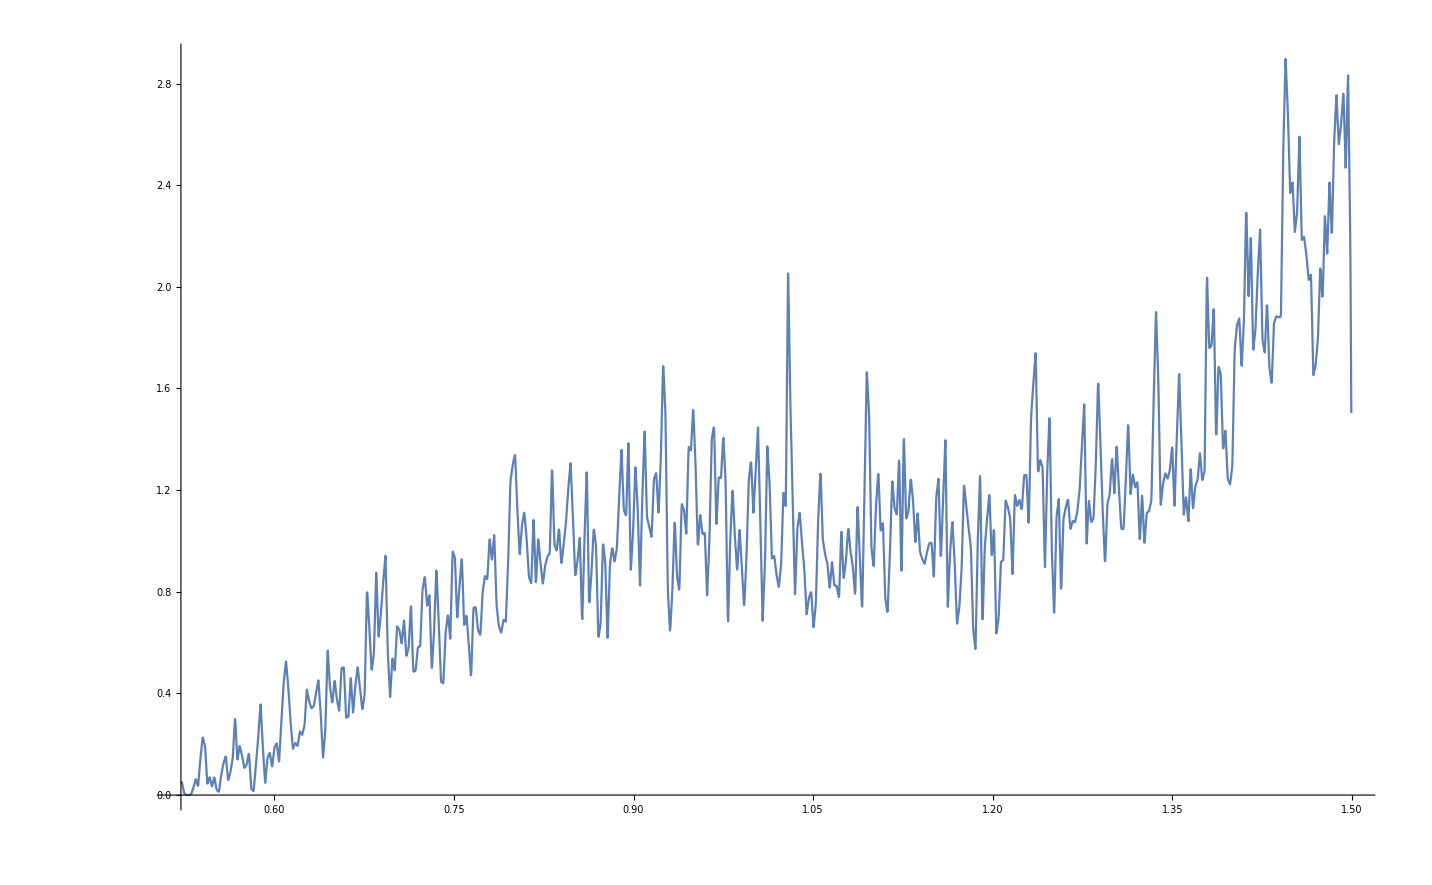

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[data3,.001],x],{x,Min[data3],Max[data3]}]
```

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[data3,.001],x],0}],{x,Min[data3],Max[data3]},{y,0,.05},AspectRatio->Automatic,PlotPoints->{1000,20}]
```

```mathematica
#,AspectRatio->Automatic,PlotPoints->{1000,20},FrameTicks->{Automatic,None},PlotRangePadding->None]
```

```mathematica
data5 = {0.49292236,0.50268771,0.50398542,0.49799356,0.49472331,0.50130725,0.50318588,0.49896378,0.49328999,0.50177809,0.50100165,0.49988993,0.49080385,0.50232965,0.50004865,0.49997229,0.49675948,0.50042236,0.50180976,0.4992634,,0.49106915,0.50028151,0.50036762,0.49995323,0.49352266,0.50178084,0.50175087,0.49969185,0.48197554,0.50351285,0.50171441,0.4999772,,0.49649973,0.50226473,0.50307803,0.49962629,0.49542361,0.50070426,0.50258234,0.4996436,,0.49990749,0.50007145,0.50003383,0.49999872,0.49059021,0.5040719,0.50089817,0.49875126,0.49027723,0.5019206,0.50164326,0.49777159,0.49705227,0.50150035,0.50182568,0.49935653,0.49816749,0.50101795,0.50065033,0.49912098,0.49699995,0.50222111,0.50271978,0.49949216,0.48914301,0.50085622,0.50002845,0.49643344,0.49331415,0.50118495,0.50339877,0.49967492,0.489576,0.50221125,0.50203106,0.49994223,0.49139579,0.50263539,0.50081485,0.49812985,0.48604846,0.50064837,0.50550479,0.49686272,0.4838202,0.50105738,0.5071936,0.49644641,0.48838734,0.50515244,0.50081271,0.4987703,,0.49032552,0.50215724,0.50072172,0.49906924,0.4922041,0.50003301,0.50193096,0.4997015,,0.49119048,0.50134727,0.50026261,0.49648718,0.4978596,0.50049841,0.50225992,0.49979046,0.48668355,0.50475953,0.5018239,0.49880538,0.49273944,0.50016473,0.5005379,0.49904831,0.49210982,0.50002138,0.5057413,0.49987043,0.48764774,0.5025638,0.50524015,0.49882589,0.48324655,0.50012581,0.5011622,0.49972564,0.47301221,0.50033595,0.50770165,0.49774874,0.49329894,0.50010089,0.50081975,0.49833972,0.48791193,0.50145852,0.50076092,0.49956261,0.47751827,0.50168508,0.50138861,0.49906439,0.48601684,0.50447963,0.50192688,0.49845095,0.4875885,0.50240281,0.50023258,0.49944176,0.48876535,0.50140191,0.50147141,0.49977911,0.48802001,0.50160883,0.50103419,0.49623059,0.49360213,0.50286706,0.50115833,0.49968015,0.48416963,0.50227122,0.50053881,0.4985757,,0.48641166,0.5017006,0.50222307,0.49630526,0.48910387,0.50105926,0.50059123,0.49990419,0.49175891,0.50218894,0.50237202,0.49992405,0.49415853,0.50138386,0.50431777,0.49953825,0.49259931,0.50334245,0.50294861,0.49821164,0.48177173,0.50639163,0.50017674,0.49723649,0.4863701,0.50607271,0.50407181,0.49958882,0.48282819,0.50365534,0.50069344,0.49378786,0.49127352,0.50053181,0.50144011,0.49998849,0.49965218,0.50007361,0.50018339,0.49985036,0.48093118,0.50051902,0.50116024,0.49755554,0.4973254,0.50001221,0.50133447,0.49881694,0.49451836,0.50163303,0.50138277,0.49778969,0.49469111,0.50232796,0.50068094,0.49776886,0.48504216,0.50175382,0.5013974,0.49564069,0.49817786,0.50148088,0.50133594,0.49953203,0.49299131,0.50366176,0.5021377,0.49745521,0.48809224,0.50446215,0.50946856,0.49969118,0.49923217,0.50010517,0.50011212,0.49972191,0.48987035,0.50009986,0.50201031,0.49891013,0.49212722,0.50001409,0.50400241,0.49920354,0.49056299,0.50196595,0.50175994,0.49775416,0.48640781,0.5001212,0.50131096,0.49857216,0.49713342,0.50076317,0.50041932,0.49906374,0.49032164,0.50223972,0.50058365,0.49951406,0.48923783,0.50333894,0.50594094,0.49983143,0.48935761,0.50255463,0.5018329,0.49916689,0.49564438,0.50126519,0.50053594,0.4983552,,0.49250445,0.50275993,0.50201531,0.49974811,0.48841561,0.50045674,0.50786005,0.49596771,0.49462489,0.50304525,0.50417562,0.49937422,0.48934472,0.50196168,0.50576079,0.49977952,0.48551651,0.50218783,0.5034406,0.49832336,0.49608994,0.50074158,0.50274992,0.49987244,0.48631586,0.5103856,0.50132893,0.49962593,0.48645293,0.50080664,0.50417691,0.49963876,0.4990239,0.50003539,0.50057174,0.49968744,0.48904263,0.50018334,0.50404492,0.49983825,0.49369945,0.50056932,0.50128344,0.49714185,0.48126968,0.50446222,0.50064869,0.49938651,0.49383358,0.50011042,0.50367077,0.4992465,,0.49542332,0.50034432,0.50153264,0.49817384,0.49296895,0.50063662,0.50435758,0.49814263,0.49472483,0.50069416,0.50088196,0.4980822,,0.49187549,0.5009937,0.5028953,0.49929746,0.48531333,0.50437818,0.50548792,0.49900774,0.49874952,0.50018595,0.50035995,0.49987749,0.49048397,0.50319595,0.50059458,0.49995386,0.49214067,0.50243397,0.50462262,0.49928097,0.49052549,0.50877664,0.50048334,0.49862521,0.49036434,0.50422836,0.50197724,0.49880009,0.4948701,0.5002496,0.50052235,0.49998226,0.49601487,0.50178842,0.50106274,0.49857183,0.48446027,0.50504022,0.50004199,0.49618241,0.49188816,0.5012416,0.50067183,0.49936187,0.48496063,0.50285787,0.50378932,0.49782152,0.49670408,0.50053135,0.50136777,0.49948917,0.48293649,0.50007065,0.51020668,0.49732846,0.48708118,0.50393263,0.50194957,0.49719736,0.48793416,0.50010161,0.50496675,0.49805473,0.49044363,0.50263916,0.50854394,0.49984044,0.48678334,0.5017117,0.50501717,0.49985815,0.49660625,0.50121195,0.50094706,0.49926634,0.47190698,0.50038091,0.5061192,0.49827436,0.4897155,0.50140214,0.50776256,0.49997762,0.4921416,0.50042966,0.5026372,0.49835692,0.46265148,0.50744859,0.50038703,0.499846,,0.49289766,0.50510306,0.50321083,0.49909751,0.48824576,0.50582394,0.50554407,0.49841456,0.47273074,0.50423295,0.50106374,0.49411454,0.48955086,0.50893519,0.50161048,0.49903756,0.48645791,0.50185332,0.50082177,0.49868587,0.48437231,0.50122603,0.50794598,0.49635408,0.47614695,0.50135785,0.5032125,0.49980463,0.4881334,0.50423876,0.50881695,0.4989165,,0.49502454,0.50029597,0.50104066,0.49818197,0.49443723,0.50410199,0.50065207,0.49844125,0.49210695,0.5008169,0.50010726,0.49947415,0.48473313,0.50309895,0.50152218,0.49783158,0.49813496,0.50382197,0.50051023,0.4999332,,0.48516935,0.50090829,0.51022716,0.49949595,0.49626213,0.50246598,0.50073339,0.49875089,0.4991468,0.50014211,0.50022982,0.49995511,0.49293665,0.5019208,0.5003064,0.49841885,0.49148184,0.5008495,0.50618693,0.49862295,0.48109152,0.50055959,0.50874161,0.49952621,0.49443543,0.50308188,0.50053202,0.49973057,0.49447136,0.50165282,0.50218674,0.49828974,0.49575566,0.50039607,0.5003365,0.49784758,0.49585725,0.50099163,0.50193475,0.4988562,,0.48185577,0.50327257,0.50441993,0.49600213,0.49108355,0.50048735,0.50372313,0.49956768,0.49419623,0.50323138,0.50040009,0.49911015,0.48389151,0.50222458,0.50111405,0.49758588,0.49332119,0.50039633,0.50137188,0.49858002,0.49292517,0.50159285,0.50392947,0.49889957,0.4835793,0.50369057,0.5007395,0.49829442,0.49431229,0.50279306,0.50165179,0.49811362,0.48385093,0.50245692,0.50007515,0.49876308,0.48269657,0.50711766,0.50215604,0.49865318,0.48359544,0.50131417,0.50740386,0.49753747,0.48730108,0.50502989,0.50013728,0.49955541,0.48861978,0.50316913,0.50073057,0.49574436,0.48679095,0.50002021,0.501062,0.49910406,0.49101763,0.50072461,0.51074838,0.4988399,,0.49232016,0.50009468,0.51068968,0.49998612,0.49051272,0.50259413,0.50178252,0.49930925,0.48556204,0.50298574,0.50075873,0.49708402,0.49659507,0.50126442,0.5031507,0.49977618,0.49861476,0.50038698,0.50216893,0.49966395,0.48805416,0.50047044,0.50598356,0.49907447,0.49025787,0.5000573,0.50695452,0.49854573,0.48651963,0.50121715,0.50160692,0.49875,,0.49496166,0.50030879,0.50071446,0.49861355,0.48286111,0.50205427,0.50293541,0.49738543,0.48760846,0.50082788,0.50224891,0.4956245,,0.49248167,0.50080081,0.50085904,0.49923258,0.49415691,0.50171546,0.50023012,0.4987155,,0.48439091,0.50161519,0.50134443,0.49582894,0.49386961,0.5017521,0.50216472,0.49825331,0.48503315,0.50196635,0.50065595,0.49991883,0.49523723,0.50007835,0.50010647,0.49877244,0.49503637,0.50112674,0.50444901,0.49950777,0.49736775,0.50096874,0.50026149,0.49945837,0.4838937,0.50037697,0.50469989,0.49878586,0.48591337,0.51194423,0.50113607,0.4995689,,0.48789561,0.50079061,0.50257923,0.49797744,0.49039405,0.50194053,0.5046321,0.49838128,0.47897746,0.50727777,0.50129327,0.49914903,0.49048205,0.50890282,0.5017341,0.49864371,0.47676366,0.50505811,0.50381831,0.49994155,0.49057843,0.50855612,0.50122695,0.499419,,0.49018282,0.50279086,0.50457968,0.4986743,,0.47638295,0.50418283,0.50005281,0.49905927,0.48650126,0.50114107,0.50167664,0.49411165,0.4965639,0.50533241,0.50050104,0.4999249,,0.49088311,0.50075826,0.50780361,0.49919924,0.4972051,0.5018524,0.50000498,0.4999695,,0.49426758,0.50049826,0.50081678,0.49803952,0.49566157,0.50081211,0.50136868,0.49792654,0.4874081,0.5009709,0.50032234,0.49823943,0.48627779,0.50645994,0.50025076,0.49921046,0.49347528,0.50210701,0.50099729,0.49846422,0.49031402,0.5046932,0.50218578,0.49858246,0.48184076,0.50149107,0.50379911,0.49444536,0.49665547,0.50134709,0.50012315,0.49894683,0.48242818,0.50262322,0.50460503,0.4981001,,0.49173065,0.5081382,0.50011067,0.49877368,0.49702532,0.50016841,0.50028264,0.4996321,,0.48012186,0.50770855,0.5027325,0.49862872,0.49404954,0.50016299,0.50380874,0.49946764,0.49456219,0.50269743,0.50049326,0.49832443,0.47907854,0.50059371,0.50109805,0.49448136,0.49897491,0.50022596,0.50006779,0.49983138,0.48272723,0.50083429,0.50192814,0.49833986,0.49295552,0.50100884,0.5020356,0.49965603,0.49382954,0.50350308,0.5033696,0.49824209,0.48256394,0.51072811,0.5015233,0.49889499,0.49731624,0.50024099,0.5000429,0.49930826,0.47712757,0.50144234,0.5052108,0.4962318,,0.49314208,0.50329374,0.50136136,0.49918547,0.49676024,0.50076154,0.50100821,0.4994444,,0.48684564,0.50489379,0.5015093,0.49992294,0.49636352,0.50070827,0.50074522,0.49891916,0.4933533,0.50015267,0.50092583,0.49858041,0.497892,0.50027817,0.50081367,0.49985875,0.47813237,0.50373601,0.50556673,0.49743405,0.4944689,0.50053137,0.50576513,0.49971752,0.49676474,0.50095512,0.50379156,0.49980939,0.49642796,0.50048842,0.50121711,0.4984263,,0.47817742,0.50567672,0.50544895,0.49815195,0.48736125,0.50812549,0.50122007,0.49818489,0.48895447,0.5048474,0.50348232,0.49845848,0.48720233,0.50855174,0.50019725,0.49905267,0.47319364,0.50126504,0.50205442,0.49392166,0.4924663,0.50031988,0.50640853,0.49888041,0.49905265,0.50044214,0.50002306,0.4995998,,0.48289461,0.51042107,0.50060175,0.49923218,0.4920158,0.50290263,0.50518336,0.49930715,0.49282128,0.5042179,0.50146939,0.49923177,0.4971681,0.50086925,0.50127499,0.49983273,0.49243621,0.50379883,0.50045683,0.49965469,0.48882563,0.50054238,0.50194498,0.49645339,0.49131366,0.50231995,0.50228596,0.49964039,0.48207519,0.50754206,0.50036075,0.49938537,0.48826999,0.50079054,0.50305912,0.4996237,,0.49572747,0.50268966,0.50171121,0.4992272,,0.48951923,0.50790743,0.50302441,0.49975488,0.48048682,0.5022316,0.50299072,0.49748278,0.48788908,0.50058679,0.50333092,0.49469688,0.49728963,0.50121198,0.50024088,0.49964249,0.49435575,0.50032493,0.50079979,0.49989059,0.49811709,0.5005928,0.50095202,0.49999785,0.48543074,0.50197311,0.50042792,0.4999321,,0.48603705,0.50007327,0.50690695,0.49604817,0.48023383,0.50075436,0.50292087,0.49753549,0.49186424,0.50131833,0.50065476,0.49725483,0.46804328,0.50458674,0.50243445,0.49858498,0.48955489,0.50203793,0.50202167,0.49666076,0.49089689,0.50185287,0.50021265,0.49642505,0.49027137,0.50298952,0.50332864,0.49888746,0.48333429,0.50595789,0.5044963,0.49931189,0.49094732,0.50032496,0.50029008,0.49703728,0.49215194,0.50234701,0.50117345,0.4974749,,0.48384615,0.50184485,0.50996003,0.49964355,0.48827005,0.50412127,0.50041222,0.49885511,0.48023389,0.50465508,0.5002599,0.49926279,0.4882999,0.5082179,0.5001482,0.49966717,0.4905223,0.50356295,0.5006934,0.49969069,0.48261147,0.51257833,0.50205763,0.49995899,0.4928789,0.50284264,0.50373251,0.49885725,0.48931869,0.50089823,0.50237266,0.49700835,0.49141219,0.50067588,0.50096747,0.4990485,,0.49562052,0.50109322,0.50404918,0.49920857,0.49789129,0.50030371,0.50004592,0.49978439,0.49762061,0.50051863,0.50086562,0.49995879,0.49073058,0.50264552,0.50193154,0.49938101,0.49442846,0.50101552,0.50550113,0.49972618,0.4914263,0.50148703,0.50227179,0.49807086,0.4954101,0.5003028,0.50512012,0.49881453,0.48627385,0.50070351,0.50103381,0.49415954,0.49245407,0.50029959,0.50148771,0.49994509,0.49066228,0.50036955,0.50378988,0.49768456,0.48985193,0.50078995,0.50566951,0.49829746,0.49553509,0.50068263,0.50089689,0.49855575,0.48988744,0.50046757,0.5004735,0.49975327,0.48248582,0.50491646,0.5006238,0.49894262,0.48769497,0.50011623,0.50348798,0.49965319,0.48894228,0.50494835,0.50818283,0.4996892,,0.47511265,0.50028678,0.5015206,0.49854362,0.49510065,0.50290675,0.50032127,0.49893311,0.48986603,0.50222895,0.50006894,0.49968613,0.49899704,0.50049141,0.50066555,0.49965817,0.48155636,0.50118794,0.51087378,0.49955097,0.47816513,0.5035754,0.50173005,0.49666479,0.47290732,0.50157179,0.50832232,0.49858358,0.49101614,0.50125358,0.50251559,0.4970477,,0.47318927,0.50735905,0.50202275,0.49992429,0.47992465,0.50776771,0.5039648,0.49872096,0.49675395,0.50006641,0.50024099,0.49820442,0.48720265,0.50038857,0.50550829,0.4999584,,0.480812,0.50012903,0.50017995,0.4974743,,0.48548897,0.50453589,0.50311947,0.4976494,,0.4928565,0.50201457,0.50052139,0.49959908,0.47352535,0.50023262,0.50074575,0.49966131,0.4968453,0.50424654,0.50075783,0.49956875,0.49849659,0.50049315,0.5005571,0.49983301,0.48777107,0.50481069,0.50445412,0.49873531,0.47572813,0.50207745,0.50451349,0.49872266,0.48765145,0.50503115,0.50184437,0.49800571,0.4910562,0.50102114,0.50722506,0.49939312,0.49668306,0.50102988,0.50035964,0.49934159,0.48851417,0.50267906,0.50757361,0.49892626,0.47921965,0.5000236,0.50386552,0.49909894,0.48522598,0.50266951,0.50287516,0.49927219,0.49051127,0.5001335,0.50090907,0.4972661,,0.49544228,0.50014255,0.50021999,0.49842599,0.49937331,0.50004837,0.50046213,0.49987444,0.4904524,0.5066872,0.50111266,0.49861301,0.49765266,0.50017093,0.50081588,0.49980127,0.4785065,0.50383321,0.50349049,0.49653717,0.49526034,0.5015482,0.50104206,0.49924752,0.49287355,0.50069231,0.50057311,0.49922898,0.49721056,0.50020432,0.50139908,0.49974091,0.47645239,0.50925899,0.50219461,0.49793481,0.48925434,0.50080277,0.50357659,0.4993422,,0.49957542,0.50000598,0.50030292,0.49991394,0.48424961,0.50252511,0.5067008,0.49907967,0.49222744,0.50145895,0.50025022,0.49729995,0.47985095,0.50563403,0.50293659,0.49735651,0.48253051,0.50557929,0.5008998,0.4992017,,0.48633016,0.50009185,0.51014594,0.49702037,0.48220761,0.50271606,0.50522997,0.49861035,0.4906045,0.5041033,0.50062767,0.49904384,0.4834777,0.50038496,0.50097172,0.498183,,0.48301118,0.5018125,0.50153195,0.49669227,0.49423826,0.50085098,0.5013683,0.49872534,0.4774554,0.50160742,0.50127427,0.49877538,0.49138602,0.50776122,0.50015057,0.49932874,0.49328168,0.50099008,0.50117611,0.49966029,0.49387716,0.50029776,0.50272838,0.49867063,0.49962024,0.50015004,0.50038156,0.4999658,,0.48884782,0.50443288,0.50166474,0.49630557,0.47917137,0.50101443,0.50092226,0.49388115,0.49058286,0.5041373,0.50467422,0.49897377,0.494287,0.50018541,0.50002093,0.49991287,0.47637049,0.50256555,0.50352838,0.49884695,0.48510545,0.50482548,0.50276172,0.49791667,0.49124133,0.50026939,0.50284423,0.49981691,0.48595669,0.50056393,0.50110866,0.49743534,0.49068749,0.5058172,0.50003552,0.49949979,0.48077167,0.50301795,0.50055606,0.4999416,,0.49127385,0.5028539,0.50229064,0.498702,,0.49168248,0.50219965,0.50089285,0.49946754,0.49497125,0.50606557,0.50070469,0.49940991,0.49405778,0.50072499,0.50315051,0.4989757,,0.49613789,0.50023867,0.50281436,0.49982893,0.48438727,0.50168527,0.50034861,0.49437825,0.49041303,0.50194222,0.50170426,0.49956653,0.49697094,0.50059071,0.50080365,0.49999468,0.4910312,0.50012439,0.50100817,0.49984452,0.48936358,0.50345639,0.50300669,0.49801701,0.4914225,0.50274538,0.50498381,0.4990937,,0.48131193,0.50085029,0.50214946,0.49694578,0.49868921,0.50073686,0.50085339,0.49993792,0.49919393,0.50058589,0.50015445,0.49981426,0.47998723,0.50126673,0.50005067,0.49629581,0.49156191,0.50976786,0.50251244,0.49970107,0.49591134,0.50136423,0.50451827,0.49927751,0.49036679,0.50111278,0.50378215,0.49806094,0.48158671,0.50491119,0.50273802,0.49910645,0.49085102,0.50360755,0.50029955,0.49939441,0.48947529,0.5019205,0.50281776,0.49755175,0.49449529,0.50279795,0.50079553,0.49993838,0.49170806,0.5003945,0.50084098,0.49975936,0.49317792,0.50122284,0.50019684,0.49853977,0.49613722,0.50083338,0.50058892,0.49939663,0.4931753,0.5015222,0.50011913,0.49948972,0.4924003,0.50137623,0.5005251,0.49647056,0.4844015,0.50938317,0.50368884,0.49932848,0.4896771,0.5005081,0.50090167,0.497748,,0.48227916,0.50362713,0.50042298,0.49720007,0.49113096,0.50045504,0.50211552,0.49786839,0.48579049,0.50633842,0.50489587,0.49764112,0.49462478,0.50004484,0.50120425,0.49886765,0.48382128,0.50698218,0.50128207,0.49740051,0.49769408,0.50018171,0.50066553,0.49939612,0.49475655,0.50400084,0.50072355,0.49983558,0.48333983,0.50018055,0.50285061,0.49435905,0.49147349,0.50685092,0.50082151,0.49879577,0.49573042,0.50195981,0.5038362,0.49976837,0.48837822,0.50378982,0.5038314,0.49674157,0.47540778,0.50103008,0.50158869,0.49726433,0.49792784,0.50137966,0.50012809,0.49996255,0.48823324,0.50312002,0.50606997,0.49935551,0.49130642,0.50017793,0.50085817,0.49885832,0.47740029,0.50613675,0.50572901,0.49915871,0.48618795,0.50463958,0.50413038,0.49591081,0.48946163,0.51025657,0.50028298,0.49786298,0.49871277,0.50034369,0.50042196,0.499993,,0.49401214,0.50026507,0.50108352,0.49921134,0.49100766,0.50178103,0.50367491,0.49745298,0.48295692,0.50613428,0.50053818,0.49986043,0.4935776,0.50101387,0.50057249,0.49826298,0.49396567,0.50022404,0.50153767,0.49933802,0.49897037,0.50057075,0.50063834,0.49985522,0.47139877,0.50200513,0.50200913,0.49726683,0.49251515,0.50441354,0.50189963,0.49741429,0.4802492,0.50345218,0.50027263,0.49449892,0.49588301,0.50038258,0.50057657,0.49978319,0.49096131,0.50469908,0.50424773,0.49996206,0.49941771,0.50011322,0.50006313,0.49987559,0.4965474,0.5010086,0.50006083,0.49980374,0.49418045,0.50134655,0.50250224,0.49987568,0.49196443,0.50209345,0.50240933,0.49835881,0.49618624,0.50194127,0.50291895,0.49986524,0.4923537,0.50094675,0.50390634,0.49872474,0.4817942,0.50223394,0.50155417,0.49865756,0.49166818,0.5001534,0.50157394,0.49909405,0.49640975,0.50173805,0.50092987,0.49941693,0.49156029,0.50140851,0.50009411,0.49727967,0.49163655,0.50250096,0.50149101,0.49645807,0.49128808,0.50702971,0.50223996,0.49838891,0.49754357,0.50066366,0.50013794,0.49989696,0.48868885,0.50055355,0.50053847,0.49994695,0.49254201,0.50487402,0.50363607,0.49920246,0.48633205,0.5028709,0.50478963,0.49833532,0.48836437,0.50289182,0.50236418,0.49864902,0.4915224,0.50034371,0.50742803,0.49930473,0.48488815,0.50144358,0.50238336,0.49960772,0.49679483,0.50033966,0.50116405,0.49992516,0.4856936,0.50754628,0.50048676,0.49818916,0.4891171,0.50336756,0.50010443,0.49944204,0.47652539,0.50022994,0.50708308,0.49644125,0.48936757,0.50171474,0.50163823,0.49595317,0.49435986,0.50119024,0.50248145,0.49943508,0.49293892,0.50026009,0.5070924,0.49935417,0.49352569,0.50255428,0.5037313,0.49979876,0.47408858,0.5022988,0.50141027,0.49749867,0.48251811,0.50331351,0.50065222,0.4972163,,0.49033462,0.50689376,0.50266413,0.49971835,0.49794554,0.50063226,0.50160074,0.49978363,0.49012285,0.50417325,0.51075722,0.49947654,0.49821375,0.50055304,0.50015441,0.49985761,0.4839734,0.50016765,0.50594196,0.49779242,0.48843526,0.50006402,0.50715004,0.49841927,0.49575828,0.5015205,0.50087519,0.49872765,0.48693219,0.50366755,0.50530384,0.49840648,0.49182987,0.50064003,0.50030546,0.49955446,0.49864065,0.50010207,0.50073139,0.49987617,0.49249544,0.50065364,0.50746923,0.49918897,0.49807226,0.50005191,0.50064881,0.49984431,0.48642494,0.50055238,0.50572288,0.49992808,0.49382742,0.50204764,0.50151933,0.49996569,0.49576069,0.50031999,0.50485383,0.49918825,0.47135147,0.50015094,0.50147794,0.49528958,0.4925173,0.50341996,0.50121689,0.49870882,0.48560658,0.50265899,0.50118249,0.49390461,0.48398662,0.50120371,0.50116867,0.49984885,0.49925783,0.50010604,0.50056815,0.4999849,,0.49574424,0.50174381,0.5013598,0.49870176,0.49255398,0.50272151,0.50094092,0.49791168,0.49104222,0.50766843,0.5012521,0.49930619,0.49879067,0.50094543,0.50128796,0.49996091,0.47985466,0.50112184,0.50179322,0.49625786,0.49597576,0.50032517,0.50197531,0.4996607,,0.49545746,0.50003653,0.50448119,0.49946548,0.49444683,0.50294476,0.50724222,0.49943927,0.49365415,0.5007604,0.50061257,0.49814384,0.49076637,0.50226448,0.50373346,0.498021,,0.48094082,0.50362493,0.50296674,0.4968425,,0.49515184,0.50124814,0.5020881,0.49813923,0.48858145,0.50175007,0.5028252,0.49929864,0.48522007,0.50052813,0.50076069,0.49594407,0.49629942,0.50127975,0.50260439,0.49962989,0.48455553,0.50358397,0.5041197,0.49893354,0.4873004,0.50631081,0.50396523,0.49988486,0.48447844,0.50947409,0.50010502,0.49891116,0.49425258,0.50209743,0.50487343,0.49860705,0.4859872,0.50183938,0.50505914,0.49886791,0.49499499,0.50167017,0.50001627,0.49949226,0.48283771,0.50145496,0.50091366,0.4982104,,0.48683489,0.50016841,0.50055587,0.49997337,0.49587865,0.5003832,0.5011161,0.49907052,0.4840436,0.5026929,0.50098241,0.49820869,0.48747897,0.50027173,0.50034906,0.49931819,0.49463819,0.50505011,0.50039512,0.49986335,0.49527164,0.5047481,0.50215664,0.49948227,0.49550758,0.50046867,0.5004327,0.49884276,0.49309262,0.50058146,0.50171351,0.49939453,0.49208686,0.50111006,0.50150899,0.49974436,0.4764182,0.50847354,0.5020574,0.49914632,0.4837619,0.50601056,0.50070828,0.49935402,0.4940451,0.50154774,0.50043276,0.49906572,0.48787645,0.50298193,0.5034429,0.49922346,0.48183175,0.50637696,0.50233861,0.49986378,0.48422547,0.50042954,0.5036483,0.49923982,0.48962198,0.50345749,0.50179694,0.49976534,0.49399462,0.50037855,0.50257981,0.49915436,0.49732472,0.50114259,0.50030784,0.49951581,0.49697086,0.50156551,0.50009388,0.49995653,0.48456163,0.5013737,0.50709474,0.49891983,0.49263272,0.50008706,0.50228216,0.49978615,0.49466269,0.50004599,0.50043818,0.49940593,0.49400338,0.50265894,0.50326028,0.49874822,0.4953904,0.50066358,0.50354308,0.49967881,0.48503488,0.50041053,0.50262954,0.49810004,0.48985912,0.50347162,0.50229359,0.49957057,0.49172802,0.50737652,0.5004522,0.4999393,,0.49237249,0.50045163,0.50025236,0.49917171,0.48117258,0.50374439,0.50145146,0.49824425,0.48815767,0.50091924,0.50494235,0.49742859,0.48131417,0.50623823,0.50258722,0.49840061,0.49682704,0.50135271,0.50005559,0.49901409,0.49008812,0.50212222,0.50208473,0.49704088,0.4963444,0.50292971,0.50088982,0.4991141,,0.49775615,0.50192721,0.50052162,0.49939574,0.49580461,0.50313724,0.5002368,0.49925944,0.490864,0.50051809,0.50048988,0.49857368,0.47773413,0.50634643,0.5001363,0.49752742,0.48867306,0.50343969,0.50361005,0.49848627,0.48077964,0.50024974,0.50789997,0.49897966,0.49264615,0.50103916,0.50193244,0.49991455,0.4908221,0.5004921,0.50110058,0.49719535,0.49602117,0.50057437,0.50038807,0.49851406,0.48198335,0.50402166,0.50198344,0.49966283,0.4882463,0.50163995,0.50702253,0.49692837,0.48811968,0.50376464,0.50318981,0.49841403,0.49432923,0.5032484,0.50019951,0.4997448,,0.47575819,0.5005908,0.50305283,0.49887491,0.48180697,0.50202022,0.50044357,0.49773856,0.48189623,0.50234065,0.50179816,0.49608585,0.49285148,0.50304693,0.50044314,0.49760636,0.49545599,0.50241714,0.50152379,0.49986551,0.4981398,0.50130096,0.50095697,0.49941359,0.48737197,0.50261123,0.50046493,0.49835676,0.48980802,0.50220421,0.50285427,0.49808379,0.46961507,0.50493548,0.50267134,0.4978256,,0.49472482,0.50099482,0.50147058,0.49877537,0.48268453,0.50400826,0.50061049,0.49557301,0.48393511,0.50763189,0.50772777,0.49993936,0.49970997,0.50003434,0.50009218,0.49999813,0.48473065,0.50098295,0.50128164,0.49936993,0.49550083,0.50041808,0.5014882,0.49969493,0.48886221,0.50012425,0.50240509,0.49619484,0.49334124,0.50023526,0.50625722,0.49874867,0.4881363,0.50165863,0.50100008,0.49768296,0.4758313,0.50071434,0.50337169,0.49702887,0.48547715,0.50582796,0.50122194,0.49952728,0.49159868,0.50132152,0.50684098,0.49985798,0.4767433,0.50132162,0.50869021,0.49868356,0.49617625,0.50237595,0.50109493,0.49930235,0.49620728,0.50039767,0.50050771,0.49874307,0.49322678,0.50511156,0.50213455,0.4987397,,0.48660518,0.50066579,0.50328009,0.49435115,0.49845595,0.50055536,0.500361,0.49970302,0.48323663,0.5084578,0.50117577,0.49682067,0.49526727,0.50181514,0.50178191,0.498364,,0.49369551,0.50055023,0.50215692,0.49910413,0.47560514,0.50338355,0.50814729,0.49832857,0.47360383,0.50834288,0.50534071,0.49912399,0.49318666,0.50120278,0.50343982,0.49996624,0.49753495,0.50151121,0.50034888,0.49948213,0.48440343,0.50278628,0.50211787,0.49716389,0.48888206,0.50004029,0.50358135,0.49826215,0.48329746,0.50021372,0.50355735,0.49848697,0.49476138,0.50043032,0.50262007,0.4979032,,0.49221021,0.50023405,0.50262016,0.49865315,0.49786233,0.50094545,0.50095344,0.49971029,0.48670898,0.50108308,0.50041278,0.49797252,0.48667062,0.50365252,0.50120213,0.4983676,,0.48014103,0.50310254,0.50006677,0.49370403,0.47803856,0.50249609,0.50221909,0.49916725,0.4915206,0.50368537,0.50516573,0.4986901,,0.4912006,0.50255568,0.50084325,0.49995305,0.48954,0.50534697,0.50063324,0.49900731,0.48390165,0.5085479,0.50068695,0.49935627,0.49677424,0.5020382,0.50030726,0.49934478,0.4985217,0.50007505,0.50076481,0.4995933,,0.49802502,0.50005354,0.50215774,0.4994096,,0.4888195,0.50257696,0.50635104,0.49734028,0.48449342,0.50769698,0.50084575,0.49820739,0.49756122,0.50418958,0.50012251,0.49992025,0.48717479,0.50043028,0.50221806,0.49732961,0.48265863,0.50885152,0.50034834,0.49857436,0.47303276,0.50222295,0.50294391,0.49774994,0.49794042,0.5007161,0.50031919,0.49981968,0.49508237,0.50040003,0.50013899,0.49959269,0.48915142,0.50077817,0.50014829,0.49931167,0.49555576,0.50003588,0.50187197,0.49953186,0.49388879,0.50335371,0.5015249,0.4999496,,0.49168833,0.50327318,0.50575936,0.49968055,0.482159,0.50693983,0.50003163,0.4964978,,0.48286,0.50019293,0.50037269,0.49806651,0.49415647,0.50381038,0.50062728,0.49959133,0.49086778,0.5086689,0.50005681,0.49928382,0.48968737,0.50065677,0.50327777,0.49729587,0.49632806,0.50284164,0.50072483,0.49928465,0.48674897,0.50345027,0.50003906,0.49602855,0.49143819,0.50122604,0.50382757,0.49948725,0.47206689,0.50035794,0.50370442,0.49860311,0.48691069,0.50142337,0.50169578,0.49825003,0.48823418,0.50034843,0.50001583,0.49717377,0.49317113,0.50146361,0.50294226,0.49903948,0.48843219,0.50021712,0.50107444,0.49693625,0.48019148,0.50024589,0.50749558,0.49818666,0.48709832,0.50539262,0.50157195,0.49840441,0.48982535,0.50052387,0.5063749,0.49981278,0.49213269,0.50099434,0.50220689,0.49741705,0.49419731,0.50466881,0.50099612,0.49759611,0.48483453,0.50215167,0.50106891,0.49906186,0.49509645,0.50329488,0.50031513,0.4998612,,0.47428816,0.50023754,0.50154879,0.49949749,0.49651571,0.50011895,0.50035165,0.49842828,0.49112728,0.50451441,0.50128883,0.49997319,0.48656282,0.50105504,0.50687834,0.49930467,0.4943668,0.50127325,0.50090295,0.49948203,0.49056524,0.51062543,0.50023411,0.49958367,0.49632577,0.50107934,0.50330222,0.49981636,0.48962536,0.50066149,0.50695355,0.49881405,0.49647676,0.50016607,0.50355092,0.4995042,,0.48635542,0.50305356,0.50078965,0.49708152,0.49062842,0.50282896,0.50056134,0.49911353,0.48973243,0.50140987,0.50051812,0.49446098,0.48955397,0.50573627,0.50012883,0.49790611,0.49386326,0.50135542,0.50133309,0.49792218,0.49537817,0.50304565,0.50274595,0.49999592,0.49832663,0.5012255,0.50144676,0.49979702,0.49328447,0.50019716,0.50234506,0.49735415,0.48124376,0.50503006,0.50279522,0.49949937,0.4949538,0.50042548,0.50027679,0.4999407,,0.49651799,0.5013175,0.50006162,0.49977057,0.48333416,0.51058503,0.50199185,0.49855105,0.49238415,0.5003931,0.50018057,0.49661777,0.48751592,0.5012671,0.50498108,0.49721172,0.4966161,0.50386463,0.50121085,0.49977604,0.49278253,0.50750346,0.5028344,0.49964898,0.47060192,0.50294664,0.50202066,0.49974169,0.49391202,0.50032946,0.50027701,0.49927337,0.49144555,0.50378221,0.50103403,0.49936713,0.48473063,0.50692578,0.50545298,0.49857537,0.49975397,0.50000469,0.50003521,0.49988148,0.49014596,0.5044529,0.50157468,0.49802768,0.48626849,0.50205526,0.50323186,0.4969157,,0.48164289,0.500606,0.50006389,0.49762942,0.4950109,0.50125258,0.50194291,0.49890358,0.47258435,0.50500249,0.50176976,0.49887417,0.49634686,0.50030874,0.50081018,0.49904412,0.48811658,0.50338341,0.50457089,0.49746021,0.48990178,0.50312231,0.50299184,0.49988196,0.49336948,0.50413241,0.50018225,0.49833289,0.49211708,0.50556936,0.50274063,0.49862416,0.48643026,0.51102485,0.50092529,0.49764669,0.4929779,0.50120918,0.50158972,0.49952944,0.48512229,0.50173848,0.50682481,0.49853603,0.49810573,0.50076031,0.50050265,0.49984658,0.49244908,0.50206488,0.50214041,0.49786926,0.4962604,0.50025072,0.50069074,0.4995558,,0.48779264,0.50474375,0.50084377,0.49743543,0.49032208,0.50295149,0.50133277,0.49774675,0.49527493,0.5000357,0.5016418,0.49970332,0.49660462,0.50062149,0.50003778,0.49981305,0.49534809,0.50158129,0.50231164,0.49979296,0.49043257,0.50361326,0.50198239,0.4990008,,0.48611301,0.50084711,0.50167931,0.49746697,0.47815735,0.50053403,0.5013666,0.49861045,0.49137707,0.50093537,0.50234672,0.49976359,0.49425662,0.50206021,0.50169311,0.4990727,,0.49233006,0.50282764,0.50209257,0.49833702,0.49476975,0.50315972,0.50053096,0.49942374,0.49671803,0.50021156,0.50072415,0.49981889,0.49244313,0.50192226,0.50016995,0.4982157,,0.49162909,0.50102427,0.50187684,0.49987356,0.493863,0.5063646,0.50025928,0.49980642,0.48052567,0.50144444,0.5002684,0.49623093,0.4881175,0.50218113,0.50235927,0.49661291,0.49534376,0.50126348,0.50095699,0.49991751,0.48911655,0.50699666,0.50350423,0.49946544,0.49065452,0.5009061,0.501118,0.49942872,0.49151895,0.50322859,0.50277589,0.49964715,0.48709875,0.50104847,0.50247319,0.49987276,0.48004651,0.50379279,0.50230891,0.49886025,0.49304172,0.50016576,0.5040157,0.49898118,0.48402712,0.50019884,0.50069278,0.49925915,0.48824215,0.50354683,0.50505033,0.49878236,0.48786838,0.50093104,0.50011594,0.4999856,,0.49272078,0.50565157,0.50088416,0.49973172,0.49109628,0.50286362,0.5013169,0.4994532,,0.49439743,0.50308075,0.500272,0.4991692,,0.4970681,0.50130346,0.50133609,0.49942888,0.48678027,0.50158599,0.50078759,0.49560814,0.49267631,0.50272266,0.50036856,0.4997318,,0.48588248,0.50093314,0.50000832,0.49990637,0.48314036,0.50084487,0.50182775,0.49753703,0.48939223,0.50119097,0.50146484,0.49932145,0.49486179,0.50173654,0.50134512,0.49871878,0.49680583,0.50091278,0.50152137,0.49956497,0.49008322,0.5025996,0.5045275,0.49838146,0.48543642,0.5015243,0.50031784,0.4984849,,0.48120778,0.50439503,0.50381657,0.49800662,0.49454243,0.5001887,0.50570799,0.49994295,0.49711182,0.50226715,0.50109635,0.49908084,0.49534543,0.50041917,0.50269527,0.49920825,0.49697325,0.50052399,0.50121398,0.49990963,0.49180821,0.50299674,0.50127609,0.49977213,0.47847133,0.50016109,0.50404329,0.49759269,0.49765021,0.50080707,0.5013433,0.49982903,0.4763577,0.50308305,0.50382692,0.49867185,0.49370967,0.50169725,0.50027245,0.49953262,0.48251799,0.50980225,0.50332692,0.49926649,0.48465739,0.50099389,0.50315536,0.49987749,0.48504948,0.50296513,0.50315659,0.49772553,0.47925082,0.50118842,0.50612302,0.49582744,0.48995654,0.50557751,0.50110504,0.49870317,0.49626479,0.50171489,0.50034536,0.49963324,0.48516217,0.50188193,0.50056098,0.496153,,0.4864535,0.50350416,0.50035455,0.49962641,0.48994036,0.50087752,0.50606796,0.49751695,0.49370408,0.50542214,0.50007383,0.49974887,0.48451696,0.50020182,0.5087054,0.49937844,0.49428325,0.50381428,0.50191612,0.49960472,0.47752695,0.50202685,0.51388756,0.49849806,0.49418157,0.50061607,0.50630614,0.49955866,0.48855252,0.5021137,0.50361706,0.49981748,0.47557289,0.50757887,0.50613018,0.49991255,0.47995659,0.50432706,0.50045473,0.49621065,0.49770728,0.50162231,0.50221736,0.49998112,0.48596251,0.50785046,0.50090559,0.49925376,0.49839734,0.50067012,0.50003534,0.49998203,0.47103752,0.50086007,0.50044566,0.49774455,0.48466175,0.5077168,0.50033488,0.49817697,0.48380336,0.50806056,0.50440892,0.49843703,0.48387405,0.50185035,0.5019651,0.49957156,0.48739478,0.5060039,0.50187695,0.49891464,0.4859947,0.50257003,0.50209893,0.49646287,0.48394524,0.50274722,0.50555848,0.49982772,0.48857384,0.50093112,0.50649078,0.49796189,0.49015777,0.50553184,0.50530458,0.49935879,0.48806276,0.5056339,0.50076692,0.49979662,0.49670286,0.50072418,0.50017135,0.49981208,0.48466518,0.5052354,0.5016148,0.49734217,0.49138987,0.5012615,0.50048778,0.49932863,0.49134615,0.50307955,0.50256937,0.499999,,0.49523608,0.500022,0.50360084,0.49753171,0.48972413,0.50104679,0.50205043,0.49779351,0.48880221,0.50408595,0.50003846,0.49924198,0.48716424,0.50268532,0.51066861,0.49845487,0.49004628,0.50257332,0.50261054,0.49672318,0.48319559,0.50679054,0.50084536,0.49995799,0.49599114,0.50101764,0.50041288,0.49892039,0.49484885,0.50403735,0.50028725,0.4995278,,0.49617198,0.50118765,0.50169157,0.49958411,0.48588908,0.50318456,0.50143623,0.49983311,0.48868945,0.50297798,0.50075525,0.49934132,0.48976337,0.50148118,0.5026895,0.4978565,,0.48668099,0.50029589,0.50223057,0.49793548,0.48888282,0.50847746,0.50107389,0.49925913,0.47688228,0.50719178,0.50160868,0.49737148,0.48137442,0.50003603,0.50018239,0.49682523,0.48336751,0.50134234,0.50375405,0.49913326,0.49073389,0.5020574,0.50482168,0.49815356,0.49829878,0.50093466,0.50148986,0.49934818,0.49374816,0.50114695,0.5052353,0.49932097,0.4966822,0.50040409,0.50346126,0.49984483,0.47954094,0.50016671,0.50010104,0.49714655,0.48013819,0.50124855,0.50049347,0.49959557,0.49443583,0.50007001,0.5049702,0.4989853,,0.48975795,0.50089266,0.50358038,0.49780955,0.48719571,0.50368646,0.50608812,0.49754996,0.48498792,0.50106711,0.50091494,0.49810612,0.48620822,0.50029033,0.5006323,0.49297686,0.48376582,0.50358105,0.50033614,0.49898126,0.48826255,0.50136811,0.50047459,0.49994583,0.4795168,0.50426618,0.50312312,0.49867577,0.49537453,0.50062451,0.50062829,0.49955636,0.48530891,0.50018032,0.50252876,0.49782913,0.48222823,0.50565579,0.50463254,0.49698934,0.48962052,0.5033059,0.50021652,0.4969483,,0.49689653,0.50168064,0.50158381,0.4999087,,0.49455967,0.5004725,0.50264479,0.49897991,0.47328367,0.50389907,0.50000774,0.49990145,0.48980113,0.50113558,0.50124257,0.49854834,0.49608981,0.50354312,0.50224392,0.49961493,0.47242655,0.50240873,0.50281073,0.49473,,0.49662524,0.50227215,0.50043098,0.49876917,0.4797629,0.51100544,0.50276573,0.49915054,0.4843689,0.50088793,0.500671,0.49869832,0.48608581,0.50003714,0.5035887,0.49975682,0.48448353,0.50439205,0.50273235,0.4980406,,0.49694102,0.50062239,0.50197488,0.49941964,0.49108996,0.50740302,0.50067338,0.49916114,0.48339711,0.50640272,0.50710937,0.49929445,0.47971859,0.5001518,0.50559711,0.49821798,0.49471918,0.50065595,0.5041649,0.49903587,0.48490674,0.50087619,0.50044998,0.49825991,0.49477884,0.50351881,0.50019996,0.49972825,0.4973464,0.50014775,0.50084327,0.49995884,0.48271953,0.50364074,0.50535753,0.49893647,0.49639271,0.50044578,0.50154986,0.49833874,0.49532579,0.50140536,0.50011275,0.49905417,0.48846903,0.50092113,0.5049528,0.49809416,0.49537703,0.50105547,0.500206,0.49984006,0.48989196,0.50060435,0.50075024,0.49773862,0.47938084,0.50479745,0.5041395,0.49853743,0.49716912,0.50081227,0.50261884,0.49987445,0.48852117,0.50380064,0.5014622,0.49746357,0.49124998,0.5002449,0.5007163,0.49866198,0.48606017,0.5015352,0.50065583,0.49609172,0.4793915,0.50466125,0.50475885,0.49998744,0.49204829,0.50085834,0.5023011,0.4996519,,0.49372882,0.50079614,0.50015917,0.49944928,0.48836117,0.50033844,0.50285025,0.49770256,0.4868879,0.50197857,0.5086093,0.49841305,0.48928438,0.50591859,0.50376283,0.49881918,0.48648498,0.50327915,0.50004102,0.49719298,0.49731839,0.50056863,0.50005717,0.49938716,0.4803322,0.50651164,0.50088983,0.49865095,0.49581097,0.50228978,0.50110338,0.49905596,0.48731604,0.5002022,0.50007155,0.49879096,0.48935216,0.50215655,0.5017329,0.49801175,0.49190306,0.50355755,0.50292762,0.49873405,0.49703793,0.50063291,0.50132018,0.49963098,0.49595337,0.50004695,0.50002183,0.49821783,0.49372524,0.50047209,0.50046105,0.49950234,0.49937698,0.50043763,0.50032022,0.49998759,0.4892639,0.50060495,0.50310722,0.49911483,0.48772957,0.50066436,0.50322367,0.49799768,0.49667815,0.50031821,0.50133392,0.4991951,,0.48704049,0.50139924,0.50049165,0.49883055,0.48753942,0.50626542,0.50074749,0.4986072,,0.49015135,0.50027263,0.50162922,0.49976221,0.48307586,0.50300682,0.50226645,0.4991168,,0.48389798,0.50030861,0.50463849,0.49548648,0.47253123,0.50024791,0.50018754,0.49529801,0.49336411,0.50077108,0.50757757,0.49972181,0.4890198,0.5003821,0.5000927,0.49901228,0.49079374,0.50200435,0.50051334,0.49764724,0.47497118,0.50219806,0.50009334,0.49886042,0.48616349,0.50062614,0.50075848,0.49980235,0.48037502,0.50204433,0.50202496,0.49595037,0.4832922,0.50460726,0.50126996,0.4978868,,0.48486909,0.50043714,0.50466043,0.49980612,0.48201319,0.50047377,0.50764787,0.49950708,0.49235212,0.50512137,0.50572411,0.49970021,0.47752088,0.50001837,0.50424248,0.4985282,,0.48898979,0.50619219,0.50225764,0.49925125,0.49762264,0.50028224,0.50172696,0.4995869,,0.48408179,0.50079287,0.50073646,0.49798525,0.49671411,0.50019021,0.50176152,0.49980636,0.49408852,0.5008559,0.50044742,0.49873113,0.48678595,0.5041796,0.50370531,0.49861505,0.48056306,0.50314488,0.50276723,0.49726041,0.48290429,0.50191883,0.50275712,0.49673295,0.47671099,0.50185765,0.50782069,0.49856871,0.49746779,0.50168273,0.50208972,0.49986222,0.48805887,0.50475442,0.5036752,0.49908863,0.48605425,0.50448314,0.50272262,0.49848441,0.49461103,0.50060559,0.50014583,0.49987883,0.48107689,0.50465266,0.50214015,0.49971032,0.49084265,0.50266304,0.50224047,0.49815598,0.49354912,0.50280136,0.50323122,0.49969125,0.48292475,0.50133338,0.50081408,0.49691904,0.47879455,0.50185973,0.50923479,0.49977534,0.49047506,0.50463352,0.50300725,0.4995501,,0.49639537,0.50120107,0.50065931,0.49974546,0.48932901,0.5012847,0.50050678,0.49556838,0.49645355,0.50065816,0.50004016,0.49963638,0.48527611,0.5012123,0.50374971,0.49920639,0.48734908,0.50061167,0.50011234,0.49537279,0.49208536,0.50084915,0.50475966,0.49918275,0.49127369,0.50276748,0.50725561,0.49838304,0.4878144,0.50133155,0.50409239,0.49835779,0.48435298,0.5022696,0.5028448,0.4994915,,0.48954231,0.50514452,0.50352546,0.49973167,0.49306712,0.50105118,0.50049054,0.49983939,0.46122495,0.50445639,0.50040642,0.49856484,0.48685996,0.50134033,0.51065667,0.49892798,0.48704078,0.50336329,0.50559898,0.49830045,0.48810407,0.50090238,0.50496672,0.49937796,0.49103533,0.50300093,0.50136593,0.49900015,0.47681867,0.50365737,0.50004704,0.4920514,,0.47907603,0.5016675,0.5006318,0.49830343,0.49248697,0.50016134,0.50105246,0.49805275,0.49436621,0.50033641,0.50039414,0.49827483,0.49356106,0.50447363,0.5029544,0.49970332,0.49302053,0.50834005,0.50125619,0.49918172,0.49128888,0.5009117,0.5004798,0.49963067,0.49198252,0.5039162,0.50402366,0.49994802,0.49173238,0.50208901,0.50362159,0.49713778,0.48553957,0.50077238,0.50228563,0.49454778,0.47274124,0.50264073,0.50141903,0.49961784,0.49440664,0.50020384,0.50054292,0.49892089,0.49804086,0.50025483,0.50103776,0.49969924,0.49052191,0.50364956,0.50019014,0.49798116,0.49611741,0.50011503,0.50292227,0.49971348,0.48296147,0.50534239,0.50379805,0.49914303,0.4966519,0.50157002,0.50111206,0.49869741,0.4914106,0.50104584,0.50382594,0.49894087,0.48574666,0.50075087,0.50330025,0.49582653,0.49252809,0.50007469,0.50521424,0.49945896,0.48389305,0.50014092,0.50525123,0.49565407,0.49367451,0.5022831,0.50176298,0.49811246,0.49141411,0.50229809,0.50032997,0.49779682,0.47473377,0.5057382,0.50096842,0.49549532,0.49275188,0.50167762,0.50085609,0.49806698,0.49748638,0.50192306,0.50070721,0.49999831,0.49863226,0.50142813,0.50027845,0.49958654,0.48125724,0.50059052,0.5083561,0.49793691,0.48456699,0.50026295,0.50328565,0.49929263,0.49619966,0.50051399,0.50064334,0.4985224,,0.48030358,0.50071944,0.50486981,0.49659364,0.48518634,0.50077843,0.50361328,0.49996177,0.49281594,0.50218366,0.50190522,0.4988109,,0.4966801,0.50024741,0.50409201,0.4998954,,0.48479676,0.502403,0.50424417,0.49987161,0.48830424,0.50135879,0.50773423,0.49951259,0.49388621,0.50100168,0.50007733,0.49928127,0.49547712,0.50030939,0.50241495,0.49825969,0.49663126,0.50319851,0.50177973,0.49973329,0.49129992,0.50197001,0.50131817,0.49828466,0.49848512,0.50042022,0.50140769,0.49997955,0.489355,0.50110281,0.50952014,0.49892007,0.48132179,0.5055553,0.50002159,0.49798755,0.49257269,0.50107412,0.50337267,0.49823686,0.49594416,0.5003271,0.50152747,0.49911863,0.48311636,0.50278207,0.50237665,0.49665679,0.48939089,0.50048068,0.50616687,0.49969249,0.49628333,0.50082577,0.50197926,0.49918658,0.49485355,0.50147342,0.50057963,0.49877295,0.4912607,0.50028304,0.5033424,0.49658173,0.49760287,0.50028544,0.50050814,0.49987125,0.49249831,0.50315652,0.50184084,0.49968059,0.48756087,0.50337182,0.50109595,0.49769032,0.49630176,0.50507739,0.50042379,0.49925902,0.49779485,0.50025264,0.50045554,0.49968837,0.48572721,0.50422254,0.50110271,0.49902057,0.47629136,0.50552873,0.50227672,0.49843888,0.49956941,0.50037376,0.50003346,0.49986193,0.47735812,0.50336775,0.50256762,0.49780671,0.49325276,0.50167443,0.50227697,0.49875793,0.47127747,0.50382301,0.5002407,0.49869097,0.4908809,0.50056222,0.50238577,0.49639379,0.48697836,0.5008799,0.50157313,0.49884289,0.49003044,0.50374605,0.50121453,0.49849072,0.49192093,0.5010214,0.50005261,0.49570436,0.49374149,0.50558712,0.5015056,0.49985002,0.48370405,0.5014238,0.50489266,0.4990756,,0.49362555,0.50052987,0.50177886,0.4971668,,0.48249897,0.50280139,0.50253017,0.49925253,0.47738648,0.51066759,0.50328789,0.49935407,0.48490193,0.50236242,0.50016229,0.49631416,0.48426243,0.50138833,0.50916556,0.49653189,0.49696457,0.50153734,0.50191753,0.4993594,,0.48990169,0.50004932,0.50242331,0.49758132,0.48290226,0.50438248,0.50341941,0.49809649,0.48625682,0.50405899,0.50129418,0.49676849,0.48886822,0.50057725,0.50761551,0.49903823,0.48024763,0.50248529,0.50111578,0.49744333,0.48663172,0.50087863,0.51000445,0.49884869,0.47984542,0.50324177,0.50154025,0.49348958,0.49313127,0.50205567,0.50480168,0.49953977,0.49162958,0.50350469,0.50190911,0.49964915,0.49651708,0.50021424,0.50109074,0.49919111,0.49615609,0.50206188,0.50071026,0.49974944,0.48820953,0.50029332,0.50314345,0.49685374,0.49275981,0.50208811,0.50234131,0.49806369,0.49066625,0.50396541,0.50096014,0.49892558,0.48762365,0.50208122,0.50106195,0.49579188,0.48612949,0.50266627,0.50639004,0.49749951,0.49894613,0.50012564,0.500111,0.49970515,0.48172728,0.50137459,0.5033691,0.49780979,0.48386124,0.50262704,0.50541467,0.49959484,0.48028902,0.50004379,0.50448862,0.49840991,0.48456299,0.50239018,0.50077117,0.49750858,0.49690583,0.50016065,0.50253196,0.49995923,0.48571147,0.50318167,0.50086757,0.49963232,0.49201745,0.50021572,0.50052451,0.4968728,,0.49730567,0.50266375,0.50030775,0.49997682,0.4933638,0.50384379,0.50142493,0.49886966,0.46974289,0.50189755,0.50187903,0.49972657,0.49533158,0.50535294,0.5011519,0.49915561,0.49235977,0.50156724,0.50067484,0.49966031,0.48265874,0.50162567,0.50142701,0.49628516,0.49896859,0.50027611,0.50003462,0.4997063,,0.49052827,0.50889649,0.50023067,0.49975197,0.48834637,0.50561029,0.50087611,0.49798424,0.49448005,0.50023845,0.50058902,0.49828747,0.49127183,0.50110192,0.50334306,0.49879116,0.48606651,0.50125006,0.5043641,0.49846995,0.49331259,0.50444351,0.50446682,0.49981531,0.48843115,0.50155853,0.50395698,0.49996025,0.49272121,0.50095097,0.50056389,0.49962845,0.49448624,0.50539043,0.50033404,0.49996318,0.47762034,0.50528307,0.50190975,0.49756875,0.49167985,0.50656963,0.50249488,0.498701,,0.49064468,0.50058642,0.50097725,0.49564211,0.49499255,0.50441804,0.50083352,0.49985044,0.48552628,0.50568247,0.50083544,0.49566636,0.48691761,0.50467475,0.5074175,0.49770237,0.49270417,0.50101599,0.50202,0.49729028,0.48604353,0.50713879,0.50032813,0.498564,,0.48786946,0.50077564,0.51067535,0.49811513,0.49404778,0.50006491,0.50555278,0.49857278,0.49501476,0.50062419,0.5005842,0.49816526,0.48771665,0.50081245,0.50726113,0.49960408,0.48444628,0.50067809,0.50183841,0.4972824,,0.4864795,0.50050991,0.50430413,0.49919301,0.49088359,0.50373751,0.50029613,0.49955081,0.4921711,0.5009473,0.50209774,0.49758132,0.49467005,0.50248108,0.50032457,0.49980851,0.49323101,0.50402776,0.50105313,0.49902524,0.49703989,0.50182091,0.50022882,0.49961583,0.47899087,0.50013456,0.50070149,0.49763221,0.48270407,0.50257704,0.5028427,0.49813662,0.48726963,0.5009631,0.50310787,0.49613236,0.48882755,0.50510695,0.50124678,0.49985596,0.4978315,0.50072232,0.50292158,0.49957176,0.49473002,0.50102632,0.50104166,0.49991711,0.49194268,0.50117373,0.5005212,0.49983233,0.495531,0.50489671,0.50011294,0.4994308,,0.48616196,0.50376692,0.50011989,0.49672875,0.49412304,0.50209526,0.50234066,0.49980359,0.49656936,0.50116738,0.50190887,0.49980565,0.49046253,0.50063502,0.50234726,0.49787137,0.49027518,0.50392122,0.50278073,0.49757549,0.48718391,0.50012233,0.50745023,0.4997995,,0.49044935,0.50098795,0.50142274,0.49882014,0.4727728,0.50181993,0.50040287,0.49731956,0.49379439,0.50026384,0.50320404,0.49725005,0.49212464,0.50166906,0.50026383,0.49972166,0.48244727,0.50080512,0.50391704,0.49903994,0.49106888,0.50674083,0.50119461,0.49947574,0.49299006,0.50075637,0.50210692,0.49868175,0.48847694,0.50458211,0.50359884,0.49919406,0.49211303,0.5020743,0.50262823,0.49991335,0.4828618,0.50226697,0.50428623,0.49882297,0.49039736,0.5010511,0.50480843,0.49689349,0.4950128,0.50251901,0.50064908,0.49957592,0.48958474,0.50117581,0.50449459,0.49961064,0.49072988,0.50324002,0.50426772,0.4997422,,0.49585289,0.50099051,0.50007408,0.49945023,0.49696093,0.50186089,0.50009363,0.49989342,0.49056713,0.5045762,0.50021132,0.4981038,,0.48980022,0.50553313,0.50106776,0.49691996,0.4902003,0.50005155,0.50771878,0.49925193,0.49002243,0.50039117,0.50076517,0.49830643,0.48892588,0.50152576,0.50330929,0.49868235,0.49655281,0.50187633,0.5016059,0.49897168,0.48485023,0.50389881,0.50327368,0.4995291,,0.49600896,0.50055781,0.50054998,0.49823749,0.49162889,0.50295837,0.50041856,0.49977787,0.49774344,0.50140606,0.50023533,0.49890329,0.49708375,0.50081475,0.50016425,0.49860898,0.48742548,0.50116642,0.50043201,0.49904429,0.48426514,0.50163295,0.50198201,0.49929263,0.49941559,0.50009167,0.50030549,0.49970233,0.49045017,0.50350827,0.50513986,0.49953286,0.4973513,0.5004793,0.50052019,0.49941113,0.48788957,0.50136426,0.50132671,0.49848562,0.48392026,0.50348635,0.50076499,0.49875275,0.49578053,0.50321243,0.50077749,0.49870663,0.49340285,0.50237632,0.50055546,0.49989914,0.47790353,0.50348643,0.50178312,0.49902172,0.49366819,0.50638601,0.50170803,0.4997512,,0.49157226,0.5027095,0.50345633,0.49997402,0.49499115,0.50147495,0.50209096,0.49997332,0.49336996,0.5003045,0.50398959,0.49829751,0.47881956,0.50039703,0.50724233,0.49585129,0.49681359,0.50072435,0.50050875,0.49918824,0.47335444,0.50044994,0.50745458,0.49810112,0.49217157,0.50124406,0.5005372,0.49908097,0.48005325,0.50324651,0.50122002,0.49842084,0.48573073,0.50543597,0.50375545,0.49627819,0.48333789,0.50435737,0.50080376,0.49937454,0.49496321,0.5022408,0.50207069,0.49853448,0.4852968,0.50454629,0.50465148,0.49656487,0.4865549,0.50724787,0.50241309,0.49961241,0.49605545,0.50387891,0.50000495,0.49978574,0.49136046,0.50418596,0.50013275,0.49719623,0.4840918,0.50500445,0.50432086,0.49885124,0.49960034,0.50006542,0.50001916,0.49997316,0.47780377,0.50271219,0.50636718,0.49979612,0.48705259,0.50007185,0.5013835,0.49324563,0.47666548,0.50359834,0.5071463,0.49756842,0.48179399,0.50288093,0.50015652,0.49928122,0.48750994,0.50583251,0.50009356,0.49979428,0.48732589,0.50000841,0.50548472,0.49994508,0.49228794,0.50256296,0.50470696,0.49996124,0.4964787,0.5009563,0.50081439,0.4999693,,0.49140573,0.50029853,0.50125394,0.49834277,0.49625246,0.5017063,0.50118175,0.49953965,0.48306095,0.50244906,0.50133723,0.49767344,0.49250871,0.50120149,0.50046755,0.49753751,0.49246424,0.50105435,0.50191542,0.49987401,0.49776127,0.50165194,0.5001473,0.49997798,0.49845472,0.50094019,0.50013413,0.49990995,0.49393585,0.50188088,0.5018938,0.4988897,,0.48060743,0.50035867,0.51179891,0.49932952,0.48497158,0.50316771,0.50732266,0.4970212,,0.49355014,0.50348597,0.50086009,0.49829489,0.49259537,0.50127613,0.50392543,0.49794879,0.49504027,0.50163087,0.50042305,0.49996728,0.49442028,0.50007988,0.50102339,0.49956734,0.4984943,0.50028212,0.50030409,0.49954718,0.49346275,0.50102857,0.50280781,0.49953548,0.47738839,0.50022821,0.50122663,0.49928926,0.49281357,0.50153947,0.50071707,0.49705442,0.49611632,0.50043386,0.50146941,0.49880181,0.49455564,0.50099255,0.50090191,0.49888091,0.49769038,0.50136283,0.50242224,0.49978946,0.49025591,0.50091312,0.50323351,0.4998647,,0.48101531,0.503852,0.50085794,0.49959712,0.49521776,0.50044342,0.50150908,0.49869337,0.49801669,0.5008475,0.50141562,0.49953112,0.48381324,0.50150714,0.50004461,0.49758628,0.49459539,0.50104572,0.50061055,0.49893556,0.49317451,0.50092262,0.50433831,0.49947459,0.49347684,0.50048297,0.50073558,0.49719264,0.49556123,0.50080331,0.50194628,0.49941878,0.47917161,0.50268587,0.50278982,0.49716342,0.47821943,0.50017322,0.50421247,0.49952681,0.48699554,0.50439163,0.50176107,0.49764178,0.49679243,0.50015069,0.50149503,0.49930869,0.49297622,0.50118237,0.50075313,0.49867665,0.49305123,0.50010239,0.50144238,0.495683,,0.4830066,0.50997165,0.50156908,0.49819378,0.49061166,0.50125704,0.50724653,0.49950512,0.48798441,0.50170304,0.50433262,0.49892324,0.48810593,0.50368718,0.50751169,0.49952445,0.47542786,0.50011126,0.5004644,0.4934174,,0.49257589,0.50146109,0.50022014,0.49636465,0.48456997,0.50252238,0.50105831,0.49914147,0.49615773,0.50169207,0.5019856,0.4987146,,0.48572889,0.50971126,0.50101402,0.49911301,0.48882546,0.50107393,0.50437806,0.49915173,0.47600351,0.50574891,0.50534609,0.49872837,0.49104639,0.50111645,0.50097307,0.49976777,0.49527011,0.50136429,0.50105382,0.49962963,0.4891235,0.50111682,0.50170158,0.4959473,,0.48945081,0.50361378,0.50378126,0.49758262,0.49701753,0.50027403,0.50122463,0.49989507,0.48744869,0.50274942,0.50120383,0.49946893,0.48984714,0.50374093,0.50075743,0.49828239,0.49129712,0.50015519,0.50275494,0.49769574,0.48768377,0.50112431,0.50040978,0.49640116,0.48808947,0.50099821,0.50275269,0.49949272,0.49103137,0.50049902,0.50223075,0.49837884,0.48845812,0.50388569,0.50266755,0.49867782,0.49345647,0.50106272,0.50087444,0.49743277,0.49761335,0.50050595,0.50140582,0.49994188,0.48168265,0.5007163,0.50001711,0.49805151,0.49281565,0.50087502,0.50071254,0.49863474,0.48598109,0.50048172,0.50432615,0.49688929,0.49535353,0.50191583,0.50674235,0.4997269,,0.49576025,0.50214397,0.50034831,0.4997557,,0.49019511,0.501901,0.50700907,0.49999899,0.49144066,0.5014171,0.50028177,0.49936496,0.49633072,0.50083805,0.5006595,0.49964671,0.49180153,0.50071826,0.50208551,0.49886379,0.49520989,0.50079363,0.50038718,0.49927299,0.49060303,0.50481141,0.50009021,0.4992155,,0.47688186,0.50170371,0.50268764,0.49960207,0.48589443,0.50206253,0.50663734,0.49727219,0.48883887,0.50139896,0.50125405,0.49583234,0.49160711,0.50299649,0.5030634,0.4985379,,0.49118262,0.50060376,0.50000775,0.49983952,0.49212881,0.5009842,0.50388333,0.49965445,0.48874767,0.50180598,0.50137967,0.49421594,0.48969463,0.50057084,0.50040374,0.49756457,0.49533735,0.50089351,0.50004419,0.49742992,0.49573858,0.50182103,0.5007482,0.49929942,0.48583583,0.50162985,0.50024118,0.49944158,0.47909312,0.50191247,0.50021818,0.49857298,0.48596343,0.50146046,0.50889642,0.49969767,0.49581069,0.50556064,0.50040627,0.499087,,0.49634367,0.50245211,0.50000297,0.49943186,0.49620379,0.50220312,0.50321609,0.49934852,0.49060637,0.50087149,0.50391262,0.49909097,0.49451892,0.50057246,0.5015154,0.49992069,0.48698823,0.50042695,0.5049128,0.49894212,0.4919244,0.50135468,0.50655576,0.49997641,0.49773941,0.50008907,0.50335415,0.49991679,0.48626823,0.50500128,0.50124763,0.49818342,0.48615286,0.50442778,0.500952,0.49963362,0.48425487,0.5015409,0.50756348,0.49767971,0.49588901,0.5021492,0.50115105,0.49960136,0.49114918,0.50005547,0.50942036,0.49883531,0.49712301,0.50032998,0.50180336,0.49970282,0.49311013,0.50279661,0.50115597,0.49801401,0.49474244,0.50293326,0.50120198,0.49846353,0.49442478,0.5016546,0.50204066,0.49995293,0.48087993,0.50335048,0.50260709,0.49793265,0.49422235,0.50038067,0.50198695,0.49978351,0.49061742,0.50692369,0.50091696,0.49892462,0.49131933,0.50119866,0.50347501,0.49956783,0.49546627,0.50063654,0.50356573,0.49893496,0.49747216,0.50115966,0.50011247,0.49989459,0.49334653,0.50046809,0.50155394,0.49983448,0.49542231,0.50251494,0.50184261,0.49864731,0.4824198,0.50489333,0.50373048,0.49618163,0.47618362,0.50445198,0.50161753,0.4969072,,0.49498143,0.50178087,0.5004224,0.49888754,0.47937654,0.50407563,0.50163732,0.49811424,0.4964243,0.50012337,0.5002698,0.49909922,0.48564812,0.50360072,0.50348527,0.49911386,0.48290922,0.5118629,0.5010105,0.49882746,0.49196456,0.5003248,0.50032899,0.49928567,0.47605681,0.50883317,0.50081637,0.4974247,,0.48959072,0.50272934,0.50342689,0.4980454,,0.49657408,0.50075797,0.50042344,0.49937908,0.49371915,0.50189399,0.50157479,0.49895382,0.49472448,0.50098117,0.50005743,0.49923617,0.48375302,0.50078386,0.50495506,0.49934044,0.47135071,0.5010753,0.50086365,0.49844333,0.47200155,0.50407444,0.50010682,0.49791448,0.49434755,0.50453415,0.50080557,0.49951273,0.48250616,0.50145288,0.50304372,0.49846175,0.49000035,0.50061074,0.50018495,0.4999381,,0.49434292,0.50156931,0.50062854,0.49786526,0.49143623,0.50238025,0.50353723,0.4997984,,0.48102674,0.50117753,0.50573842,0.49882612,0.48545908,0.50163613,0.50092151,0.49988637,0.49486064,0.50223805,0.50109076,0.49892939,0.48576779,0.50271267,0.50008109,0.49949726,0.49128712,0.50051244,0.50700458,0.49855452,0.49913985,0.50004215,0.50071878,0.4996965,,0.487736,0.50062191,0.50298898,0.49785177,0.48409769,0.50240237,0.5008746,0.49761864,0.48458879,0.50301062,0.50029301,0.49846147,0.49008724,0.50351667,0.50215626,0.49806565,0.48129564,0.50047355,0.50489802,0.49407904,0.47884604,0.50597864,0.50074938,0.49945359,0.4804774,0.50273649,0.50064663,0.49737444,0.48469346,0.50271156,0.50202527,0.499622,,0.49285967,0.50060218,0.50029806,0.49897662,0.4848613,0.50173076,0.50148792,0.49567228,0.4889503,0.50126824,0.50359018,0.49862613,0.46972906,0.50104927,0.50293851,0.49651887,0.47943109,0.50416406,0.50293134,0.49534053,0.484482,0.50301959,0.50253623,0.49804944,0.48316693,0.50221312,0.50488285,0.49794139,0.48149158,0.50284732,0.50441162,0.49830854,0.49286713,0.50081631,0.50009529,0.49902471,0.48857343,0.50170908,0.50119749,0.49747711,0.49340312,0.50112227,0.50097571,0.49957129,0.47751368,0.50073967,0.50146551,0.49963066,0.48872181,0.505658,0.50083036,0.49779349,0.48653317,0.50017701,0.50482497,0.49987128,0.4954753,0.50232428,0.5009849,0.49989348,0.49542427,0.50050695,0.50208815,0.49759072,0.49377143,0.5000601,0.50005687,0.49889725,0.48892805,0.50005331,0.50379615,0.49763249,0.48136017,0.50631248,0.50193173,0.49973418,0.49421378,0.50066378,0.50072825,0.49886714,0.47731241,0.50275611,0.50189437,0.49403762,0.49762745,0.50204749,0.50165365,0.49966195,0.48874371,0.50256639,0.50059617,0.49803403,0.49399316,0.50126508,0.5003396,0.49792448,0.49731658,0.50011328,0.50058546,0.49861532,0.47515076,0.50090155,0.50209431,0.49815356,0.49183937,0.50182112,0.50084346,0.49732223,0.48632372,0.50407871,0.50316166,0.49869508,0.48996568,0.50954256,0.50035538,0.49975105,0.48899963,0.50151557,0.50439247,0.49679911,0.49747593,0.50077538,0.50171942,0.49993711,0.49721624,0.50070987,0.5000321,0.49986075,0.48603762,0.50009189,0.502245,0.49764044,0.49430447,0.50157972,0.50007209,0.49997163,0.49219529,0.50180655,0.50377858,0.49999248,0.49280801,0.50093379,0.50244542,0.49999656,0.49632983,0.50104798,0.50409101,0.49996459,0.49562489,0.5001141,0.50151799,0.49972802,0.49703327,0.50372647,0.50052086,0.49930908,0.49857875,0.50114173,0.50043012,0.49979021,0.49320867,0.50358118,0.50374207,0.49937509,0.49252532,0.50380127,0.50063246,0.49942224,0.48568589,0.50102069,0.50126268,0.49423943,0.49675285,0.50164351,0.50008751,0.49996913,0.48879304,0.50531057,0.50168484,0.49988218,0.49199236,0.50065932,0.50182972,0.49895721,0.49055756,0.50083112,0.50272872,0.49987789,0.499328,0.50021877,0.50025008,0.49994851,0.48208541,0.50637552,0.50302321,0.49954775,0.48469687,0.50344419,0.50205708,0.4991269,,0.48457404,0.50535442,0.50242677,0.49810705,0.4967399,0.50163972,0.50139096,0.49932662,0.49900382,0.5000734,0.50004249,0.49947672,0.49774799,0.50037501,0.50225596,0.49987765,0.49316354,0.50213868,0.50190057,0.49681594,0.48513953,0.50218187,0.50672761,0.49776123,0.47953244,0.50180637,0.50113203,0.49458925,0.4929565,0.50200029,0.50606367,0.49976167,0.492332,0.50071697,0.50211505,0.49753261,0.48812161,0.50001711,0.50144157,0.49543726,0.49309381,0.50517828,0.50232947,0.49925911,0.49176735,0.50319526,0.50881457,0.49988711,0.47608227,0.50063105,0.50230373,0.49641009,0.49690537,0.5004685,0.50006484,0.4994168,,0.49209321,0.50109259,0.50354752,0.4987302,,0.49153789,0.50588357,0.50053241,0.49950979,0.4780283,0.50285996,0.50219815,0.49988975,0.4916795,0.50281394,0.50118395,0.49680634,0.49419506,0.50205874,0.50315655,0.49987547,0.49093653,0.5028487,0.5019162,0.49873166,0.49308641,0.50410995,0.5015286,0.49978205,0.48027953,0.50147238,0.50603518,0.49704652,0.47865576,0.50244904,0.50058596,0.49939252,0.49532018,0.50177471,0.50274288,0.49918347,0.49578806,0.50013218,0.50587637,0.49999184,0.49291745,0.5052769,0.5017913,0.4984872,,0.49173686,0.50057698,0.50058347,0.49823047,0.48759257,0.50224342,0.50057307,0.49915633,0.49756725,0.50170069,0.50054413,0.4998249,,0.49513228,0.50009375,0.50105561,0.49765357,0.49679822,0.50078452,0.50160341,0.49967364,0.49463693,0.50425392,0.50154947,0.49995422,0.4695554,0.50358731,0.50323378,0.49991605,0.48374539,0.50019328,0.50996731,0.49687841,0.48260873,0.50160546,0.50260529,0.49987073,0.48165728,0.50681559,0.5037447,0.49969031,0.4827212,0.50197052,0.50357071,0.49604423,0.4959001,0.5010202,0.50231173,0.49925573,0.48575345,0.50205871,0.50067778,0.49848492,0.49422425,0.50214298,0.50087006,0.49878448,0.49249766,0.50160262,0.50176861,0.49897024,0.48259386,0.50773178,0.50389863,0.49883466,0.49418278,0.50064237,0.50130579,0.49825443,0.49242039,0.5023197,0.50239239,0.49917678,0.49615115,0.5021698,0.50124907,0.49925959,0.4995916,0.50049017,0.50004375,0.49988794,0.49260959,0.50052515,0.50214911,0.49710443,0.49354054,0.50025994,0.50087201,0.49878562,0.49888978,0.50036479,0.500364,0.49994133,0.49023915,0.50001499,0.50026143,0.49957029,0.47468512,0.50372659,0.50305469,0.49551274,0.48739313,0.50148712,0.50163211,0.49826781,0.49061735,0.50071289,0.50340262,0.49921895,0.49893757,0.50012418,0.50003774,0.49953194,0.49313719,0.5017717,0.50192605,0.49953163,0.49759047,0.50038324,0.50043147,0.49973207,0.49085961,0.50223027,0.5017243,0.49823802,0.49489418,0.50225323,0.5004638,0.49979815,0.49890215,0.50000076,0.50016008,0.49973535,0.49047484,0.50307442,0.50283192,0.49564611,0.49373954,0.50286375,0.50005912,0.49850804,0.48313757,0.50385502,0.50265736,0.49849233,0.48948069,0.50040436,0.50276655,0.49628548,0.4880477,0.50165647,0.50081594,0.49894091,0.49764967,0.5010433,0.50100329,0.49986504,0.4899188,0.50251622,0.50306448,0.49979148,0.48768497,0.50223938,0.5062222,0.49994178,0.4872473,0.50038148,0.50057038,0.49712669,0.49502505,0.50222653,0.50028891,0.49946812,0.49896091,0.50008839,0.5002634,0.49993115,0.48197215,0.50288747,0.50427645,0.49545485,0.49269635,0.50589694,0.50106205,0.49934378,0.48433435,0.50032479,0.51180244,0.49928266,0.49743504,0.50181069,0.50103944,0.49974242,0.48860672,0.50321657,0.50001893,0.49979917,0.49300214,0.50005956,0.50207771,0.49916419,0.47907459,0.50279939,0.50264101,0.49948026,0.49464261,0.50209474,0.50186118,0.49996252,0.48776934,0.5010453,0.50596977,0.49751711,0.49291731,0.50174427,0.50230657,0.49985161,0.49300943,0.50086146,0.50178136,0.49832634,0.499097,0.50018065,0.50032636,0.4998375,,0.47272547,0.50017121,0.50229979,0.49639262,0.48538503,0.50026811,0.50724353,0.49783675,0.49230756,0.50185046,0.50219206,0.49613567,0.48473459,0.50203069,0.50070425,0.4977381,,0.49031459,0.5032445,0.50282814,0.49828968,0.49595888,0.50359817,0.50097608,0.49916192,0.49327227,0.50600247,0.50048503,0.49962141,0.4959401,0.50016689,0.50041103,0.49834741,0.49264328,0.50031613,0.50768469,0.49857189,0.48929242,0.50156359,0.50524711,0.49928602,0.48621563,0.50163618,0.50156244,0.49794272,0.47287508,0.50852707,0.50123253,0.49765149,0.49558376,0.50044843,0.50702167,0.4999046,,0.47906141,0.50560243,0.50049613,0.49997926,0.49327579,0.5055867,0.50076152,0.49984394,0.49026218,0.50478042,0.5044388,0.49762088,0.49916608,0.50002202,0.50090878,0.4999892,,0.48321122,0.50014453,0.51145482,0.49855897,0.49587714,0.50029628,0.500311,0.49955203,0.49546859,0.50202298,0.50115542,0.49988146,0.49383556,0.50344525,0.50061849,0.49814268,0.48982852,0.5042969,0.50015124,0.49900319,0.49491195,0.50142035,0.50013669,0.49969589,0.48943747,0.50342835,0.50285372,0.49977385,0.47616544,0.50168609,0.50031782,0.49763549,0.48999213,0.50627718,0.50336014,0.49921548,0.49117316,0.50167823,0.50383563,0.49768676,0.49401354,0.50112991,0.50177769,0.49824389,0.4901035,0.50190811,0.50881917,0.49957694,0.49766917,0.50023962,0.5004552,0.49960139,0.49470796,0.50180291,0.50106105,0.49919923,0.48964875,0.50416652,0.50180646,0.49856736,0.47093802,0.50072717,0.50245007,0.49917266,0.48959909,0.50713282,0.50359475,0.49980436,0.49113909,0.50328801,0.50541194,0.49941134,0.48619159,0.50382087,0.50526648,0.49800176,0.48342741,0.50516216,0.50947078,0.49972431,0.49200237,0.5020303,0.50151876,0.49835583,0.49888714,0.50026254,0.50005907,0.49963313,0.48330748,0.50206633,0.50418394,0.49725803,0.49105755,0.50103876,0.50419088,0.49880302,0.49017938,0.50226222,0.50033528,0.49921838,0.49563552,0.50000555,0.5000534,0.49803347,0.49501649,0.50060287,0.50015002,0.49926997,0.48705575,0.50142704,0.50291239,0.49893881,0.49290523,0.50120261,0.50040662,0.49976071,0.49383607,0.50061095,0.5025858,0.49919934,0.47434971,0.501993,0.50389534,0.49598528,0.47578663,0.50617121,0.50081514,0.4966856,,0.49708299,0.50007485,0.50014968,0.49984372,0.47789527,0.50382166,0.50497873,0.49877023,0.49520367,0.50275028,0.50503713,0.4996502,,0.48544158,0.50031991,0.50413658,0.49937519,0.4949854,0.50158471,0.50022822,0.49757728,0.46839155,0.50048828,0.50442319,0.49980119,0.48324834,0.50427675,0.50423496,0.49719113,0.4866977,0.50071172,0.50012195,0.49964234,0.4915289,0.50184228,0.50306092,0.49793948,0.49711867,0.50124783,0.50259946,0.49969612,0.49891947,0.50033611,0.50057782,0.49981516,0.496411,0.50003036,0.50283364,0.49990326,0.4972835,0.50016981,0.50096424,0.49980696,0.49543081,0.50031123,0.50186611,0.49899115,0.48817308,0.50054441,0.50009856,0.4994663,,0.49141489,0.5006419,0.5033585,0.49971951,0.49676503,0.50033702,0.50046394,0.49918719,0.48954891,0.50336443,0.50388508,0.49892368,0.47190618,0.5059713,0.50062641,0.49824102,0.49624642,0.50084872,0.50084988,0.49904291,0.47469975,0.50911119,0.50152807,0.49790699,0.49106641,0.50109988,0.50633345,0.49974118,0.49592564,0.50161506,0.50019451,0.49996768,0.48731117,0.50660142,0.5055368,0.4979505,,0.49488095,0.50130412,0.50022421,0.4970885,,0.48247006,0.50135099,0.50210144,0.49542129,0.49504769,0.50743555,0.50083715,0.49975998,0.48755706,0.50443247,0.50093971,0.49906615,0.48088238,0.50229661,0.50158143,0.49732077,0.48679773,0.50296432,0.50090356,0.4978855,,0.46394949,0.50264865,0.50032503,0.49936095,0.499485,0.50000332,0.50012458,0.49995224,0.49631607,0.50209611,0.50267211,0.49971644,0.48913772,0.50010963,0.50088924,0.49790485,0.49576997,0.50142056,0.5032733,0.49922145,0.48347772,0.5012885,0.50063124,0.49641447,0.48883185,0.5001083,0.50471639,0.49887705,0.4795284,0.50896018,0.50372505,0.49894481,0.47878968,0.51043644,0.50117618,0.49885383,0.49100631,0.50160683,0.51156127,0.49970235,0.4992205,0.50024144,0.50024134,0.49994407,0.49840255,0.50038036,0.50109761,0.49921986,0.497954,0.50071453,0.50032773,0.49978353,0.48112918,0.50515258,0.5042516,0.49984333,0.48599919,0.50288473,0.50248717,0.49900172,0.49233332,0.50152035,0.50202466,0.4976708,,0.48726231,0.5083514,0.50524415,0.49992098,0.49180618,0.50249283,0.50154481,0.49814492,0.48928225,0.50057119,0.50134449,0.49803043,0.49560143,0.50010124,0.50489514,0.49952315,0.48774293,0.50118502,0.50318887,0.4990517,,0.49243816,0.50232481,0.50067966,0.49762087,0.47112942,0.50174551,0.50603966,0.49948718,0.48665023,0.50318589,0.50146736,0.49834896,0.48811085,0.5001955,0.50828921,0.49954619,0.4784142,0.50075577,0.50280316,0.49800959,0.4866844,0.50615583,0.50279104,0.49913266,0.49573497,0.50354537,0.50036487,0.49974134,0.49854492,0.50167513,0.50107073,0.49987447,0.48937487,0.5003148,0.5008563,0.49490359,0.48668988,0.50585631,0.50477335,0.49931932,0.48322228,0.50493107,0.50065528,0.49995918,0.48499017,0.50009935,0.5045577,0.49547003,0.48651138,0.50449754,0.5033642,0.49725517,0.49362994,0.50055622,0.50044596,0.49927837,0.49539941,0.50059572,0.50035133,0.49908193,0.49209827,0.50360973,0.50370272,0.49810307,0.49474372,0.50172261,0.50557282,0.49991299,0.49376519,0.50625933,0.50326215,0.49935858,0.47806043,0.50264109,0.50030908,0.49886728,0.49161879,0.50086856,0.50266618,0.49913551,0.49057092,0.5003992,0.50103214,0.49778706,0.48686635,0.50099578,0.50277401,0.49747033,0.49219842,0.50013374,0.50328568,0.49815614,0.48471741,0.50257673,0.50004742,0.49942473,0.49248183,0.50624208,0.50165897,0.49957388,0.47965158,0.50133816,0.50180401,0.49999685,0.47845125,0.50370169,0.50110145,0.49994854,0.49464137,0.50250835,0.50071073,0.4991531,,0.48654191,0.50641491,0.50551218,0.49943959,0.47510179,0.50154979,0.50049229,0.4992798,,0.48657394,0.50537434,0.50045572,0.49819304,0.49158858,0.50915106,0.50171055,0.49963474,0.48599517,0.50980255,0.50179939,0.49963647,0.49125931,0.50777104,0.50197671,0.4995901,,0.49037189,0.50382699,0.50315092,0.49799202,0.49702417,0.50035379,0.5003949,0.49878075,0.48740675,0.50448223,0.50358571,0.49735373,0.49666478,0.50325552,0.50017513,0.4993009,,0.49660332,0.50149902,0.50106937,0.49921659,0.49751803,0.50025403,0.50179606,0.49979679,0.49691639,0.50027889,0.50117897,0.49966839,0.48317927,0.50320131,0.50040643,0.49958074,0.49419925,0.50168907,0.50463391,0.49851014,0.49673536,0.50076862,0.50000673,0.49920613,0.49490367,0.50006135,0.50004715,0.49656262,0.48727706,0.50250597,0.50697932,0.49984074,0.49547441,0.50029757,0.50337371,0.49986672,0.48662445,0.5022896,0.50603072,0.49999822,0.49184466,0.50034849,0.50069832,0.49564753,0.48800424,0.50134872,0.5018525,0.49960919,0.49780717,0.50031439,0.50055994,0.49959926,0.49529682,0.50140869,0.50392073,0.49983599,0.48543083,0.50675639,0.5030725,0.49828188,0.48741227,0.50148085,0.50081207,0.49686402,0.49137856,0.50182439,0.50417322,0.49940768,0.49321222,0.50009156,0.50491313,0.49974522,0.48213748,0.51202016,0.50453819,0.49970699,0.48741095,0.5000148,0.50060601,0.49518628,0.49345793,0.50163031,0.50179791,0.49781712,0.48846231,0.50186774,0.50502384,0.49981181,0.48228969,0.50635369,0.5017608,0.49983952,0.48803536,0.5004695,0.50021214,0.4990663,,0.49846304,0.50087746,0.50058204,0.4995921,,0.48912427,0.50274066,0.50068803,0.4949783,,0.4734745,0.50171383,0.50096934,0.49925708,0.49680089,0.50035248,0.50048124,0.49879765,0.48522883,0.50227471,0.50456747,0.49851116,0.49449218,0.50234438,0.50053398,0.49929897,0.49406612,0.50015218,0.50496097,0.49925101,0.4897954,0.50124553,0.50089398,0.49918387,0.49795733,0.50011355,0.50092098,0.49948401,0.49197077,0.50246657,0.50054922,0.49871807,0.49257459,0.50683892,0.50442745,0.49960479,0.48169597,0.5001016,0.50196025,0.49595593,0.48851097,0.50034028,0.50034746,0.49827922,0.48541165,0.50353109,0.50042357,0.49753843,0.48992527,0.50213429,0.50110597,0.49889708,0.4952179,0.50126421,0.50438364,0.49937247,0.48771869,0.50035647,0.50016713,0.49913899,0.49437149,0.502507,0.50204126,0.4985011,,0.47683347,0.50320184,0.50154229,0.49764803,0.49468807,0.50009119,0.50363938,0.49928279,0.49434862,0.50051333,0.50126107,0.49890286,0.4979958,0.50089491,0.50034278,0.49967975,0.49011981,0.5004107,0.50000607,0.4982228,,0.48480192,0.50781836,0.50189965,0.49859313,0.49709044,0.5016047,0.50045605,0.49924123,0.49889612,0.50001639,0.50109599,0.4994025,,0.49786929,0.50117613,0.500407,0.49910815,0.4819178,0.50468918,0.50512371,0.49985283,0.48381877,0.50113823,0.50933049,0.49990037,0.48798595,0.50766551,0.50096095,0.49913195,0.49536456,0.50132923,0.500519,0.49928285,0.49981539,0.50003909,0.50004926,0.49998414,0.49291532,0.50209387,0.50282736,0.49978619,0.49321036,0.50148857,0.50062996,0.49878678,0.49268322,0.50352182,0.50071529,0.49938482,0.49134744,0.50125846,0.50026572,0.49818469,0.48432275,0.50379044,0.50054959,0.49837995,0.48800262,0.50042421,0.50059253,0.49705602,0.49169564,0.50093483,0.50000893,0.49710875,0.48914409,0.50028314,0.5041658,0.49908598,0.46991506,0.50767972,0.50242407,0.49831828,0.49657103,0.50347958,0.50107975,0.49995488,0.49183439,0.50399698,0.50081862,0.49957194,0.49309697,0.50146121,0.50025916,0.49837849,0.4887138,0.50054644,0.50427349,0.49989708,0.49480483,0.50017668,0.50279623,0.49948136,0.48070788,0.50016468,0.50239954,0.49533296,0.49329932,0.50385745,0.50206444,0.4994454,,0.47739715,0.50068527,0.50368096,0.49951057,0.4946308,0.50043378,0.50094014,0.49807438,0.48601321,0.50300211,0.50391507,0.49811683,0.49603951,0.50010687,0.50026789,0.49942165,0.49555906,0.50104086,0.50376093,0.49944859,0.49917064,0.50059308,0.50004335,0.49987615,0.48700738,0.50425723,0.50404507,0.49986615,0.47491468,0.50507881,0.50021639,0.49752422,0.48712915,0.50081625,0.50186886,0.49605533,0.48946864,0.50365887,0.50188436,0.49718198,0.48946124,0.5026259,0.50226959,0.49850242,0.4964785,0.50411029,0.50163066,0.49946311,0.47194717,0.50235949,0.50102134,0.49414627,0.4840151,0.50413056,0.50235266,0.49864591,0.48898747,0.50156629,0.50261822,0.49856574,0.4967724,0.50069993,0.50133978,0.49894457,0.49493499,0.5004504,0.50237351,0.49897175,0.48504359,0.50680253,0.5038459,0.49983547,0.47361155,0.5034486,0.50054609,0.49814309,0.49302884,0.50254364,0.50302192,0.49882266,0.49256253,0.50124529,0.50681602,0.49993879,0.49422738,0.50154435,0.50423461,0.49988125,0.49214505,0.50263209,0.50075575,0.49938102,0.48998537,0.50158684,0.50281169,0.49978154,0.49498977,0.50162804,0.50096869,0.49887214,0.49559587,0.50267658,0.50053555,0.49964972,0.49549187,0.50103747,0.50337039,0.49957029,0.48707518,0.50194166,0.50132425,0.49719237,0.49409548,0.50141698,0.50171778,0.49931937,0.49635061,0.501452,0.50025688,0.49948299,0.48472928,0.50175141,0.50298157,0.49949243,0.46857394,0.50081818,0.50517406,0.49858712,0.49790973,0.50006636,0.50055338,0.49998929,0.47923416,0.50067279,0.50833782,0.4996116,,0.49179323,0.50028605,0.50347185,0.49989764,0.48522051,0.50019597,0.50345347,0.49561018,0.48978646,0.50085669,0.50324014,0.4979007,,0.49300039,0.50378786,0.50004247,0.49939853,0.48927518,0.5024123,0.50166296,0.49554353,0.49420946,0.50361345,0.50053527,0.4989277,,0.48464214,0.50199279,0.50615327,0.49520057,0.48819444,0.50541939,0.50098025,0.49906856,0.49523441,0.50036063,0.50152733,0.49884742,0.49247543,0.50238556,0.50049766,0.49713357,0.49160966,0.50131604,0.50341385,0.49826503,0.49574564,0.50098231,0.50336717,0.49970693,0.49058165,0.50244081,0.50009225,0.49950314,0.49219615,0.50095794,0.50655213,0.49757983,0.49810178,0.50008181,0.50051398,0.49947852,0.49462623,0.50143947,0.50790845,0.49953246,0.49534943,0.5000504,0.50228091,0.49865575,0.48380439,0.50178331,0.50023304,0.49952989,0.48015656,0.50673156,0.5002787,0.49598604,0.48873671,0.50039702,0.50126441,0.49817389,0.49186761,0.50024784,0.50404643,0.49961747,0.49818487,0.50292707,0.500355,0.49987335,0.48118287,0.50318074,0.50412556,0.49662713,0.48855688,0.50298773,0.50072907,0.49869545,0.4937478,0.50027748,0.50396494,0.49853118,0.4848698,0.50364882,0.50449066,0.49987723,0.48226848,0.51105338,0.50089343,0.49879943,0.4897574,0.50181782,0.50010562,0.49504143,0.49682296,0.50004424,0.50015168,0.49911375,0.49375378,0.50114681,0.50075108,0.49940398,0.49482822,0.50344629,0.50130357,0.49953218,0.4907945,0.50043544,0.50410884,0.49768334,0.49464158,0.50040518,0.50063407,0.49897318,0.48836966,0.50241725,0.50046336,0.49957738,0.49458287,0.50155594,0.50054447,0.49882218,0.4975282,0.50174538,0.50120855,0.49929358,0.49632968,0.50056408,0.50147319,0.49886241,0.49035067,0.50067732,0.50099982,0.49932341,0.48469018,0.50285828,0.50510982,0.4959497,,0.49207574,0.50415986,0.503031,0.49999426,0.49400968,0.50019518,0.50199294,0.49930812,0.49358763,0.50303601,0.5026726,0.49763874,0.49715752,0.50142401,0.50076807,0.49928009,0.48164074,0.50069605,0.50818255,0.49862164,0.49677152,0.50015767,0.50000123,0.4980109,,0.48357637,0.50119462,0.50048141,0.49952033,0.4981418,0.50101622,0.50120259,0.49981138,0.48645577,0.50318144,0.50083075,0.49753434,0.46996527,0.50215529,0.50015618,0.49778981,0.49912558,0.5005851,0.50014661,0.49999229,0.48763943,0.50433625,0.50167786,0.49957861,0.49410732,0.50371879,0.50006964,0.49844262,0.49388662,0.50329323,0.50298351,0.49990915,0.48980628,0.5036086,0.50605002,0.49967784,0.49598542,0.50130889,0.50443805,0.49940973,0.48147293,0.50384763,0.50125097,0.49813581,0.48794168,0.50432157,0.50515789,0.49991065,0.49580064,0.50243683,0.50035292,0.49870712,0.47825164,0.50174142,0.50358842,0.49582249,0.49779429,0.50128674,0.50028064,0.49988462,0.49786685,0.50002818,0.50076605,0.49896141,0.49352705,0.50066527,0.50211288,0.49950197,0.47028261,0.50164451,0.50061873,0.4977291,,0.49019177,0.50079989,0.50554354,0.49802745,0.48769357,0.50349868,0.50010928,0.4996171,,0.48489626,0.50110247,0.50311171,0.49731971,0.49474221,0.50040767,0.50246317,0.49990377,0.48059903,0.50010938,0.50838797,0.49828226,0.49218011,0.50244973,0.50046252,0.49584496,0.48568466,0.5007356,0.5011203,0.49912998,0.48640218,0.50051981,0.50531812,0.49991827,0.4916325,0.50151063,0.5005706,0.49993938,0.48577702,0.5021421,0.5042445,0.49988237,0.48221405,0.50172777,0.50166926,0.49911376,0.48270157,0.50639367,0.50076442,0.49981859,0.48967301,0.50045921,0.50021074,0.49939894,0.48388612,0.50245028,0.50150184,0.49526908,0.4853423,0.50374632,0.50418059,0.49937335,0.49960522,0.50039017,0.50019399,0.49996617,0.49266665,0.50056793,0.50259209,0.49999159,0.47450221,0.50147458,0.50225484,0.49884737,0.49378223,0.50077122,0.50098775,0.49964005,0.49519142,0.50182412,0.5006735,0.49928309,0.49834799,0.50196719,0.50021559,0.49958413,0.47803871,0.50231027,0.50011122,0.49746857,0.49712025,0.50079758,0.50079518,0.49949129,0.47865589,0.50097168,0.50045377,0.49817889,0.48698849,0.50823912,0.50149159,0.49868084,0.49392709,0.50574308,0.50004606,0.49970224,0.49739805,0.50187527,0.50154989,0.49992948,0.48282051,0.50393669,0.50040696,0.4966043,,0.48573281,0.50103507,0.50864379,0.49964582,0.49536744,0.50005637,0.50223433,0.49907155,0.49535173,0.50175135,0.50205799,0.49898096,0.49105586,0.50005309,0.50014629,0.49981791,0.47780816,0.50342039,0.5013722,0.49634715,0.47837934,0.50328558,0.50397141,0.49786747,0.49603118,0.50056161,0.5006767,0.49918113,0.48245056,0.50143984,0.50026034,0.49894207,0.48777713,0.50205795,0.50150284,0.49568795,0.48837156,0.50962916,0.50050439,0.49780572,0.49536584,0.50304671,0.50073515,0.49975714,0.48224451,0.50298169,0.50662296,0.49663845,0.49171103,0.50156973,0.50133106,0.49843404,0.49365739,0.50337251,0.5010597,0.49818839,0.49206953,0.50384849,0.5001068,0.49855377,0.49117854,0.50195763,0.50514953,0.49974282,0.49281834,0.50050231,0.50124101,0.49904023,0.48249709,0.50132156,0.50244817,0.49814499,0.4896309,0.50120876,0.50122334,0.49796668,0.49786039,0.50033818,0.50097212,0.49945445,0.49290238,0.50126975,0.50008054,0.49750598,0.49399676,0.50261182,0.50006951,0.49799016,0.49674189,0.50043658,0.50012229,0.49840734,0.4843524,0.50192213,0.50274442,0.49532854,0.48789938,0.50221218,0.50311904,0.49944869,0.48764751,0.50069466,0.50733292,0.49758243,0.49212597,0.50064782,0.50062,0.49955231,0.49194049,0.50131289,0.50908929,0.49976761,0.49349946,0.50364117,0.50007956,0.4994291,,0.48358042,0.50220983,0.50390409,0.49818786,0.48712552,0.50354185,0.50073187,0.49870539,0.4802211,0.50349951,0.5121292,0.49999424,0.49221604,0.50229675,0.5090143,0.49953612,0.48953103,0.50081482,0.5039794,0.49963239,0.48766448,0.50297369,0.50050889,0.49934023,0.49394648,0.50056116,0.50016972,0.49902734,0.49754073,0.50123169,0.50063873,0.49938543,0.4890808,0.50214363,0.50202082,0.49943996,0.49829536,0.50012888,0.50310182,0.49979772,0.48392171,0.50434243,0.50321621,0.49851255,0.48016577,0.50247339,0.50756626,0.49828961,0.49422161,0.50563424,0.50001802,0.49877321,0.48884972,0.50651345,0.5052735,0.49938003,0.49728003,0.50152323,0.50070771,0.49990572,0.49015249,0.50400488,0.50086382,0.49854956,0.4832203,0.50281067,0.50810469,0.49982203,0.494142,0.50028528,0.5036229,0.49879832,0.47585972,0.50561986,0.50056045,0.498992,,0.48937534,0.50288437,0.50131239,0.49900639,0.48877214,0.50204398,0.50132243,0.49918766,0.49057096,0.50304477,0.50664868,0.49902543,0.48715159,0.50057991,0.50065217,0.4944674,,0.49369536,0.50135487,0.50069654,0.49680299,0.4843782,0.50437781,0.50228951,0.49833223,0.48740724,0.50806566,0.50335784,0.49918425,0.48768587,0.50465494,0.50213328,0.49977088,0.47710336,0.50210449,0.50012115,0.49836923,0.49360207,0.50210129,0.50287579,0.49941798,0.48065352,0.50258677,0.5010767,0.49850499,0.48776589,0.50083767,0.50601358,0.49931915,0.48835991,0.50007629,0.50717849,0.4971624,,0.499085,0.50035906,0.50045886,0.49994961,0.49018234,0.50066647,0.50019436,0.49855283,0.4950836,0.50372561,0.5002465,0.49876886,0.47282488,0.50330925,0.50463028,0.49848771,0.48677039,0.50204314,0.50110705,0.49667135,0.47781627,0.50082012,0.50116826,0.49936957,0.47996617,0.50471475,0.50195787,0.4980572,,0.49768157,0.50200827,0.50097827,0.49987787,0.48846331,0.50068764,0.50462829,0.49807391,0.48082695,0.50566088,0.50205922,0.49997822,0.48889423,0.5088574,0.5012816,0.498136,,0.49610987,0.50055301,0.50551157,0.49906369,0.49159136,0.50157991,0.50018819,0.49749064,0.48370462,0.50284573,0.50767848,0.49977413,0.47884279,0.50247753,0.50461444,0.49915105,0.46929211,0.50135652,0.50058675,0.49791235,0.49167612,0.50130755,0.50271448,0.49808255,0.49665892,0.50051131,0.50023939,0.49901586,0.49678513,0.50348271,0.50091364,0.49920374,0.48883217,0.50718158,0.50090997,0.49963283,0.49322175,0.50213349,0.50271702,0.49933717,0.47926141,0.50599154,0.50228939,0.49876293,0.48263536,0.50158916,0.50162007,0.49277361,0.49220527,0.50037663,0.5030512,0.49877814,0.49318627,0.50308158,0.50069623,0.4991178,,0.49302591,0.50067701,0.50033364,0.49827351,0.49379791,0.5010386,0.50101219,0.49941536,0.49029676,0.50051574,0.50345757,0.49958055,0.48966127,0.50346143,0.50346568,0.49964606,0.49341355,0.50135217,0.50432419,0.49943968,0.49313889,0.50132096,0.50263163,0.49799226,0.4861607,0.50711254,0.50081136,0.49898122,0.48796668,0.50197634,0.50744544,0.49998443,0.48826878,0.501867,0.50317417,0.49598657,0.49868143,0.50003978,0.50029781,0.49981951,0.48790985,0.50187291,0.50101538,0.49979327,0.48731824,0.50231363,0.51015435,0.49874183,0.48857919,0.50140734,0.50085626,0.4988486,,0.49218902,0.50024803,0.50666716,0.4989153,,0.49180079,0.50061122,0.50257525,0.49997724,0.4983092,0.50075229,0.50139032,0.49991843,0.49867348,0.5001148,0.5005559,0.4999136,,0.49770015,0.50183498,0.5017973,0.4996621,,0.48330311,0.50458247,0.50111925,0.49850915,0.49744164,0.50154973,0.50043681,0.49969256,0.48966853,0.50078258,0.50096884,0.49951063,0.49437946,0.50084088,0.50188961,0.49970504,0.49145705,0.50078151,0.50262263,0.49838038,0.4891812,0.50187102,0.50228763,0.49833938,0.49416429,0.50072577,0.50289912,0.49941651,0.49758547,0.50025618,0.5028457,0.49933757,0.49852454,0.50020024,0.50059642,0.49956065,0.46683499,0.50402286,0.50345193,0.49949655,0.47926802,0.50701063,0.5015058,0.49787866,0.4901302,0.50468435,0.50297105,0.49969484,0.49572036,0.50037039,0.50034374,0.49786407,0.48252997,0.50041409,0.50131724,0.4947589,,0.494873,0.50238573,0.50052052,0.49965235,0.48753201,0.50258625,0.50733184,0.49825665,0.49404751,0.50026985,0.50117908,0.49771824,0.47352973,0.50414309,0.5004342,0.49933779,0.48294497,0.50235372,0.50070249,0.49940348,0.48943756,0.50085672,0.50176008,0.49906455,0.48514709,0.50438447,0.50124346,0.49929348,0.49054894,0.50005286,0.50268882,0.49770395,0.47565866,0.50270656,0.50102376,0.49775746,0.49205709,0.50028975,0.50005658,0.49766132,0.49717338,0.50009233,0.50017254,0.49976033,0.49425924,0.50076975,0.50143296,0.49976815,0.48509913,0.50257901,0.50638083,0.49846058,0.49211876,0.50217499,0.50113732,0.49838872,0.48980177,0.50377202,0.50477236,0.49998457,0.48820676,0.5058861,0.5024326,0.4993507,,0.49678982,0.50017185,0.50035406,0.49821939,0.49259324,0.50288404,0.50174028,0.49781812,0.49575037,0.50091241,0.50026025,0.49916531,0.48900506,0.50148835,0.50322844,0.49671232,0.49883194,0.50052101,0.50117729,0.49994016,0.47269557,0.50253287,0.50081335,0.49840777,0.48919519,0.50075581,0.50141965,0.49958631,0.49176204,0.50234343,0.50420935,0.49911195,0.49618851,0.50133413,0.50003828,0.49862148,0.48762932,0.50931514,0.50085875,0.49991934,0.4777059,0.5022951,0.50079016,0.49976023,0.47928311,0.50533489,0.50122012,0.49847819,0.49079348,0.50021399,0.500956,0.49981512,0.49175179,0.50039708,0.50032708,0.49801982,0.49740237,0.5002628,0.5002765,0.49922756,0.49470772,0.50102099,0.50178435,0.49962547,0.47889065,0.50032463,0.50833511,0.49985125,0.49539765,0.5000634,0.50217628,0.49954243,0.48651271,0.50009213,0.50364848,0.49750726,0.49525435,0.50094954,0.50024526,0.49937425,0.49119646,0.50011679,0.50036158,0.49779586,0.49179871,0.50213832,0.50118958,0.49822881,0.49226656,0.50111914,0.50346084,0.49866575,0.49213931,0.50102867,0.50079452,0.49815182,0.48481823,0.50527932,0.50063678,0.49826852,0.47797181,0.50277472,0.5006301,0.49653154,0.49148099,0.50285319,0.50143009,0.49870749,0.49786598,0.50046419,0.50143465,0.49985311,0.48019072,0.50181387,0.50984158,0.49940059,0.49267793,0.50114888,0.50103768,0.49824254,0.47923944,0.50173085,0.50710211,0.49996877,0.48304479,0.50258384,0.50034486,0.49997992,0.49863818,0.50141882,0.50118437,0.49997492,0.48905468,0.50047082,0.50156331,0.49937797,0.47374161,0.50163332,0.50076087,0.49784118,0.47624571,0.50033527,0.50482302,0.49420449,0.49742555,0.5024381,0.50016733,0.49891521,0.4951057,0.50251027,0.50181892,0.4990777,,0.48879516,0.50023631,0.50460674,0.49996117,0.4947708,0.50631463,0.50119834,0.49892741,0.49603928,0.50121022,0.50190091,0.49920461,0.49039198,0.50111976,0.50110863,0.49731747,0.49301525,0.50152171,0.50519742,0.49950453,0.48539983,0.50058782,0.50416793,0.49779759,0.49441799,0.50138524,0.50019598,0.49975218,0.4721401,0.50116966,0.50456312,0.49924516,0.49144159,0.50058512,0.50209216,0.49877982,0.494515,0.50039072,0.5019417,0.49871072,0.47840761,0.50386398,0.50312788,0.49917819,0.49874875,0.50013742,0.50013993,0.49983602,0.49572468,0.50237949,0.50338448,0.49995642,0.49723979,0.50246677,0.50000145,0.49970315,0.47951007,0.50593218,0.50654711,0.49918884,0.47867067,0.50234775,0.51282348,0.49973204,0.49250234,0.50085614,0.50047906,0.49719786,0.48985081,0.501688,0.50427755,0.49929805,0.48755491,0.50160542,0.50218988,0.49791755,0.49880035,0.50082676,0.50005571,0.49966417,0.48452443,0.50200744,0.50424495,0.49866314,0.48472597,0.50127953,0.50216527,0.49373562,0.49334543,0.50208289,0.5039907,0.4996667,,0.48864656,0.50117733,0.50096148,0.49916282,0.48523031,0.50050292,0.50938182,0.49966794,0.48801776,0.50283495,0.50618149,0.49842418,0.49282975,0.50082189,0.50027787,0.49936013,0.48843985,0.50122498,0.50022844,0.4986197,,0.49954141,0.50008865,0.50036262,0.49992823,0.48844379,0.50683129,0.50005876,0.49936021,0.48904091,0.5024132,0.50249339,0.49985013,0.49858047,0.50088932,0.50007242,0.49988865,0.49438097,0.50404868,0.50184452,0.49970869,0.48194678,0.50066127,0.5054622,0.49664,,0.48520142,0.50017133,0.50118766,0.49732784,0.48615403,0.50001767,0.50283725,0.49825638,0.4881267,0.50064186,0.50217482,0.49947338,0.48789449,0.50082859,0.50055413,0.49515976,0.49557971,0.50117999,0.50008401,0.49856394,0.4859675,0.50200177,0.5077985,0.49894427,0.48262263,0.50116934,0.50245117,0.49938157,0.49224334,0.50244512,0.50034814,0.49906977,0.48640521,0.50526357,0.50190793,0.49921663,0.48914647,0.50278179,0.50052123,0.49718742,0.49562775,0.50071165,0.50152433,0.49988248,0.48884559,0.501135,0.51165619,0.49973738,0.49838799,0.50036732,0.50113498,0.4999353,,0.49744743,0.50025264,0.50235589,0.49972371,0.49809398,0.50053818,0.50011877,0.49954156,0.47891286,0.50002145,0.50081512,0.49563823,0.48628909,0.50132044,0.50186212,0.49925908,0.49168296,0.50090456,0.50020775,0.49683244,0.48727339,0.50155175,0.50217587,0.49955705,0.48965911,0.50274826,0.50236255,0.49755555,0.49378502,0.5001367,0.50358105,0.49919943,0.4942817,0.50213699,0.5010801,0.49892361,0.49479333,0.50056821,0.50247553,0.49964088,0.47645795,0.50003964,0.50087327,0.49837127,0.48201631,0.50061898,0.50147119,0.49954999,0.4878227,0.50033476,0.50227143,0.49968161,0.49281332,0.50170898,0.50024203,0.49843482,0.49223092,0.50143089,0.50079412,0.49846391,0.49985561,0.50006678,0.50003888,0.4999819,,0.49871844,0.5002796,0.50012891,0.4999329,,0.49722888,0.50052615,0.50072536,0.49986236,0.49858109,0.50009895,0.50063455,0.4994124,,0.49479653,0.5004977,0.50127731,0.49952364,0.49787154,0.50126475,0.50064637,0.49920049,0.49467093,0.50067327,0.50150532,0.49933557,0.49393306,0.50198431,0.50174598,0.49863011,0.46924513,0.50040485,0.50030336,0.49312863,0.48801149,0.50017682,0.50261332,0.49683396,0.48400825,0.5010825,0.50014693,0.49749798,0.49230354,0.50027607,0.50073123,0.49949845,0.49593152,0.5010572,0.50112369,0.49932645,0.48655853,0.50190475,0.50008442,0.49882073,0.4800046,0.5031493,0.50022465,0.49980967,0.49319614,0.50171611,0.50172579,0.49792996,0.47905395,0.50393695,0.50298099,0.495296,,0.47897936,0.50181308,0.50770669,0.49658352,0.48873443,0.50290577,0.50142297,0.49955204,0.49426991,0.50187308,0.50080293,0.49969141,0.48234333,0.50201868,0.50179279,0.49785152,0.48505054,0.50018059,0.50032908,0.49879375,0.48657987,0.50015476,0.50314673,0.49447962,0.48249526,0.50296086,0.50059588,0.49730903,0.49352869,0.5031796,0.50268299,0.49777549,0.49179063,0.50343335,0.50262231,0.49804102,0.4945879,0.50068908,0.50122255,0.49807083,0.47740152,0.50017383,0.51245942,0.49927614,0.48812563,0.5016142,0.50057495,0.49979422,0.49680289,0.50001464,0.50005005,0.49991164,0.47914097,0.5012368,0.50401476,0.49866819,0.49426387,0.50236551,0.5014298,0.49826813,0.48649148,0.50383255,0.50013255,0.49544999,0.47450695,0.50301783,0.50078088,0.49903123,0.49869633,0.50020851,0.50032276,0.49968268,0.49156359,0.50333208,0.50080465,0.49947194,0.48845139,0.50079334,0.50704245,0.4992933,,0.48252034,0.50401458,0.50263355,0.49862476,0.49008767,0.50308317,0.50006275,0.4996815,,0.49465134,0.50109999,0.50116402,0.49949322,0.49062536,0.50019796,0.50052859,0.49997902,0.49345451,0.50036615,0.50293724,0.49943986,0.47612982,0.50366106,0.50040597,0.49917465,0.48653151,0.50384002,0.502584,0.498488,,0.49854035,0.50034651,0.50013275,0.49954694,0.49123514,0.50092714,0.50178968,0.49898366,0.49926935,0.50013272,0.50024299,0.4999091,,0.48287946,0.50390045,0.50062019,0.49583879,0.49369277,0.50103201,0.50220675,0.49889352,0.48672411,0.5013512,0.50129623,0.49610664,0.49186067,0.50203183,0.50194005,0.49747616,0.49663565,0.500501,0.50124513,0.4986072,,0.48897001,0.50144168,0.50035273,0.49774938,0.49682144,0.5014166,0.50174129,0.49925144,0.47034874,0.50015721,0.50214238,0.49674526,0.49328492,0.5008345,0.50534547,0.49810136,0.49357315,0.50380458,0.50245634,0.49851286,0.49244836,0.50167739,0.50001623,0.49723303,0.49234121,0.50338509,0.5044656,0.49995175,0.48737447,0.50103814,0.50301083,0.49887982,0.49573313,0.50024092,0.50066698,0.49827932,0.49150857,0.51011013,0.50073008,0.49971513,0.48251715,0.50045412,0.50122957,0.49267238,0.49619257,0.50173024,0.50012796,0.49872892,0.48201244,0.50650108,0.50482723,0.49985653,0.49779629,0.50144584,0.50046359,0.49953168,0.49217591,0.50187163,0.5027183,0.49908161,0.48092014,0.50184662,0.50410682,0.49559947,0.481567,0.50470365,0.50226155,0.49775711,0.49465164,0.50092435,0.50014962,0.49907518,0.4790814,0.50013421,0.50077522,0.4986268,,0.49407443,0.50012965,0.50761881,0.49955497,0.48459711,0.50189483,0.50266243,0.49699582,0.496059,0.5019003,0.50066307,0.49993152,0.49357418,0.50253759,0.50302682,0.49950181,0.49554619,0.50576459,0.500608,0.49981016,0.48805466,0.50250177,0.50317008,0.49829393,0.49688538,0.50062353,0.50283561,0.49938834,0.49335947,0.50150425,0.50305132,0.49956051,0.4870031,0.50150096,0.50230908,0.49804379,0.49430688,0.50053112,0.50369077,0.49889379,0.48971896,0.50182841,0.5014077,0.49962735,0.49491923,0.50219181,0.50516041,0.49912843,0.49989874,0.50001259,0.5000953,0.49998529,0.48984514,0.50181455,0.50142231,0.49999018,0.49613076,0.50155184,0.5024355,0.49844593,0.47743463,0.50545572,0.50025185,0.4998916,,0.4937638,0.50432888,0.50370499,0.49845429,0.48312714,0.5048616,0.50246622,0.49963657,0.49547903,0.50094747,0.50170845,0.49897321,0.49656776,0.50134913,0.50056705,0.49957918,0.47739564,0.50239959,0.50000421,0.49713832,0.4996373,0.50001733,0.50013365,0.49992438,0.49082043,0.50057897,0.50185923,0.49544533,0.47432486,0.50204381,0.50412173,0.4988781,,0.49210831,0.5009353,0.50255905,0.49817224,0.49651776,0.50333041,0.50072293,0.49948285,0.48270132,0.50049838,0.5073105,0.49866068,0.48576828,0.50869424,0.50025616,0.49991119,0.48802224,0.5066077,0.5035103,0.49982819,0.49154104,0.50450983,0.50152218,0.49651311,0.48734938,0.50067255,0.50328131,0.49871195,0.48851675,0.50139425,0.50686192,0.49806114,0.49643007,0.50185323,0.50063757,0.49942986,0.48472014,0.50058361,0.50074743,0.49872184,0.48935149,0.50034959,0.5031996,0.49969079,0.49910489,0.50035785,0.50018094,0.49983274,0.47905784,0.5000465,0.50569709,0.49487465,0.49644168,0.50321566,0.50007362,0.49991714,0.4971762,0.50220417,0.5017714,0.4999852,,0.49078807,0.50106016,0.50038345,0.49936459,0.48676553,0.50028474,0.50737458,0.49930327,0.49458954,0.50172578,0.50041312,0.49768853,0.48911952,0.50141412,0.50930199,0.49932834,0.4939304,0.50592629,0.50009407,0.49936812,0.48836976,0.5037055,0.50209022,0.49873349,0.48658689,0.50655154,0.50578273,0.49968029,0.47956694,0.50168038,0.50461356,0.49988812,0.49247611,0.50005957,0.50060212,0.49802185,0.49339679,0.5002043,0.50470485,0.49842043,0.49597256,0.50045235,0.50022666,0.49925687,0.48291521,0.50003528,0.50223896,0.49313084,0.49335198,0.50190999,0.50522099,0.49954279,0.48775816,0.50015764,0.50031672,0.49778564,0.49363003,0.50302917,0.50306708,0.498717,,0.47584672,0.50636982,0.5005792,0.49998948,0.49772116,0.50000154,0.5019391,0.4996365,,0.49246016,0.50253943,0.50023105,0.49961429,0.48604554,0.50175827,0.50686512,0.49707777,0.49157096,0.50042802,0.50164209,0.49625329,0.49144696,0.50064273,0.50077328,0.49964229,0.48858635,0.50028843,0.50097585,0.49853869,0.49385068,0.50057997,0.50089113,0.49829926,0.49121086,0.50141619,0.5000416,0.49854301,0.4990006,0.50008991,0.50043547,0.49989126,0.49873962,0.50098438,0.50006231,0.49967185,0.48485305,0.50140351,0.50770596,0.49796888,0.48884739,0.50784227,0.50036177,0.49861776,0.49508883,0.50016236,0.50013468,0.49881878,0.49783726,0.50005768,0.50230422,0.49946815,0.48983485,0.50234589,0.50331764,0.49767629,0.49790691,0.50084088,0.50121239,0.49985996,0.49391595,0.50264435,0.50112448,0.49888542,0.49254757,0.50151148,0.50355013,0.49822248,0.49723794,0.50012395,0.500343,0.49992572,0.49001263,0.50016641,0.50110268,0.49972427,0.49504529,0.50005139,0.5013654,0.49928716,0.49568909,0.5014026,0.5006133,0.49871287,0.48162836,0.50326204,0.50641653,0.49825643,0.49597068,0.50185701,0.50128225,0.49980554,0.48632102,0.50082379,0.5064159,0.49967027,0.48561084,0.50123881,0.50058398,0.49893708,0.49577894,0.50076788,0.50095466,0.49969729,0.49741854,0.5003003,0.50035294,0.49988869,0.49505347,0.50057729,0.50076249,0.4985934,,0.48996293,0.50212361,0.50260954,0.49682036,0.48953156,0.5007636,0.50569886,0.49947242,0.49058292,0.50445921,0.50306185,0.49844546,0.48704375,0.50519313,0.50373986,0.49963532,0.48311177,0.50408219,0.50499202,0.49629625,0.4904107,0.50019639,0.50094685,0.49814386,0.47589745,0.50496989,0.50379422,0.49758418,0.49151676,0.50306966,0.5002331,0.49916161,0.49511556,0.50257444,0.50182002,0.49845308,0.49605876,0.500466,0.50284994,0.4990707,,0.47425812,0.50305715,0.50302476,0.49781063,0.49884152,0.50046959,0.50004271,0.49971284,0.48388811,0.50318079,0.5021419,0.49961961,0.49209992,0.50327759,0.50253072,0.49974812,0.49663327,0.50135383,0.50030678,0.49928137,0.48781973,0.5033506,0.50090155,0.49698204,0.48960283,0.50073983,0.50251766,0.49837666,0.48320124,0.50232833,0.50013106,0.49623478,0.49437477,0.50075372,0.50022819,0.49844132,0.49160465,0.50111392,0.50031336,0.4958592,,0.49388846,0.50088662,0.50094757,0.4996417,,0.49295856,0.50400526,0.50327255,0.49975847,0.49810673,0.50094644,0.50098997,0.49996407,0.49317148,0.50198184,0.50041827,0.49789346,0.49580715,0.50339731,0.50143881,0.49979159,0.4739519,0.5002152,0.50398216,0.49838359,0.47066208,0.50656708,0.5010302,0.49951623,0.4952667,0.50128125,0.50012545,0.4999012,,0.47719868,0.50062087,0.50021667,0.49480257,0.48387564,0.50061234,0.51157683,0.49905657,0.4781918,0.50015735,0.50517803,0.49593475,0.4945432,0.50633366,0.50019386,0.49999725,0.49039784,0.50002863,0.50605124,0.49998887,0.49505022,0.50203452,0.50175474,0.49926002,0.48749958,0.50006765,0.50200957,0.49922596,0.48985076,0.50149434,0.50031544,0.49871814,0.49747827,0.50045703,0.50054281,0.49930112,0.4922847,0.50018234,0.50361805,0.49947259,0.49357949,0.50173933,0.50008109,0.49886639,0.49132342,0.50191778,0.5048429,0.49966862,0.48024814,0.50514908,0.50158916,0.49766575,0.49863196,0.50018669,0.5003561,0.4999627,,0.48683584,0.50049612,0.5004106,0.49746961,0.4900733,0.50460583,0.50548264,0.49863449,0.49481441,0.50020108,0.50520067,0.49921598,0.49492543,0.5018244,0.5012408,0.49889784,0.49542922,0.50056507,0.50548348,0.49961623,0.48512742,0.50985741,0.50396033,0.49966064,0.49334114,0.50311469,0.5078122,0.49986423,0.48364492,0.50100136,0.50019554,0.49326208,0.48799832,0.50623153,0.50157245,0.49722449,0.49746226,0.50011582,0.50098734,0.49942223,0.49741649,0.50172781,0.50015997,0.49982547,0.49317758,0.50361392,0.50037819,0.49776471,0.48742062,0.50027485,0.50359333,0.49985418,0.49590077,0.50161723,0.50198807,0.49894218,0.48937244,0.50362783,0.50051969,0.49884833,0.49022521,0.50367955,0.50417961,0.49937201,0.48570972,0.50083156,0.50577208,0.49704453,0.496888,0.50222257,0.50140477,0.49931532,0.48994756,0.50296584,0.50035146,0.49975912,0.47355371,0.50142622,0.50100004,0.49915384,0.48828607,0.50035586,0.50001734,0.4974608,,0.48251239,0.50490974,0.502465,0.49666417,0.48251813,0.50163117,0.50602906,0.4967688,,0.48133957,0.50342184,0.50116324,0.49961553,0.49315095,0.50226348,0.50037712,0.49791233,0.48621589,0.50291793,0.50414384,0.49937891,0.49217912,0.50308715,0.50485748,0.49889897,0.4899784,0.50851635,0.50075263,0.49800388,0.4989592,0.50114438,0.50045908,0.49978614,0.48772196,0.50109772,0.5050347,0.49664846,0.4969684,0.50000784,0.50049636,0.49964094,0.49071131,0.50040337,0.50150631,0.49746769,0.49076294,0.50251629,0.50092271,0.49969506,0.49694066,0.50015013,0.50078148,0.49929634,0.47640205,0.50189485,0.50129282,0.49875664,0.4970967,0.50091454,0.50062896,0.49870665,0.4759776,0.50216642,0.50065689,0.49390056,0.49605467,0.50167488,0.5032398,0.49975203,0.47616072,0.50384806,0.50969405,0.49973107,0.4866483,0.50033842,0.50011335,0.49717522,0.48627744,0.50591215,0.50174324,0.49985692,0.49510024,0.50045815,0.50290141,0.49868028,0.49745056,0.50123995,0.50137617,0.4997409,,0.48701815,0.50309806,0.50471497,0.49811826,0.48048818,0.50098309,0.50091209,0.49952917,0.49644978,0.5001714,0.50423686,0.49974453,0.4945584,0.50063213,0.50079055,0.49871171,0.49338669,0.5014973,0.50301951,0.49814897,0.4808054,0.50614396,0.50666897,0.49928669,0.49315694,0.50349284,0.5010816,0.49765224,0.49540677,0.50167257,0.50053204,0.49934447,0.49156698,0.50232134,0.5007231,0.4987821,,0.49299045,0.50249462,0.5007195,0.49984538,0.49277452,0.50417059,0.50191826,0.49999994,0.49597223,0.50205573,0.50036944,0.49840648,0.49188028,0.50354976,0.50078549,0.49662037,0.4847651,0.5003598,0.51081994,0.49899949,0.49367553,0.50021948,0.5042276,0.49963413,0.49703672,0.50172164,0.50005695,0.49996606,0.48696486,0.50056429,0.50397422,0.49902887,0.47841069,0.50771423,0.50556525,0.49872536,0.48647081,0.50549006,0.5000397,0.4995626,,0.49253491,0.5006041,0.50052073,0.497425,,0.49643547,0.50094509,0.50297263,0.49905536,0.49383098,0.50023592,0.5005656,0.49738098,0.49587759,0.50105016,0.50122616,0.4992181,,0.48553575,0.50458113,0.50296052,0.49904688,0.49581838,0.50148835,0.50260789,0.49965334,0.49310648,0.50181327,0.50190347,0.49784526,0.49420124,0.50052076,0.50413523,0.49873632,0.48102149,0.50555066,0.50033211,0.49904989,0.48833046,0.50736236,0.50004808,0.49691224,0.48803605,0.50097755,0.50274757,0.4992013,,0.48843127,0.50001859,0.50149709,0.4978961,,0.48021572,0.50059674,0.50858594,0.49982514,0.49701255,0.50173832,0.50048353,0.49969403,0.49523407,0.50057407,0.5005751,0.49851438,0.48942663,0.50262632,0.50227134,0.4999804,,0.4850129,0.50577507,0.5013911,0.49884821,0.48896373,0.50222563,0.50022451,0.49814098,0.47995099,0.50085664,0.50280198,0.4974331,,0.4823658,0.50089751,0.50382512,0.49672504,0.49393443,0.50182917,0.50593708,0.49925293,0.4890586,0.50004473,0.50125818,0.49930998,0.49955035,0.50038532,0.50016887,0.49994644,0.48803315,0.50185773,0.50336857,0.49580808,0.49217533,0.50135592,0.50203599,0.4990028,,0.48497453,0.50107053,0.50092964,0.49660448,0.47462648,0.50475029,0.50121098,0.49988984,0.48291692,0.50173384,0.50384764,0.49844674,0.49333123,0.50271306,0.50669695,0.49927736,0.49056966,0.50021519,0.50672487,0.49846181,0.49075458,0.50479452,0.50012078,0.49984685,0.4895167,0.50174728,0.50395621,0.49838989,0.49168797,0.50054075,0.50311603,0.49927345,0.49023557,0.50040795,0.50074833,0.49950353,0.48773158,0.51005946,0.50280978,0.49885596,0.49326302,0.50533845,0.50106906,0.49977506,0.48948981,0.50271569,0.50184142,0.49757081,0.49112686,0.50084182,0.50240848,0.49758448,0.49643484,0.50044159,0.50344887,0.49984814,0.49393544,0.50304615,0.50002657,0.49906517,0.49734567,0.50037322,0.50065065,0.49868728,0.48422023,0.50727196,0.50243065,0.49837081,0.48857024,0.50071221,0.50475476,0.49801498,0.48948645,0.50012841,0.50290269,0.49822708,0.48346453,0.50023038,0.50327996,0.4949316,,0.49186416,0.50142963,0.50046019,0.49827316,0.48947982,0.50074132,0.50007318,0.49868475,0.49640453,0.5034804,0.5023703,0.49952502,0.49238365,0.50180263,0.50022433,0.49708684,0.49441518,0.50085526,0.50132078,0.49975677,0.49577846,0.50086047,0.50085787,0.49877411,0.48601391,0.50082291,0.50018178,0.4953855,,0.49355819,0.50092115,0.50146866,0.4994361,,0.48998433,0.50033434,0.50103759,0.49772108,0.48995231,0.50392699,0.50206955,0.49952337,0.49334626,0.50290309,0.50270484,0.4999304,,0.49354832,0.50075161,0.50093644,0.49990225,0.48179396,0.5009277,0.50293087,0.49654888,0.48466724,0.50085282,0.50799813,0.49947288,0.49748869,0.50176595,0.50053273,0.49925698,0.48012574,0.50168186,0.50088297,0.49918332,0.49263276,0.5031949,0.50448317,0.49893162,0.49493249,0.50293523,0.50410687,0.49966029,0.49425952,0.50149104,0.50026008,0.4996759,,0.49412373,0.50023315,0.50426261,0.49946209,0.478375,0.5003658,0.51249687,0.49949308,0.49734817,0.50001357,0.50205894,0.49999747,0.49617315,0.50027537,0.50195333,0.49888533,0.49599021,0.50031167,0.50381518,0.49957623,0.48692319,0.50035972,0.5040687,0.49795802,0.48858566,0.50058506,0.50007198,0.49964764,0.49492168,0.50083552,0.50212721,0.49914258,0.49415208,0.50184749,0.50048117,0.49941939,0.47510434,0.50197307,0.50215607,0.49696809,0.48032654,0.50154411,0.50253557,0.49705138,0.48917177,0.50146987,0.50038461,0.49962702,0.48242335,0.50172624,0.50404184,0.49911521,0.49310725,0.50309479,0.502399,0.49960291,0.49884169,0.5019256,0.50033005,0.49992231,0.48150849,0.50021029,0.50679345,0.49759197,0.48718778,0.50031732,0.50134002,0.49913476,0.49588286,0.50116923,0.50062849,0.49955741,0.4952839,0.50369504,0.50005669,0.49805258,0.48764227,0.50847431,0.50129063,0.49809081,0.4878684,0.50193519,0.50237271,0.49886702,0.4889046,0.5025628,0.50440224,0.49739054,0.49367357,0.50034356,0.50034043,0.4968673,,0.47790318,0.50008336,0.50318835,0.49974773,0.49849251,0.50007683,0.50031554,0.49922539,0.47849014,0.50089185,0.51021344,0.49989543,0.49268455,0.50031681,0.50082271,0.49895858,0.48788292,0.50022693,0.50115825,0.49880509,0.47908584,0.50082975,0.50416019,0.49800339,0.48282406,0.50055572,0.5012688,0.49361824,0.49604379,0.50039208,0.50062002,0.49987044,0.49547292,0.500297,0.50027517,0.49897111,0.48719153,0.5014477,0.5012412,0.49637405,0.48200339,0.50032511,0.5001137,0.49685684,0.49006674,0.50435224,0.50488156,0.49865741,0.47467921,0.50210439,0.50072801,0.49573442,0.49216534,0.50082342,0.50397154,0.49816514,0.4898378,0.50267005,0.50309581,0.49912747,0.48652362,0.50258759,0.50476428,0.49975989,0.49133088,0.50171258,0.50090608,0.49898151,0.48018677,0.50293765,0.50000782,0.49995731,0.49226363,0.50316663,0.50389949,0.49990303,0.49368766,0.5001677,0.50318363,0.49994863,0.49145717,0.50002021,0.50127113,0.49733467,0.49606386,0.50240465,0.50056767,0.49969273,0.49881954,0.50006648,0.50019448,0.49956264,0.47655828,0.50064738,0.50095059,0.49813945,0.49165075,0.50181966,0.50159292,0.49853497,0.48799502,0.50762787,0.50186869,0.49874714,0.49513633,0.50180931,0.50168549,0.4999158,,0.49246578,0.50033523,0.5004798,0.49720411,0.49592482,0.50117546,0.50140947,0.49989769,0.48393239,0.50043934,0.50058755,0.49859233,0.49089365,0.50481742,0.500029,0.49962842,0.47701951,0.50516747,0.50028067,0.49959788,0.49335348,0.50214036,0.50453032,0.49848911,0.49687916,0.50081922,0.50381347,0.49970776,0.49167423,0.50229214,0.50075197,0.49818376,0.49859648,0.50028865,0.50076413,0.49992918,0.48563984,0.50631613,0.50295272,0.49886462,0.49730764,0.5002426,0.50298842,0.49973393,0.49355969,0.50242128,0.50058479,0.49850379,0.49001743,0.50387507,0.5018305,0.4992425,,0.49380248,0.50052281,0.50088505,0.49976416,0.47905294,0.50968866,0.50040773,0.4981078,,0.48936425,0.50102494,0.50082797,0.49910255,0.48465787,0.50413869,0.50153461,0.49937803,0.4952625,0.50148952,0.50089054,0.4988223,,0.49677076,0.50069787,0.50207836,0.49992398,0.48553513,0.50132257,0.50763696,0.49851492,0.496791,0.50003802,0.50395698,0.4998246,,0.49815405,0.50050534,0.50173951,0.49984058,0.49011644,0.50171829,0.50186292,0.49853971,0.49806215,0.50178961,0.50011629,0.49962167,0.48698852,0.50660387,0.50407195,0.49835014,0.4959993,0.50333192,0.5023464,0.49980486,0.47659098,0.50027258,0.50054502,0.49905412,0.48784056,0.50824837,0.50028256,0.49843484,0.49426694,0.50033153,0.50309071,0.49962279,0.49364972,0.50285,0.50266445,0.49868593,0.47460707,0.50263015,0.50187779,0.49985481,0.48981919,0.50306308,0.50083074,0.49538581,0.49853602,0.50077404,0.50096363,0.49999761,0.49619757,0.50058126,0.50002503,0.49850786,0.49480093,0.50241991,0.50157398,0.49797765,0.48580274,0.50444124,0.50770195,0.49944819,0.48937241,0.50564322,0.50333282,0.49862557,0.48249186,0.5045173,0.50295265,0.49496541,0.49400871,0.50301603,0.50134899,0.49920764,0.4951276,0.50152836,0.50204105,0.49942658,0.49501171,0.50646858,0.5003767,0.49938455,0.48321172,0.50183139,0.50340286,0.49863733,0.48906325,0.50136786,0.50291759,0.49726658,0.49572445,0.50167864,0.50011761,0.49860964,0.49804904,0.50046707,0.50055932,0.49972222,0.49186705,0.50721792,0.50511644,0.4996283,,0.48886118,0.50559831,0.50271,0.49962169,0.49310008,0.50202241,0.50570018,0.49821375,0.47967393,0.50208762,0.50098608,0.4979793,,0.49326674,0.50241373,0.50039856,0.49894302,0.49163498,0.50472276,0.50058921,0.49814329,0.49006516,0.50148316,0.50012062,0.49917402,0.48270839,0.51087639,0.50018509,0.49957723,0.49565041,0.5015968,0.50042631,0.49936387,0.48732234,0.50303151,0.51046363,0.49882564,0.49738986,0.50060049,0.50030287,0.49941859,0.48751557,0.50102545,0.50020494,0.49737151,0.48962554,0.50018285,0.50090335,0.49603687,0.48590864,0.50767796,0.50033935,0.49985791,0.49210721,0.50478756,0.50240714,0.49885791,0.49274138,0.50307671,0.50080701,0.49615611,0.49364524,0.50018304,0.50489403,0.49943273,0.49896656,0.50010457,0.50024946,0.49976555,0.49130278,0.50301689,0.50022578,0.49680677,0.49150357,0.50188635,0.50019906,0.49717378,0.47817455,0.50261052,0.50478095,0.4951473,,0.48778779,0.500608,0.50107069,0.49995351,0.48215544,0.5053702,0.50232513,0.49652848,0.48991119,0.50032653,0.50276209,0.49698373,0.49861185,0.50008524,0.50008499,0.49985161,0.4959078,0.5016005,0.50111991,0.49891067,0.49024555,0.50417198,0.50581407,0.49919638,0.47884739,0.50650008,0.50001582,0.49683591,0.49446852,0.50413315,0.50021286,0.49987389,0.49525802,0.50323939,0.50135063,0.49948838,0.49347098,0.50202033,0.50178389,0.49978031,0.48444303,0.50213802,0.50112963,0.49969084,0.4924048,0.50303312,0.50130396,0.49847825,0.47972906,0.50514224,0.50170716,0.49985096,0.47941453,0.50167704,0.50023527,0.49776303,0.48679556,0.50221983,0.50286037,0.49828425,0.48733012,0.51015201,0.5024224,0.49975838,0.48020529,0.5005795,0.50487153,0.4986974,,0.49261706,0.50013882,0.5016073,0.4976458,,0.49248791,0.50353067,0.5043323,0.49982773,0.48602976,0.50340977,0.50440664,0.49856707,0.49408189,0.50047567,0.50402486,0.49824606,0.48261442,0.5017881,0.5035957,0.49909331,0.48782659,0.50316162,0.50000151,0.49969544,0.48721043,0.50118676,0.50123903,0.49760634,0.48185017,0.50037826,0.5043898,0.49615434,0.49282154,0.50225168,0.50219937,0.49865254,0.48610468,0.50122421,0.50033365,0.49923485,0.49761461,0.50025002,0.50359062,0.49998309,0.49424715,0.5018636,0.50180993,0.49949479,0.48891846,0.50062746,0.50719214,0.49581942,0.49313999,0.50342092,0.50166338,0.49911758,0.49258028,0.50192015,0.50262441,0.49989049,0.49548612,0.50004207,0.5023848,0.49925102,0.49128684,0.50009159,0.50408644,0.49743425,0.49677294,0.50092311,0.50024692,0.49959144,0.49118015,0.50053604,0.50157319,0.4996257,,0.48973069,0.5030848,0.50157735,0.49677206,0.49470744,0.50168951,0.50112333,0.49990415,0.49565423,0.50594618,0.50059465,0.498965,,0.48102312,0.50583787,0.50041519,0.49992758,0.4856484,0.50114284,0.50009032,0.49469032,0.47546651,0.5022864,0.50698134,0.49539563,0.47908874,0.50032438,0.50002078,0.49456275,0.49667117,0.50049912,0.50159116,0.49988373,0.49446012,0.50066071,0.50593554,0.49975672,0.49351658,0.50117334,0.50067109,0.49843884,0.49776235,0.50334306,0.50118271,0.49996515,0.49276925,0.50007727,0.50009106,0.49762896,0.48745534,0.50353618,0.50111299,0.49732667,0.4895362,0.50272081,0.50887683,0.4979931,,0.48673898,0.5074603,0.50084976,0.49869233,0.49736494,0.50144814,0.50050997,0.49978354,0.48770596,0.50411119,0.50078379,0.49756398,0.48988023,0.50004547,0.5055285,0.49771467,0.48981162,0.50040723,0.50031998,0.4994232,,0.49491614,0.50063962,0.50022949,0.49919168,0.48950148,0.5008532,0.50049501,0.49844941,0.47800365,0.51027684,0.5044043,0.49818263,0.46993159,0.50951607,0.50141987,0.4999333,,0.48471604,0.50304276,0.5005244,0.49985623,0.48916638,0.50109177,0.5006838,0.49927836,0.48586689,0.5023461,0.50038574,0.49743644,0.47511697,0.50087326,0.50072223,0.49748431,0.48824448,0.50142084,0.50008727,0.49764722,0.48362984,0.50042894,0.50643523,0.49830164,0.48627392,0.50015809,0.50502697,0.49978636,0.49900738,0.50047597,0.50033364,0.49988294,0.48387759,0.50248395,0.50230155,0.49449168,0.49381302,0.5015556,0.50804077,0.49910246,0.4913432,0.50378593,0.50030961,0.49916963,0.49773125,0.50131431,0.50049343,0.49927611,0.49081584,0.50159498,0.50110961,0.49884484,0.48401693,0.50022308,0.50628596,0.49835052,0.48675358,0.50629931,0.50090598,0.49733729,0.48397448,0.50197718,0.50838355,0.49838442,0.49686648,0.50084469,0.50153274,0.4994727,,0.47135386,0.50315627,0.50883796,0.49875695,0.49661949,0.50160162,0.50104369,0.49957213,0.4935198,0.50014767,0.50041809,0.49849853,0.49850096,0.50055635,0.50004174,0.49952472,0.49497066,0.50005415,0.50316512,0.49944592,0.47709313,0.50456126,0.50249244,0.49827976,0.49430301,0.50023158,0.50229713,0.49851857,0.4863935,0.50121678,0.50213458,0.49922452,0.49508187,0.50125527,0.50132812,0.49989623,0.47640206,0.51058422,0.50226533,0.49899266,0.49784951,0.50224551,0.50033761,0.49948336,0.49098942,0.50328718,0.50707202,0.49984229,0.49110564,0.50576248,0.50071621,0.49971631,0.49777206,0.50011824,0.50086901,0.49872647,0.49364866,0.50201735,0.50124133,0.49989455,0.4919896,0.50098227,0.50091929,0.49837235,0.49563382,0.50105471,0.50219708,0.49964774,0.48987692,0.50088671,0.50396682,0.49863951,0.48912264,0.5046238,0.50009971,0.49859297,0.49049664,0.50312156,0.50104926,0.49984664,0.48861746,0.5042963,0.50113303,0.49852506,0.49427383,0.50322183,0.50017127,0.49926297,0.49705895,0.50109968,0.50133667,0.49965617,0.49340559,0.50278035,0.50076104,0.49705944,0.4945126,0.50069708,0.50033741,0.49933684,0.49201604,0.50058636,0.50377156,0.4989815,,0.48210739,0.50450534,0.50269566,0.49591205,0.48986378,0.5033817,0.50143812,0.49874391,0.4913073,0.5020981,0.50045427,0.49948874,0.48409133,0.50535774,0.50583062,0.49781786,0.49839778,0.50113724,0.5002169,0.49946438,0.49654706,0.50145756,0.5026221,0.49926278,0.47299654,0.50026321,0.50326873,0.49887357,0.49405829,0.50166382,0.5009489,0.49940682,0.49101487,0.50337351,0.50028865,0.49910825,0.48298875,0.50118674,0.50660607,0.49839093,0.48979031,0.50056621,0.500352,0.49814481,0.48355447,0.5018593,0.50009898,0.49879949,0.49174205,0.50186563,0.5024655,0.49742675,0.48713417,0.50129065,0.50809962,0.49976151,0.48907538,0.50622395,0.50483201,0.49974069,0.49264835,0.50710231,0.50018585,0.49984224,0.48187371,0.50245258,0.50212688,0.49729376,0.49838018,0.50157949,0.5012648,0.49990837,0.48651625,0.50039952,0.5011662,0.49951384,0.48901986,0.50277937,0.50251585,0.49823595,0.48591509,0.50003477,0.50046418,0.49957611,0.48601476,0.50002239,0.50236529,0.49750277,0.49488042,0.50072207,0.50640662,0.49976809,0.49252852,0.50108456,0.50270375,0.49961958,0.48885521,0.50112198,0.50296445,0.49983439,0.49262685,0.50146227,0.50243572,0.4990623,,0.49484028,0.50342483,0.50235957,0.4997697,,0.49045962,0.50010384,0.50094023,0.49960907,0.49576248,0.50015498,0.5016568,0.49976098,0.49005248,0.50034687,0.50773846,0.49945295,0.49444888,0.50152079,0.50169555,0.49932109,0.48794147,0.50728937,0.50199635,0.49729376,0.49145906,0.50035026,0.50042662,0.49920355,0.48317398,0.50093196,0.51169669,0.49873351,0.4843335,0.50228784,0.5013543,0.49583499,0.48089761,0.50118777,0.50952599,0.49947923,0.48650929,0.50022894,0.50209391,0.49488598,0.48263131,0.50219255,0.50521025,0.49844485,0.49825486,0.50074529,0.50120012,0.499464,,0.49156167,0.50106752,0.50094478,0.49563545,0.47230437,0.50097829,0.50074761,0.49698314,0.48849772,0.5055658,0.50146125,0.49694727,0.47614315,0.50309118,0.50127666,0.49893691,0.49834578,0.50000104,0.50001127,0.49974021,0.49329145,0.50067106,0.50015869,0.49984511,0.49671687,0.50047501,0.50088124,0.49907202,0.49165125,0.50491198,0.5009036,0.49884767,0.48610464,0.50302621,0.50353497,0.49961263,0.48616355,0.50804239,0.50354823,0.49940758,0.49905378,0.50069861,0.50012209,0.49980627,0.48503352,0.5006631,0.50145906,0.49679897,0.49570778,0.50159383,0.50159925,0.49941581,0.48377461,0.50326631,0.50274206,0.49985587,0.49217012,0.50059359,0.50447069,0.49985448,0.49451333,0.50026285,0.50096325,0.49961956,0.47513184,0.50567148,0.50029095,0.49898895,0.49253959,0.50171886,0.50029712,0.49803751,0.49611248,0.50090675,0.50397667,0.49952295,0.48417363,0.50232706,0.50118961,0.49769816,0.49213757,0.50064179,0.5043527,0.49940512,0.48951101,0.50321679,0.5024527,0.49976462,0.48694444,0.50016879,0.50014342,0.49272374,0.47850505,0.50463195,0.50095586,0.49853576,0.49532409,0.50018974,0.50095505,0.49809878,0.48904027,0.50003881,0.50251837,0.49711156,0.4979729,0.50054735,0.50018558,0.4993313,,0.48653967,0.50094044,0.50208163,0.4965747,,0.48364339,0.50043248,0.50330984,0.49878353,0.49766794,0.50217305,0.50057869,0.49977748,0.47815764,0.50178008,0.50667057,0.49824348,0.47186065,0.50382606,0.50342032,0.49786607,0.48656495,0.50017611,0.50289117,0.49785505,0.49951194,0.50056176,0.5000078,0.49988099,0.48785795,0.50015002,0.50268876,0.49898531,0.49161065,0.50190926,0.50017576,0.49706913,0.49277881,0.502384,0.50314556,0.49939429,0.47822226,0.5013137,0.50158686,0.4988358,,0.49389815,0.50381342,0.50058014,0.49936179,0.49707207,0.50009233,0.50010805,0.4998449,,0.49401193,0.50150428,0.50033825,0.49966932,0.49352056,0.50296133,0.50176176,0.499749,,0.48249483,0.50128546,0.50292349,0.49873598,0.49908128,0.50140941,0.50037943,0.49997429,0.48432268,0.50091041,0.50196416,0.49434715,0.4889193,0.50600951,0.50058551,0.49973772,0.49842127,0.50054051,0.50120695,0.49994873,0.49893198,0.50002471,0.5000742,0.4998543,,0.48663281,0.50524503,0.50009434,0.49711772,0.4986501,0.50121723,0.50005234,0.49961603,0.48461241,0.50562067,0.50330497,0.49873869,0.47678894,0.50296617,0.50506365,0.49998406,0.49836832,0.50052637,0.50021625,0.49999099,0.493853,0.50047171,0.50076865,0.49938499,0.49300132,0.50179194,0.50274639,0.49832931,0.49860181,0.50018269,0.50046735,0.49966791,0.4762346,0.50021412,0.5059879,0.49913165,0.48811594,0.50537705,0.50042199,0.49944656,0.49282519,0.50316842,0.50538377,0.49979852,0.47727657,0.50878538,0.50171485,0.49927508,0.48510473,0.50327558,0.50138268,0.49849412,0.47724802,0.50238929,0.50385369,0.49897899,0.48927451,0.5053863,0.50000183,0.49532165,0.48556565,0.5017772,0.50040692,0.49721042,0.49610929,0.50000207,0.5006584,0.49883763,0.48187191,0.5032253,0.50308051,0.49671001,0.47174112,0.50323728,0.50745784,0.49953114,0.49482071,0.50048244,0.50306715,0.49963974,0.48434316,0.50235521,0.50201984,0.49960472,0.49663033,0.50073865,0.50039224,0.49960366,0.49448721,0.5074387,0.50042085,0.49933824,0.49466656,0.50052632,0.50000639,0.49668648,0.49841885,0.50174849,0.50006966,0.49993502,0.48244853,0.50006396,0.50271677,0.49888558,0.48885001,0.50208726,0.5040603,0.49858414,0.49344795,0.50105111,0.50440519,0.49798594,0.49898612,0.50166741,0.50004777,0.49996687,0.49719507,0.50272356,0.5004666,0.49938509,0.49828291,0.50057016,0.50070985,0.49998926,0.48351226,0.50106827,0.5033109,0.49971045,0.49686141,0.50065554,0.50056726,0.49884887,0.48689806,0.50204805,0.5015642,0.49904804,0.48515327,0.50118359,0.50114351,0.49980856,0.49003369,0.50039372,0.50293681,0.49671124,0.49015731,0.50338344,0.50239671,0.49917312,0.4962303,0.50174262,0.5004321,0.4997873,,0.49097597,0.50291849,0.50102465,0.49715487,0.49764977,0.50099258,0.50021456,0.49998144,0.48209111,0.50071304,0.50177157,0.49692161,0.49503642,0.50057828,0.50056682,0.49953174,0.48685084,0.50150211,0.50295226,0.49834593,0.49292876,0.5037239,0.5017355,0.49897747,0.48728689,0.50412208,0.50269122,0.49973705,0.47832901,0.50194791,0.50404878,0.49998638,0.48420727,0.50028864,0.50094982,0.49791715,0.49249819,0.50024297,0.50191453,0.49895937,0.49092514,0.50094627,0.50095159,0.4964117,,0.4787539,0.50003215,0.50010661,0.49791248,0.48622362,0.50374982,0.50291909,0.49599927,0.49350117,0.50559188,0.50011346,0.49888888,0.49721514,0.50004832,0.50028914,0.49962706,0.48908474,0.50525119,0.50048595,0.49889093,0.48900925,0.50052096,0.50601037,0.49899359,0.49406132,0.50081615,0.50406513,0.49898678,0.49366654,0.50023018,0.50008381,0.49825472,0.49654795,0.50072537,0.50052144,0.49932763,0.49950783,0.50053073,0.50007348,0.49974636,0.49169665,0.50444907,0.50135327,0.49924098,0.49348438,0.50106756,0.50191866,0.49955796,0.49130519,0.50089519,0.50063028,0.49931642,0.49395092,0.50045516,0.50054247,0.49986071,0.48571504,0.50661513,0.50071977,0.4986545,,0.49242691,0.50122362,0.50187048,0.49919651,0.48669925,0.5041836,0.50194675,0.49884486,0.47650972,0.50411695,0.50100948,0.49549042,0.49199788,0.5000361,0.50239749,0.49938129,0.49015744,0.50178696,0.50293155,0.49973968,0.49194593,0.50616433,0.501196,0.49963484,0.48990989,0.50052709,0.5050575,0.49875423,0.48605963,0.50194635,0.50181119,0.4930261,,0.48748673,0.50092376,0.5008536,0.49870171,0.48341215,0.50207022,0.50048504,0.4971071,,0.49342517,0.50028966,0.5003342,0.4982676,,0.48795762,0.50339059,0.5000617,0.49464876,0.4918484,0.50048402,0.50194263,0.49831901,0.49167164,0.50217361,0.50116435,0.49865696,0.48751978,0.50607907,0.50071811,0.49816852,0.49031373,0.50842619,0.50207023,0.49874785,0.48699881,0.50537768,0.50064463,0.49909855,0.4876121,0.50312655,0.50152874,0.49945748,0.48718396,0.50198492,0.50260536,0.49912816,0.4932799,0.50009779,0.50192675,0.49907702,0.49978504,0.50013834,0.5000581,0.49991527,0.49370106,0.50046256,0.50004089,0.49639841,0.49776317,0.50257833,0.50118172,0.49978217,0.48340146,0.50057901,0.50133177,0.49734891,0.47815403,0.50205045,0.5017981,0.49738275,0.48947091,0.50147273,0.50297043,0.49944448,0.48458167,0.50075394,0.50414483,0.49887771,0.49653566,0.50032421,0.50076471,0.49863699,0.47675042,0.50273927,0.50534102,0.49932615,0.49356045,0.50006857,0.50034661,0.49724433,0.4901476,0.50013706,0.50003462,0.49749239,0.49033628,0.50001189,0.50076535,0.49870865,0.48520552,0.50838883,0.50046115,0.49869847,0.48090977,0.50080978,0.50016775,0.49781061,0.48390866,0.50378544,0.5026407,0.4988277,,0.49445743,0.5003534,0.50029567,0.49887339,0.48207743,0.50052527,0.50005651,0.49746044,0.48621848,0.50086479,0.50211328,0.49646364,0.49767778,0.50059107,0.5024392,0.49979106,0.48797217,0.50470109,0.50646971,0.49885551,0.49151811,0.50187925,0.50473935,0.49913422,0.49707759,0.50046516,0.50137364,0.49965656,0.46667617,0.50074707,0.50446062,0.49905431,0.48828356,0.50355762,0.50776806,0.49896072,0.49809667,0.5003845,0.50023027,0.49948393,0.49381529,0.50245682,0.50089446,0.49826649,0.48858586,0.50000459,0.50286333,0.49803575,0.48805032,0.50014598,0.50511015,0.49946659,0.48424327,0.50039143,0.50033591,0.493499,,0.49810144,0.50016689,0.50081276,0.49986095,0.49098158,0.50195962,0.50162871,0.49980033,0.49065892,0.50196793,0.50148516,0.496785,,0.49464089,0.50082896,0.50730472,0.49952915,0.48710643,0.50009673,0.50053833,0.49916724,0.49266928,0.5013873,0.50043814,0.49616235,0.4914324,0.50499728,0.50330837,0.49910979,0.49575065,0.50124265,0.50279249,0.49973408,0.49140265,0.50107273,0.50351297,0.49812214,0.49940026,0.50029433,0.50028957,0.49977943,0.481209,0.50838532,0.50096342,0.49943952,0.48656279,0.50150809,0.5050674,0.49962917,0.49562124,0.50226385,0.50040999,0.49819109,0.48450247,0.50106915,0.50702332,0.49725685,0.48513553,0.51010512,0.50353292,0.49994868,0.4942422,0.50325749,0.50028073,0.49857969,0.4945383,0.50338647,0.50026038,0.49996186,0.49646588,0.50090159,0.50115219,0.49979851,0.48294467,0.50451178,0.50232941,0.49933289,0.49649674,0.5004902,0.50151894,0.49969132,0.4865102,0.50046322,0.50427839,0.49817636,0.49199938,0.50547231,0.50046789,0.49969449,0.4846807,0.50387727,0.50094879,0.49682084,0.48356992,0.50119375,0.50166061,0.4981752,,0.4947775,0.50072248,0.50236457,0.49883988,0.48848388,0.50007114,0.501494,0.49900252,0.498211,0.5012977,0.5011199,0.49984094,0.49666697,0.50017344,0.50244835,0.49971274,0.48810535,0.50093999,0.50432478,0.49764773,0.48488478,0.50159304,0.50105487,0.4938051,,0.4924477,0.50322334,0.50150266,0.4999126,,0.49501543,0.50513013,0.50120552,0.4996944,,0.48909996,0.50036146,0.50017857,0.49891203,0.4978005,0.50043356,0.50359961,0.49997148,0.48405838,0.50001551,0.50954759,0.4988289,,0.4980922,0.5002413,0.50019317,0.49924789,0.49543405,0.50397516,0.50027457,0.49922241,0.47097659,0.50089158,0.50423916,0.49783891,0.48952807,0.50343058,0.50140307,0.49924303,0.48954448,0.50551597,0.50359421,0.49807397,0.48908302,0.50364074,0.50345849,0.49749777,0.48984159,0.50034295,0.50073459,0.4994343,,0.49466382,0.50123049,0.50214979,0.49927407,0.48511875,0.5049653,0.50755913,0.49903099,0.48865419,0.50356516,0.5027214,0.49837292,0.48900111,0.50327972,0.50073705,0.49552205,0.49422162,0.50398538,0.50193409,0.49863151,0.4967171,0.50073148,0.50105205,0.49949486,0.49205064,0.50007796,0.50449739,0.49890571,0.49308927,0.50160919,0.50454059,0.49973835,0.48808212,0.50052286,0.50482239,0.49747296,0.48236415,0.50177394,0.50043037,0.49735272,0.49168069,0.50121741,0.50248495,0.4993838,,0.49809683,0.50078149,0.50025414,0.49952883,0.48103577,0.50182155,0.5001377,0.4918438,,0.49505371,0.5000871,0.50495158,0.49876458,0.48489298,0.50241202,0.50386264,0.49705924,0.49520199,0.50114779,0.50366686,0.49815764,0.47267096,0.50141783,0.50095559,0.49415233,0.49439153,0.50033386,0.50073376,0.49765718,0.49133252,0.5072004,0.50082382,0.49942245,0.49604933,0.50165889,0.50079149,0.49978909,0.47859635,0.50802772,0.50094662,0.49506095,0.49241098,0.50359161,0.50195636,0.49829123,0.47918955,0.50159108,0.50047067,0.49842246,0.49021594,0.50286005,0.50138085,0.4976492,,0.48167546,0.50049752,0.50169201,0.49633098,0.49090109,0.50142886,0.50198097,0.4994942,,0.49558602,0.50362922,0.50186376,0.49944971,0.49286555,0.50002791,0.50218088,0.49737745,0.48222173,0.50034301,0.5085639,0.49923042,0.49163461,0.50340222,0.5011549,0.49933994,0.49454405,0.50083369,0.50520724,0.49870317,0.49068812,0.50081925,0.50123895,0.49753629,0.48357012,0.50161764,0.50437786,0.49688904,0.49459078,0.50467693,0.50050799,0.49787116,0.4877005,0.50325119,0.50013912,0.4959393,,0.49059935,0.50217232,0.50883734,0.49959413,0.47207348,0.50061665,0.50226252,0.49656816,0.49261547,0.5001409,0.50003465,0.49950338,0.4871133,0.5022644,0.501378,0.49696828,0.49895627,0.50003722,0.5006946,0.49998724,0.49482494,0.50236606,0.50168725,0.49856497,0.49930105,0.50021357,0.50053944,0.4998413,,0.47666892,0.50181509,0.50000795,0.49954835,0.49205237,0.50354214,0.50124321,0.49882924,0.49112793,0.50444097,0.50055177,0.49770299,0.49026582,0.50022605,0.50722441,0.49848098,0.47835995,0.50362232,0.50075831,0.49954591,0.49474331,0.50034197,0.50087134,0.49947449,0.49240413,0.50079564,0.50017395,0.49750111,0.49461181,0.50073899,0.50141724,0.49851683,0.48899905,0.50546696,0.50064427,0.49968884,0.49315138,0.5011065,0.50254554,0.4982618,,0.49588979,0.50022027,0.50120115,0.49807602,0.49137098,0.50514586,0.50015986,0.4973848,,0.49745839,0.50212226,0.50166601,0.49967166,0.49445258,0.50021309,0.50065647,0.49762746,0.49031767,0.50140293,0.50193116,0.49803752,0.49595408,0.50167889,0.50002492,0.49990836,0.4984865,0.50054533,0.50048761,0.49973892,0.48437513,0.50153607,0.50009207,0.49836852,0.48503616,0.50018662,0.5037945,0.49743405,0.48245148,0.50434586,0.50030657,0.494595,,0.48498891,0.50082424,0.50198838,0.49829676,0.49096876,0.50336015,0.50418517,0.49828692,0.49620115,0.50269422,0.50201433,0.49990225,0.47457511,0.50600534,0.50339385,0.49991487,0.49872485,0.50082794,0.50041687,0.49995245,0.49054843,0.50110729,0.50450913,0.49912872,0.49195593,0.50438157,0.50533,0.4995893,,0.49672641,0.50023727,0.50234916,0.49895218,0.49035992,0.50437071,0.5014537,0.49829228,0.49499991,0.50414176,0.50057454,0.49892667,0.49365632,0.50187812,0.50017344,0.49837323,0.48883067,0.5070451,0.50084741,0.49958118,0.48326994,0.50072013,0.50089409,0.49763265,0.48780296,0.50335602,0.50078859,0.49910347,0.49918404,0.5003903,0.50057572,0.49989679,0.49628388,0.50107149,0.50115653,0.49970538,0.4895502,0.50004573,0.50564887,0.49924334,0.48214217,0.5007227,0.50060433,0.49937454,0.49687724,0.50086289,0.50046098,0.49908009,0.49805338,0.50022233,0.50039401,0.49958953,0.48158442,0.50272598,0.50655615,0.49899384,0.49432318,0.50240807,0.50056414,0.49774183,0.49368541,0.50425848,0.50448553,0.49977736,0.49333038,0.50799707,0.50182098,0.49964876,0.49488529,0.50197035,0.50209578,0.49993003,0.49553193,0.50125417,0.50249423,0.49935087,0.48107204,0.5043471,0.50319367,0.49595802,0.48606075,0.50651798,0.50300679,0.49975415,0.48840723,0.50203289,0.50049202,0.49847474,0.49763468,0.50022952,0.50161111,0.49971296,0.49522111,0.50138422,0.50318056,0.49921337,0.47805271,0.50013338,0.50764242,0.49703164,0.49084142,0.50008486,0.50041598,0.49775497,0.4834141,0.5029467,0.50177072,0.4959102,,0.48382779,0.50118523,0.50567321,0.4998217,,0.49376374,0.50115908,0.50200148,0.49970175,0.48686589,0.5036398,0.50185558,0.49898737,0.49415379,0.50067251,0.50672466,0.49981628,0.48396528,0.50172698,0.50624174,0.49831001,0.47770515,0.50054679,0.50066175,0.49948074,0.4850192,0.50283036,0.50052008,0.49786596,0.4954563,0.50059452,0.50268747,0.49984994,0.47919217,0.50246056,0.50172009,0.49739153,0.48670497,0.50267742,0.50451479,0.49904689,0.49057809,0.50054301,0.50295454,0.49838101,0.49421694,0.50049889,0.50260055,0.49816493,0.49280829,0.50044394,0.50038471,0.49954633,0.48694682,0.5035018,0.50037756,0.49456369,0.4899149,0.51384748,0.50106119,0.49934152,0.49095169,0.50185884,0.504928,0.49941911,0.49050504,0.50096621,0.5105702,0.49948248,0.4879941,0.50345497,0.50144721,0.49989941,0.49460438,0.5006533,0.50005516,0.49995452,0.48440064,0.50193105,0.50445321,0.49891736,0.4918439,0.50058872,0.50079021,0.49779504,0.48755568,0.50123883,0.50185853,0.49593106,0.48807721,0.50336047,0.50461678,0.49844704,0.49322421,0.50093267,0.50539543,0.49985463,0.49798655,0.50328536,0.50026526,0.49973965,0.48259979,0.50124741,0.50573796,0.49647216,0.48858256,0.50098728,0.50023045,0.49894606,0.49641309,0.50015916,0.50127455,0.49951794,0.49000758,0.50706728,0.50093961,0.49887442,0.48210899,0.50400111,0.50169138,0.49839195,0.49652328,0.50184413,0.50040316,0.49910741,0.49891896,0.50047293,0.50021813,0.49957118,0.49202323,0.50116607,0.50684512,0.49866199,0.49563534,0.5015219,0.50197361,0.49989913,0.49447649,0.50412671,0.50094339,0.49948703,0.48926792,0.50540741,0.50055355,0.49867363,0.49514114,0.50483728,0.50075538,0.49927467,0.48967916,0.50003493,0.50055848,0.49800509,0.48086864,0.50160538,0.50257517,0.49979606,0.48866264,0.50925431,0.50053274,0.49966028,0.49413432,0.50242205,0.50077765,0.49999182,0.4980567,0.50005987,0.50005268,0.49957816,0.48939389,0.50133018,0.50116267,0.4973732,,0.49907184,0.50059701,0.50015202,0.49966679,0.48730158,0.50092791,0.5039526,0.49764075,0.48001984,0.50081094,0.50592725,0.49871055,0.48779659,0.50470079,0.50363806,0.49959541,0.49863403,0.50008142,0.50100218,0.49994886,0.49410817,0.50084633,0.50088233,0.49746638,0.48177047,0.50554329,0.50324953,0.49581304,0.47844908,0.50199459,0.50515547,0.4979451,,0.49575869,0.50432054,0.50108071,0.49965883,0.48974058,0.50658314,0.50231054,0.49898424,0.4962897,0.50017629,0.50464191,0.49941397,0.48781665,0.50591489,0.50055723,0.49925086,0.48491142,0.50186559,0.50303131,0.49802478,0.48020565,0.50153383,0.50381545,0.49753058,0.49576315,0.50080263,0.50198266,0.49920428,0.48583166,0.50078399,0.50514665,0.49993218,0.49072366,0.50302454,0.50153229,0.49868846,0.49621103,0.50334354,0.50099772,0.49969732,0.49645079,0.50413993,0.50041219,0.49943932,0.4886751,0.50278413,0.50904619,0.49909475,0.48687258,0.50102635,0.50078764,0.49475612,0.49840917,0.50102824,0.50061102,0.49985044,0.49514411,0.50016002,0.5001218,0.49883567,0.48795955,0.50339844,0.50757174,0.49892183,0.48698294,0.50047485,0.50665418,0.49911755,0.49238008,0.50399056,0.50164539,0.49681409,0.47971999,0.50156592,0.50165925,0.4982293,,0.49457439,0.50077668,0.50228254,0.49866592,0.48390741,0.50062461,0.50264349,0.49487508,0.48859307,0.50494689,0.5006127,0.49748378,0.48437342,0.50132838,0.50514664,0.4991309,,0.49572996,0.50115307,0.50108729,0.49865832,0.48600162,0.5100109,0.50430433,0.49988778,0.49274752,0.50194712,0.50259087,0.49829089,0.49479833,0.50095981,0.50131778,0.4994613,,0.47486645,0.50091855,0.506674,0.49675335,0.48864504,0.50510727,0.50404248,0.4964669,,0.48997626,0.50095476,0.50285958,0.49977156,0.49357957,0.50268337,0.50095775,0.4991895,,0.47642552,0.50311533,0.50169131,0.49915011,0.48355159,0.50083185,0.50029734,0.49768645,0.49754716,0.50088357,0.50074795,0.4995605,,0.49713201,0.5008133,0.5002819,0.49957851,0.48899446,0.50243364,0.50024693,0.49814393,0.48544073,0.50766123,0.50043853,0.49948187,0.48053618,0.50177807,0.5031953,0.49911324,0.49130761,0.50086497,0.50248594,0.49792127,0.48543797,0.50437248,0.50061139,0.49789086,0.49508742,0.5054442,0.50214601,0.49999237,0.48626776,0.50148157,0.50364054,0.49425856,0.49344717,0.50027321,0.50256695,0.49843317,0.48789839,0.50122571,0.51156248,0.49886675,0.49536681,0.50091513,0.50169113,0.49969774,0.47357001,0.50065742,0.50816646,0.49795739,0.49291869,0.500237,0.50147079,0.49853275,0.49036174,0.50058137,0.50411803,0.49657203,0.49543695,0.50205963,0.50142677,0.4997615,,0.48556048,0.50068334,0.50494683,0.49942914,0.48944159,0.50271311,0.50072047,0.49780081,0.48846237,0.50020315,0.50122316,0.49628971,0.48669261,0.50038403,0.50941807,0.49832994,0.49482586,0.50305808,0.50084503,0.49948281,0.4911644,0.50000482,0.50211014,0.4994628,,0.48961035,0.5020511,0.50631085,0.4997664,,0.49530569,0.50107369,0.50284995,0.49839231,0.49130006,0.50006335,0.50404844,0.49658209,0.48350714,0.50088883,0.50222934,0.49706602,0.49524478,0.50262833,0.50181457,0.49907614,0.48959367,0.50340831,0.50231689,0.49893981,0.49090194,0.50597061,0.50177827,0.49953133,0.48378025,0.50076784,0.5050656,0.49712714,0.49523305,0.50033333,0.50050308,0.49895912,0.49826197,0.5002995,0.50022629,0.4994303,,0.48375392,0.50210779,0.50044418,0.4991067,,0.49713371,0.5009993,0.50012422,0.49924304,0.49726332,0.50098524,0.50016448,0.49855212,0.49291563,0.5015943,0.50020851,0.49910893,0.48457197,0.50330618,0.50035041,0.49936855,0.49481028,0.50066723,0.50051818,0.49811939,0.49341961,0.50209131,0.50176297,0.4983759,,0.48682565,0.50238608,0.50541406,0.49988276,0.49218892,0.50004693,0.50325202,0.49763816,0.48731096,0.50465471,0.50031476,0.49772786,0.49680077,0.50197165,0.50002745,0.49936643,0.49784774,0.50024317,0.50053219,0.49894713,0.48579854,0.50667561,0.50232236,0.49945765,0.49284241,0.51053336,0.50059188,0.49938815,0.48638038,0.50303112,0.50157256,0.49962622,0.49262151,0.50274005,0.50027618,0.49870431,0.48078929,0.50225562,0.5078342,0.49970105,0.4871929,0.50933503,0.50133268,0.49983496,0.4823999,0.50064311,0.50788425,0.49851012,0.48340139,0.50288805,0.50271386,0.49973616,0.49707386,0.50107472,0.50059427,0.4994632,,0.49494477,0.50584248,0.50028672,0.49893377,0.49771109,0.50003393,0.50003226,0.49923447,0.49506123,0.5009517,0.50227001,0.49971815,0.49652571,0.50049111,0.5000754,0.49885324,0.49729162,0.50101163,0.50007582,0.49846312,0.48934654,0.5004999,0.50038102,0.4994343,,0.48341073,0.50158511,0.50341321,0.49637858,0.49771683,0.50051282,0.50139682,0.49998466,0.48314368,0.50359665,0.50209338,0.49812205,0.48485596,0.50954673,0.50184371,0.49864933,0.47364214,0.50014445,0.50384468,0.49820344,0.49415311,0.50003976,0.50021664,0.49779548,0.494977,0.50086419,0.50254188,0.49942119,0.4954648,0.50066774,0.50015121,0.49902215,0.48286996,0.5037373,0.50180766,0.4943684,,0.49487468,0.50098216,0.50098017,0.49987671,0.48291483,0.50028178,0.50156196,0.49801547,0.49430818,0.50111868,0.50085066,0.49961134,0.48806494,0.50452548,0.50000999,0.49922896,0.49156433,0.50141682,0.50415811,0.49946943,0.48496405,0.50020143,0.50656122,0.49837314,0.49351904,0.50234307,0.50092892,0.49834866,0.49216253,0.50194521,0.50218672,0.49974259,0.48942917,0.50726951,0.50022528,0.49768361,0.48983148,0.50840524,0.50227312,0.49870313,0.49482357,0.5001116,0.50397249,0.49847111,0.49137289,0.50114897,0.50236948,0.49838452,0.49673445,0.5027037,0.50092234,0.49952791,0.48191874,0.5009644,0.50281261,0.49513686,0.48841232,0.50337145,0.50301387,0.499041,,0.48217245,0.50131265,0.50587992,0.49863681,0.48612504,0.50439509,0.50112963,0.49774342,0.49592316,0.50381941,0.50015929,0.49923862,0.47837793,0.50180646,0.50143684,0.49993243,0.4869061,0.50091691,0.50174047,0.49906285,0.48611166,0.50600439,0.50068399,0.49561541,0.49183072,0.50000323,0.50538424,0.4999606,,0.49810454,0.50165139,0.50021555,0.49956219,0.49909919,0.50003015,0.50031615,0.49974386,0.49552585,0.50045486,0.50322572,0.4986938,,0.49229165,0.50080013,0.50688232,0.49959126,0.49195706,0.5015555,0.50208425,0.49931244,0.49026165,0.50737448,0.50203323,0.4995342,,0.48360361,0.50251805,0.50979411,0.49975664,0.48150635,0.50484255,0.50170832,0.49984345,0.48903526,0.5051683,0.50577082,0.49950775,0.48937382,0.50142953,0.50039122,0.49585323,0.49371339,0.50036476,0.50122857,0.49876681,0.4948777,0.50060595,0.50298475,0.49980983,0.48104236,0.50440303,0.50072671,0.49985909,0.49059653,0.50037222,0.50501271,0.49898975,0.49306583,0.50507528,0.50243968,0.49995096,0.49325288,0.50002512,0.5004371,0.49959916,0.4854959,0.50740859,0.50124773,0.49980188,0.49262697,0.50216271,0.50071473,0.49923052,0.48242923,0.50173768,0.51037603,0.49922429,0.49803197,0.50155457,0.50050864,0.49952584,0.47901822,0.50556288,0.50013532,0.49991391,0.4941253,0.50002622,0.5039368,0.499448,,0.49548078,0.50047434,0.50423866,0.49971644,0.48128862,0.50718679,0.50204973,0.49740559,0.49747546,0.50010966,0.50037927,0.49952105,0.47445504,0.50567833,0.50118134,0.49592905,0.47170419,0.50122451,0.50545577,0.49803379,0.49809387,0.50109493,0.50108164,0.4998228,,0.47664233,0.51012941,0.50030446,0.49969493,0.48911137,0.50173459,0.50287053,0.49898292,0.49670275,0.50009244,0.50029737,0.49923358,0.48440619,0.50295749,0.5004747,0.49972675,0.49497843,0.50410828,0.5000091,0.49933773,0.4978729,0.50379873,0.50016904,0.49999033,0.49344045,0.50230865,0.50099366,0.49755002,0.49132667,0.50157845,0.50037464,0.49938267,0.48244488,0.50026943,0.51063185,0.49772009,0.49792045,0.50024626,0.50089428,0.4992969,,0.47104833,0.50443231,0.50453942,0.49963887,0.48026603,0.50179257,0.50015095,0.49989442,0.4989787,0.50022882,0.50089592,0.49994647,0.49477564,0.50128228,0.50023173,0.49881467,0.49207231,0.50200339,0.50005889,0.49912448,0.48765062,0.50263221,0.50276785,0.49789508,0.49261319,0.50182125,0.50154565,0.49955127,0.49848943,0.50002352,0.50047403,0.49966669,0.48818937,0.50179377,0.50173211,0.49750588,0.48407165,0.50151317,0.50040834,0.49912565,0.48608339,0.50080706,0.50071159,0.49889366,0.49611449,0.50037867,0.50018035,0.49996628,0.49077211,0.50120795,0.50767265,0.4998168,,0.49853045,0.50066531,0.50064968,0.49997423,0.49245349,0.50009531,0.50140097,0.4999444,,0.48388599,0.50035065,0.50360764,0.49906937,0.49313871,0.50033995,0.50340731,0.4990776,,0.48132574,0.50065522,0.50001947,0.49940878,0.4980411,0.50003694,0.50392239,0.49985635,0.47983594,0.50304818,0.50217774,0.49595656,0.49425968,0.50252404,0.50431694,0.49939678,0.4964713,0.50230379,0.50039784,0.49988307,0.49146055,0.5042416,0.50324078,0.49825915,0.49428869,0.50090046,0.5030259,0.49968257,0.49321734,0.5019793,0.5038302,0.49971915,0.4872662,0.50273046,0.50225533,0.49847619,0.49521669,0.50149094,0.50121694,0.49994331,0.4887706,0.5007953,0.50189084,0.49996067,0.49170302,0.50424865,0.50008319,0.4997606,,0.4835126,0.50452059,0.50270053,0.49791471,0.48891275,0.50215482,0.50142522,0.49989835,0.4833412,0.50753403,0.50055449,0.49974683,0.4778615,0.5029541,0.50176328,0.49672477,0.49649799,0.50058928,0.50220119,0.49969548,0.48648192,0.50104877,0.50767108,0.49786269,0.49578139,0.50079441,0.50132535,0.49948672,0.47950286,0.5066895,0.5066029,0.49960421,0.48938678,0.50019583,0.50642089,0.49951844,0.49102961,0.50351919,0.50214514,0.49979567,0.49085527,0.5010683,0.50150098,0.49709914,0.48996324,0.50167486,0.50029698,0.49860823,0.48826176,0.50027013,0.50045056,0.49907127,0.49806503,0.5000739,0.50048185,0.49996048,0.49733295,0.50142649,0.50011514,0.49999974,0.49219213,0.50031736,0.50026258,0.4994778,,0.48477505,0.50024277,0.50669988,0.49864798,0.48913649,0.50325039,0.50099771,0.4959903,,0.49330061,0.50134105,0.50225961,0.49864284,0.48581023,0.50177172,0.50827665,0.49825402,0.48582972,0.50171417,0.50260571,0.49953257,0.4932419,0.50025009,0.50481697,0.49767913,0.4928977,0.50480818,0.50149993,0.49958699,0.48642627,0.50249797,0.50030778,0.49820934,0.47866564,0.50218825,0.50030326,0.49773571,0.48794989,0.50074513,0.50149043,0.49697085,0.48859685,0.50404218,0.50252304,0.49880613,0.48282353,0.50533943,0.50290827,0.49724393,0.49225911,0.50182636,0.5041044,0.49752658,0.49343124,0.50076285,0.50019989,0.49990308,0.48304214,0.50344853,0.5009524,0.49945311,0.48215755,0.50211568,0.50517648,0.4971906,,0.48819001,0.50533358,0.50377802,0.49983124,0.48993887,0.50655079,0.50140666,0.49952617,0.49409757,0.50004506,0.50202707,0.498611,,0.4963848,0.50005433,0.50234845,0.49952838,0.48620388,0.50659337,0.50443559,0.49961809,0.48945484,0.5075602,0.50204004,0.49787847,0.47933582,0.50146965,0.50914335,0.49921011,0.49715813,0.50205926,0.50181219,0.49969046,0.48194719,0.50106078,0.50013928,0.49815355,0.48823127,0.50561706,0.50134368,0.49726603,0.49772289,0.50046742,0.50047409,0.4995708,,0.49152802,0.50106121,0.50150298,0.49795208,0.47536624,0.50355669,0.50434054,0.49712023,0.49903666,0.50160934,0.50009103,0.49983596,0.49565332,0.50065243,0.50035637,0.49938702,0.49737324,0.50134804,0.50182617,0.49977143,0.48635228,0.50342301,0.50295894,0.49976394,0.48455362,0.50489877,0.50190313,0.49645626,0.49694312,0.50124005,0.50209606,0.49992671,0.48574356,0.50235917,0.50569931,0.49885419,0.49487734,0.50238683,0.50099481,0.49831162,0.48438725,0.5010968,0.50617259,0.49704823,0.48608889,0.50197596,0.50231204,0.49950512,0.49159693,0.5016474,0.50612358,0.49994169,0.49540676,0.50010976,0.50032981,0.49983377,0.48539692,0.50129249,0.50221615,0.49783391,0.49504679,0.50335988,0.50060987,0.49989663,0.4774427,0.50149307,0.50235762,0.49656639,0.4702915,0.50008859,0.50087731,0.49578804,0.49232941,0.50236341,0.50175117,0.49634965,0.49198538,0.50031893,0.50041151,0.49902595,0.49709781,0.50002904,0.50194617,0.4998526,,0.49943317,0.50011482,0.50022271,0.49994822,0.48210977,0.50340542,0.50539978,0.49955856,0.49552448,0.50141244,0.50021516,0.49853692,0.47874039,0.50801982,0.50089565,0.49593837,0.49230334,0.50374835,0.5018054,0.4998122,,0.48839419,0.50070295,0.50288951,0.49699786,0.4956405,0.50030642,0.50099491,0.49985483,0.48603313,0.50153169,0.5004939,0.49889456,0.48400377,0.50123732,0.50649862,0.49839354,0.49169411,0.50240442,0.50054611,0.49719165,0.47929903,0.50315432,0.50378676,0.49696513,0.48835121,0.50382784,0.50672705,0.49833226,0.48151472,0.5083828,0.50113358,0.49948453,0.48830505,0.5002466,0.50082602,0.49692145,0.47548015,0.50441521,0.50263239,0.49859135,0.49242692,0.5041354,0.50107949,0.49933205,0.49154231,0.50084671,0.50621359,0.49959709,0.49224344,0.50805159,0.50189259,0.49943096,0.47538638,0.50185712,0.51028283,0.49782576,0.46939922,0.50032064,0.50431486,0.49950266,0.49397157,0.50038696,0.50041471,0.49703568,0.48297553,0.50724888,0.50037882,0.49833321,0.49373725,0.50134376,0.50083582,0.49942079,0.49687995,0.50019303,0.50062459,0.49934195,0.49604931,0.50114324,0.50370152,0.49951408,0.4962068,0.50035855,0.50106193,0.49784849,0.47862475,0.50647266,0.50505392,0.49943616,0.46771179,0.50028963,0.50403349,0.49537475,0.4891674,0.50286617,0.50224292,0.49718186,0.4932862,0.5000724,0.50234257,0.49882426,0.49295317,0.50079106,0.5023366,0.49911098,0.48961296,0.50375968,0.50154063,0.49884709,0.49376603,0.50098616,0.50351125,0.49916772,0.49865213,0.50014275,0.50083126,0.49979059,0.48674607,0.50081919,0.50026589,0.49804161,0.49169581,0.50279166,0.50249909,0.49889498,0.49443377,0.50049439,0.50004952,0.49927399,0.49586905,0.50069803,0.50173076,0.49974736,0.47978833,0.5006559,0.5041457,0.49624254,0.49118241,0.50086615,0.50058793,0.49891419,0.49327639,0.50399737,0.50006701,0.49861847,0.47494853,0.50096469,0.50050743,0.49966914,0.49145667,0.50507948,0.50552707,0.49908869,0.49598955,0.50023112,0.50000701,0.49874701,0.49156495,0.50312207,0.50129154,0.49919563,0.49445638,0.50093891,0.50221953,0.49991651,0.48322277,0.50618867,0.50089053,0.49889409,0.48663653,0.50071451,0.50344327,0.49933331,0.4897752,0.50134353,0.50294056,0.49875198,0.48645316,0.50385059,0.50608858,0.4986573,,0.49209324,0.50467856,0.5021109,0.49920542,0.49078646,0.50035462,0.50030272,0.49837885,0.47669626,0.5029325,0.50084003,0.49960214,0.49085409,0.50352327,0.50664841,0.49818429,0.48997504,0.50012504,0.50313469,0.49959342,0.48978419,0.50681421,0.50511841,0.49931494,0.4761161,0.50294334,0.5036898,0.49817888,0.49251041,0.50328666,0.50111017,0.4982499,,0.49630022,0.50109562,0.50099231,0.49952713,0.49210281,0.50003564,0.50598502,0.49938711,0.47753313,0.5003084,0.51104496,0.4991722,,0.49080024,0.50237871,0.50227435,0.49933463,0.4932264,0.507199,0.50022181,0.49889953,0.49133744,0.50431295,0.50426837,0.49794088,0.49196931,0.50280536,0.5000202,0.49959307,0.49554774,0.50713675,0.50022548,0.49984165,0.49424958,0.5052312,0.50101655,0.49978862,0.49042569,0.5032191,0.50030255,0.49948302,0.49123675,0.50031458,0.50348462,0.49780638,0.49005614,0.50080734,0.50192133,0.49947636,0.48306773,0.50525099,0.50058773,0.49754211,0.48613486,0.50266115,0.5055549,0.49757815,0.48915648,0.50103225,0.50590948,0.49952821,0.47684627,0.50325934,0.50479873,0.49887957,0.47486661,0.50217077,0.50021567,0.49891532,0.49425798,0.5014214,0.50253142,0.49964853,0.48532303,0.50110132,0.50337547,0.49763369,0.48612646,0.50091373,0.50544753,0.49784478,0.47990284,0.50299182,0.50304099,0.4984689,,0.49684187,0.50417747,0.50072952,0.49976362,0.49313208,0.5064017,0.50002208,0.49926359,0.4926042,0.50070714,0.50283383,0.49712318,0.4920793,0.50148564,0.50196611,0.49970604,0.49399529,0.50112685,0.50326208,0.49931287,0.48512113,0.50318964,0.50100039,0.49614352,0.4953406,0.50118637,0.50381069,0.49880532,0.48868785,0.50005984,0.50137147,0.4990333,,0.49099788,0.50013601,0.50209633,0.49793998,0.49327227,0.50264766,0.50113953,0.49957714,0.48939041,0.50399135,0.50241013,0.49973015,0.47764793,0.50079137,0.50579814,0.49494832,0.47720218,0.50219187,0.50246383,0.49610597,0.48624916,0.50063672,0.51091378,0.49946424,0.49511686,0.50304267,0.50209198,0.49832922,0.49458448,0.50203415,0.50365467,0.499919,,0.49301256,0.50485855,0.50066373,0.49980074,0.47763021,0.50223929,0.50072662,0.49717752,0.4902873,0.50028695,0.50305576,0.49863875,0.48968538,0.50194276,0.50227656,0.49876823,0.49125397,0.5022566,0.50277477,0.49905353,0.49675188,0.50060303,0.50153997,0.49964395,0.49677375,0.50368525,0.50005846,0.49952909,0.48305138,0.50313753,0.50084991,0.4998878,,0.49723832,0.5008363,0.50262676,0.49993924,0.48843675,0.50380503,0.50580773,0.49862031,0.47980398,0.50302652,0.50694198,0.49888693,0.4959889,0.50089574,0.50094686,0.49970529,0.49232813,0.50156236,0.5025493,0.49934906,0.49558804,0.50045916,0.50048432,0.4994593,,0.48881653,0.50090967,0.50355978,0.49955451,0.48898955,0.50204288,0.50517055,0.49854389,0.48659574,0.50442533,0.50127296,0.49700376,0.49426501,0.50143075,0.50303232,0.49974837,0.48885018,0.50145849,0.50040934,0.49809382,0.48764482,0.50561063,0.50009994,0.49915877,0.48695348,0.50623143,0.50114635,0.49964487,0.48822671,0.50239663,0.50225147,0.49737988,0.49373954,0.50429836,0.50289531,0.4997458,,0.49728743,0.50282596,0.50002455,0.499065,,0.48396352,0.50034609,0.50672134,0.4986771,,0.48856102,0.50200471,0.5052199,0.49947167,0.48729396,0.50241997,0.50341174,0.49912114,0.4880132,0.5075328,0.50012614,0.49914572,0.49251678,0.50200833,0.50608962,0.49986197,0.49034147,0.50080206,0.50695375,0.49908408,0.49630867,0.50110922,0.50102176,0.49925727,0.49789056,0.50111524,0.50062962,0.49938732,0.49804557,0.50092992,0.50163245,0.49968323,0.48200961,0.50363789,0.50202281,0.49904332,0.48204746,0.5011137,0.5007814,0.49979044,0.49489511,0.5011267,0.50260832,0.49917988,0.4925252,0.50284507,0.50039519,0.4995187,,0.49927374,0.5003133,0.50042179,0.49989466,0.49135991,0.50058482,0.50259814,0.49668688,0.49234672,0.50492136,0.50224948,0.49910313,0.48575988,0.50285148,0.50005382,0.49806936,0.48678613,0.50180744,0.50003378,0.4999484,,0.49887116,0.50021363,0.50046814,0.49993624,0.47953802,0.50278598,0.50082091,0.49893127,0.49141056,0.50375775,0.50023725,0.49739501,0.47453424,0.50323339,0.50306724,0.49997808,0.4723234,0.50059066,0.5014151,0.49870142,0.49780341,0.50018837,0.50262743,0.49990375,0.49769859,0.50025911,0.50034724,0.49978649,0.49378489,0.5005378,0.50054412,0.49938364,0.48791146,0.50182705,0.50528903,0.49983682,0.4941719,0.50121641,0.5037886,0.49954544,0.49515469,0.5001408,0.50270011,0.49883673,0.48891214,0.5008209,0.50042626,0.49909889,0.49053683,0.5076952,0.50053806,0.49896367,0.49431755,0.501341,0.50173171,0.49986134,0.48589392,0.50132295,0.50342861,0.49804707,0.49148171,0.50226013,0.50660506,0.49957798,0.48694617,0.50078169,0.50001539,0.4944604,,0.49693374,0.50126236,0.50166715,0.49992449,0.49607389,0.50060203,0.50040542,0.49863402,0.49411306,0.50027039,0.5017409,0.49907255,0.49358425,0.50147245,0.50035995,0.49911547,0.49005629,0.50051335,0.50079919,0.49837578,0.49274682,0.50325239,0.50162367,0.49993992,0.48866171,0.50122601,0.50178306,0.49785344,0.48575509,0.50236488,0.50099665,0.49853818,0.49369857,0.50004937,0.5040725,0.49975693,0.49225485,0.5016803,0.50077525,0.49602077,0.47995975,0.50866039,0.50229749,0.49679961,0.48570282,0.50092015,0.50177097,0.49722804,0.46648083,0.5025098,0.50322997,0.49992488,0.49806486,0.50066431,0.50031882,0.49957345,0.49233197,0.50154996,0.50011964,0.49749849,0.49355623,0.5002569,0.50212667,0.4990605,,0.49676144,0.50081404,0.5000725,0.49842264,0.48132201,0.50469995,0.50391138,0.49577163,0.48951883,0.50026518,0.50012145,0.49797222,0.49808659,0.50034477,0.50153293,0.49979523,0.49334523,0.50038088,0.50037891,0.49903547,0.49581324,0.5014096,0.50257613,0.4987469,,0.49039077,0.5003846,0.50027901,0.49814919,0.48429403,0.50087186,0.50576244,0.49701824,0.48827729,0.50023035,0.50155196,0.49669213,0.49899796,0.50006635,0.50092969,0.49995493,0.49635015,0.50029361,0.50143411,0.49903859,0.4694301,0.50008151,0.50255698,0.4956691,,0.49535367,0.50333578,0.50098336,0.49881576,0.49052607,0.50182832,0.50119109,0.49909359,0.47790841,0.50180724,0.50245597,0.49863022,0.47998723,0.50102703,0.50030768,0.4965352,,0.48546752,0.50437185,0.50628812,0.49821012,0.48905419,0.50021351,0.5034972,0.4989805,,0.49021493,0.50389834,0.50108578,0.49930877,0.48722145,0.5039695,0.50448708,0.49822461,0.49943476,0.50009707,0.50019154,0.49998341,0.49555816,0.501112,0.50014755,0.49887267,0.47997677,0.50085796,0.5016553,0.49860604,0.49642607,0.50177338,0.50036533,0.49919254,0.48615994,0.50446444,0.50300661,0.49745818,0.48830434,0.50384313,0.51093427,0.49945347,0.47864282,0.50333979,0.50480642,0.49864587,0.48854468,0.50019497,0.50605109,0.49673606,0.48608132,0.50111282,0.50200154,0.49653726,0.47937346,0.50080228,0.50814721,0.49720796,0.49681129,0.50433007,0.50109935,0.49991122,0.49000613,0.503907,0.50176246,0.49934875,0.48698705,0.50042115,0.50848164,0.4991271,,0.4961185,0.50145636,0.5002598,0.49963767,0.49899191,0.50044402,0.50049853,0.49986075,0.49379765,0.50218342,0.50477269,0.49962996,0.49785942,0.50038607,0.50034757,0.49895354,0.49001227,0.50120846,0.50187802,0.49864033,0.48237727,0.50064296,0.5019292,0.49865398,0.48326537,0.50575258,0.50440712,0.49992422,0.47835171,0.50218401,0.50006832,0.49891109,0.49319717,0.50209397,0.50055108,0.49873739,0.4844587,0.50039098,0.50711013,0.49537666,0.49306936,0.50316599,0.50442181,0.49994079,0.48793405,0.50378839,0.50042828,0.49988805,0.48932442,0.50335195,0.50238389,0.49738477,0.47631381,0.50546143,0.50187764,0.49816402,0.48883652,0.50462575,0.5001912,0.49683632,0.49188999,0.5001887,0.50582123,0.49989187,0.48028794,0.50246868,0.50149015,0.49311316,0.49811274,0.50055669,0.50012652,0.49962475,0.49682164,0.50112235,0.50206653,0.49993034,0.49249215,0.50230559,0.50107326,0.49816866,0.48333752,0.50189837,0.5004943,0.4929659,,0.48664468,0.50239176,0.50255421,0.49631675,0.49211823,0.50595425,0.50073842,0.49933644,0.49361741,0.50131923,0.50064196,0.49984013,0.48421542,0.50379394,0.50064233,0.49816636,0.49830218,0.50148267,0.50049165,0.49985433,0.48720284,0.50167841,0.50759602,0.49939125,0.49267012,0.50669322,0.50273353,0.49982122,0.49386322,0.50137513,0.50147298,0.49994207,0.49544864,0.50039417,0.5013553,0.49986582,0.49486243,0.50171356,0.50028155,0.49802263,0.48863568,0.50723818,0.50175933,0.4993308,,0.49092375,0.50263201,0.50014415,0.49947422,0.49288795,0.50081173,0.50533738,0.4991529,,0.49226538,0.50056064,0.50213006,0.49849774,0.4872808,0.5014513,0.50072084,0.49746199,0.49533182,0.50028181,0.50144127,0.49915887,0.48643707,0.50220098,0.50015371,0.49877001,0.4947975,0.50367355,0.50021438,0.4988387,,0.47949699,0.50115843,0.50322089,0.49416011,0.49492057,0.50233113,0.50092202,0.49896886,0.49711378,0.50059376,0.50080752,0.4993645,,0.48684092,0.50714769,0.50202541,0.4994686,,0.49299284,0.51069135,0.50050172,0.49968549,0.4841588,0.50285879,0.50845469,0.49995526,0.49063408,0.50060113,0.50042136,0.49939805,0.48821056,0.50176817,0.50150905,0.49859922,0.48588204,0.50382988,0.50222625,0.49845832,0.4940422,0.50039241,0.50000212,0.49935195,0.48925077,0.50277022,0.50762264,0.49977196,0.49181143,0.50134566,0.50080972,0.4973917,,0.48537775,0.50125362,0.50037463,0.49988381,0.48960401,0.50119054,0.50627751,0.49909493,0.47903404,0.50165405,0.50049027,0.49523693,0.49448542,0.50213717,0.50019397,0.49964835,0.48900789,0.50200728,0.50096336,0.49540638,0.48263165,0.50011073,0.50087572,0.49446369,0.48989876,0.50011303,0.50462191,0.49896255,0.48631917,0.50211683,0.50073765,0.49819692,0.48834263,0.50209946,0.5007335,0.49828524,0.49549364,0.50231868,0.50068443,0.49896917,0.49005652,0.50157543,0.50088351,0.49950719,0.48825048,0.50144755,0.50015661,0.49966666,0.4945806,0.50002387,0.50191001,0.4996993,,0.48706082,0.50154558,0.50799041,0.49878178,0.48346381,0.50164788,0.503035,0.49805398,0.48730974,0.50338669,0.50886169,0.49834369,0.49863334,0.50032556,0.5011902,0.49968697,0.49256724,0.502652,0.50122653,0.49966119,0.49242368,0.50210581,0.50021747,0.49745356,0.49590949,0.50075325,0.50235736,0.49970451,0.48812286,0.50126618,0.50047005,0.49643589,0.49561328,0.5009092,0.5002858,0.49982805,0.48659596,0.50291499,0.50045621,0.49677138,0.49570727,0.50001014,0.50034095,0.49933567,0.49207808,0.50429249,0.50357656,0.49930757,0.49289508,0.50315441,0.50006409,0.49869977,0.49565292,0.50269388,0.50191256,0.499844,,0.49162508,0.50304012,0.50494627,0.49866668,0.49709978,0.50009507,0.50030658,0.49883714,0.48964308,0.50087941,0.5035343,0.49791711,0.49681275,0.5023968,0.5019413,0.49966665,0.48891239,0.50193341,0.50318527,0.49719228,0.48462757,0.50068721,0.50104058,0.49857046,0.48232551,0.50003813,0.50162671,0.49812446,0.49670111,0.50056301,0.50043111,0.49992909,0.4876422,0.50503364,0.50308553,0.49973808,0.48622705,0.50280652,0.50241609,0.49825265,0.49156242,0.50006117,0.50437147,0.499092,,0.48628682,0.50865417,0.50178693,0.49964324,0.48933432,0.5002298,0.50067114,0.49765865,0.48132288,0.50063936,0.5025713,0.49821371,0.4959285,0.50272063,0.50238187,0.4997455,,0.48960956,0.50299142,0.50020753,0.49938172,0.49606249,0.50088269,0.503362,0.49961856,0.48208679,0.50068298,0.50180632,0.49704212,0.49304163,0.50342044,0.50081852,0.49847022,0.49298954,0.50084497,0.50166087,0.49848422,0.48361416,0.50231782,0.5000062,0.49516515,0.48131652,0.50192638,0.50156339,0.49908006,0.48633711,0.50168796,0.5027713,0.49729414,0.49085518,0.50306846,0.50127551,0.49957987,0.4921451,0.50001672,0.50222268,0.49758504,0.49619298,0.50426634,0.50154385,0.49945204,0.4752485,0.50814045,0.50452691,0.49916524,0.48842889,0.50143874,0.5007164,0.49960007,0.49469769,0.50123223,0.50179295,0.49917895,0.48894416,0.50153048,0.50382691,0.49884302,0.49372301,0.50021807,0.50008488,0.49832646,0.48736886,0.50555815,0.50084402,0.49971381,0.49576797,0.50195822,0.5021369,0.49896828,0.49627408,0.50074388,0.50248581,0.49925896,0.48044524,0.50194975,0.50301187,0.49589655,0.49030666,0.50140449,0.50279901,0.4958271,,0.49303753,0.50513832,0.50253562,0.49984107,0.49482157,0.50132204,0.50267217,0.49995216,0.48869834,0.50348526,0.50192122,0.49816297,0.49060915,0.50042679,0.50407852,0.49686146,0.47735037,0.50344996,0.50085432,0.49732641,0.49231954,0.50115516,0.50036175,0.49883386,0.48524961,0.50777085,0.50100257,0.49939698,0.48655739,0.50199383,0.50115268,0.49910249,0.48975382,0.50072513,0.50833186,0.49972366,0.4937274,0.50079427,0.50205509,0.49835268,0.48701243,0.50162095,0.50500703,0.49887134,0.48777165,0.50043117,0.50171689,0.4981812,,0.49133946,0.50492253,0.50499493,0.49908696,0.48614644,0.50032287,0.50545937,0.49957046,0.49866361,0.50040073,0.50015393,0.49965702,0.4915433,0.5016446,0.50426771,0.4995299,,0.46528876,0.50075208,0.50076467,0.49896057,0.49385188,0.5041558,0.50119415,0.49982819,0.49462631,0.50023901,0.50640164,0.49971345,0.49741118,0.50052376,0.50026419,0.49987686,0.48869967,0.5044606,0.50066049,0.49916849,0.49769291,0.50112393,0.50006572,0.49934018,0.49479317,0.50135635,0.50228434,0.49916641,0.493736,0.50052522,0.50270582,0.49992143,0.49363135,0.50002437,0.50014659,0.49884954,0.4920582,0.50272207,0.50186026,0.4994726,,0.48794167,0.50020094,0.50190942,0.49530599,0.49852633,0.50002827,0.50034739,0.49927012,0.49396734,0.50312522,0.50108449,0.49961434,0.4790933,0.50086152,0.50002482,0.49991936,0.48036849,0.50211888,0.50477656,0.4961894,,0.48801438,0.50530408,0.50315533,0.49946353,0.47940973,0.50168156,0.50197141,0.49903946,0.48445877,0.5056157,0.50198666,0.49710373,0.48347756,0.50047493,0.51526894,0.49973532,0.49157065,0.50286472,0.50368359,0.49917276,0.47150634,0.5027338,0.50003327,0.49569186,0.48791196,0.50324979,0.50085293,0.49968337,0.49742699,0.50002638,0.50027356,0.49986768,0.49393712,0.50064197,0.50063416,0.49974605,0.48494466,0.50228838,0.50011387,0.49507388,0.48450545,0.51368458,0.50008416,0.49971244,0.49091323,0.50252131,0.50091259,0.49947842,0.49154942,0.50047596,0.50295961,0.49645569,0.49317043,0.50248745,0.50225106,0.49947797,0.47897521,0.51275455,0.50066359,0.4996188,,0.48908668,0.50187027,0.50501836,0.49721575,0.48074428,0.50190084,0.50436547,0.49787412,0.49589008,0.50085379,0.50483455,0.49947012,0.49398073,0.50401775,0.50126408,0.49836589,0.48456736,0.50260907,0.50581498,0.49986661,0.49708504,0.50385344,0.50084135,0.49967298,0.48861829,0.50634612,0.50362192,0.4990952,,0.48897203,0.50298415,0.50394258,0.49991339,0.49623683,0.50030359,0.50211741,0.49917623,0.48473281,0.5058506,0.50125746,0.49915084,0.49142837,0.5011241,0.50363145,0.49973984,0.49743559,0.50027201,0.5008063,0.49880259,0.48108041,0.50069853,0.50035234,0.49817783,0.48745149,0.50005456,0.50317074,0.49984978,0.48833647,0.50612032,0.50019859,0.49871946,0.4942223,0.50458281,0.50052704,0.49935779,0.49013518,0.50489037,0.50295872,0.49943157,0.4864294,0.50148539,0.50087103,0.49903409,0.4934632,0.50096251,0.50102512,0.49768506,0.48668848,0.50451523,0.50581872,0.4978902,,0.49329005,0.50033539,0.50098969,0.49960967,0.4971795,0.50141492,0.50054307,0.49886782,0.49221458,0.5031043,0.50115747,0.49873431,0.48784226,0.50724303,0.50078128,0.49863561,0.48569236,0.50464576,0.50178222,0.49920068,0.49043961,0.5000581,0.50081303,0.49871892,0.49243635,0.50170031,0.50296454,0.4992833,,0.49860818,0.50059561,0.5000982,0.49999389,0.49440281,0.50307274,0.50008784,0.49835978,0.4852622,0.50297654,0.50152399,0.49791388,0.49717678,0.50061036,0.50283595,0.49952288,0.49032645,0.50406295,0.50135426,0.49766446,0.49401149,0.50011708,0.50728554,0.49893487,0.49653478,0.50151571,0.50033976,0.49863316,0.49525883,0.50241599,0.50045641,0.49804921,0.49219074,0.50052632,0.50446833,0.49707182,0.49442701,0.50083905,0.50380175,0.49962075,0.48087406,0.50477263,0.50794796,0.49820556,0.49410556,0.50118992,0.50052392,0.49799242,0.49014073,0.50075723,0.50180056,0.49928637,0.48532034,0.503253,0.50205299,0.49956785,0.48526065,0.50116566,0.51259796,0.49966651,0.4958222,0.50252726,0.50036459,0.49886155,0.49679204,0.50168942,0.50213182,0.49979054,0.47344159,0.50411453,0.50069291,0.49402684,0.49212496,0.50091892,0.50032387,0.49919256,0.49587522,0.5018742,0.50102717,0.49989452,0.48270125,0.50183946,0.50355997,0.4991825,,0.49507062,0.50039774,0.50550585,0.49983838,0.4894343,0.50224653,0.50247611,0.4992461,,0.49181895,0.50199198,0.50612342,0.49951094,0.49661782,0.50181643,0.5003051,0.49842094,0.49696895,0.50122001,0.50046461,0.49881338,0.48003111,0.50293445,0.50090694,0.49919187,0.49307537,0.50222517,0.50161744,0.49947895,0.48755985,0.50185471,0.50098332,0.49934585,0.49718114,0.50080074,0.50009843,0.49877545,0.47618135,0.50021734,0.50142388,0.49559676,0.49272096,0.50234676,0.504138,0.49891914,0.48740585,0.50229823,0.5030814,0.49983581,0.4950264,0.50092178,0.50045481,0.49932058,0.49162533,0.50311292,0.50289274,0.49700283,0.47943313,0.50078313,0.50137053,0.49364668,0.49313473,0.50211065,0.5025339,0.49900749,0.49216678,0.50091571,0.50479777,0.49916611,0.48189329,0.50243,0.50321734,0.49987279,0.49340066,0.50794073,0.5048366,0.49994057,0.48910814,0.50150594,0.5023584,0.49927813,0.49028163,0.50416218,0.50188218,0.49820394,0.49514332,0.50225342,0.50169527,0.49950417,0.49129577,0.5000545,0.50289047,0.49635231,0.49229649,0.50076603,0.50053674,0.49802739,0.48224267,0.505306,0.50166079,0.49901466,0.49215505,0.50015454,0.5044283,0.49882688,0.48987667,0.50056508,0.50061933,0.49957289,0.4868203,0.50072004,0.50800347,0.49997842,0.48936741,0.5055126,0.50285312,0.49859135,0.48981139,0.50212088,0.50026625,0.49876783,0.49418306,0.50428866,0.50305961,0.49983588,0.49249956,0.5024804,0.50100385,0.49925019,0.49493872,0.5051147,0.50010841,0.49964909,0.49356226,0.50060074,0.50041771,0.49835265,0.49929125,0.50070235,0.50019424,0.49981673,0.47983852,0.50377259,0.50918617,0.49975842,0.48092401,0.50030118,0.50191701,0.49589634,0.49634631,0.50089373,0.50223658,0.49895568,0.49009309,0.50111939,0.50845437,0.49845509,0.48615139,0.5030854,0.50118747,0.49835464,0.49632274,0.50109892,0.50025194,0.49924486,0.48165765,0.50065342,0.500686,0.49460088,0.49607164,0.50063033,0.50129574,0.49939372,0.49320825,0.50634994,0.50087698,0.4992316,,0.48956176,0.50255767,0.50171019,0.49653783,0.48859677,0.50357244,0.50133842,0.49536887,0.49634988,0.50037334,0.50156295,0.49899124,0.4920818,0.50018498,0.50668129,0.49819375,0.49456948,0.50034428,0.50221346,0.49951078,0.49020344,0.50356764,0.50681382,0.49972149,0.4908984,0.501138,0.50218997,0.49928989,0.49373437,0.5023592,0.50384402,0.4990914,,0.49195372,0.50015751,0.5025433,0.49765368,0.49366954,0.50093393,0.50044526,0.49669671,0.49791707,0.50034157,0.50067756,0.49978965,0.49686084,0.5003493,0.50166068,0.49912617,0.48678302,0.50182163,0.50212016,0.49699619,0.48699132,0.50150174,0.51033135,0.49909027,0.49628971,0.50112211,0.50082255,0.49856657,0.49634885,0.50151179,0.5002038,0.49897208,0.48748091,0.50051411,0.50327278,0.4994697,,0.49522619,0.50127316,0.50442333,0.49959713,0.48601795,0.502574,0.50427653,0.49645431,0.49074911,0.50308422,0.50422504,0.49912779,0.48561729,0.50021389,0.502083,0.4958138,,0.47890328,0.50066343,0.50844408,0.49894775,0.49650104,0.50132019,0.5031538,0.49880236,0.49182982,0.51082274,0.50062165,0.49885638,0.49874732,0.50024458,0.50149062,0.49954213,0.48967805,0.50252924,0.50204924,0.49585946,0.49122333,0.5035014,0.50389287,0.49994206,0.49537628,0.50056622,0.50085553,0.49971641,0.49071679,0.50817262,0.50285217,0.4984994,,0.49636618,0.50058524,0.50314627,0.49971703,0.49440185,0.5008545,0.50327861,0.49998284,0.49021478,0.50082311,0.50268832,0.49857791,0.49463812,0.50646016,0.50003008,0.49982659,0.48950348,0.50263805,0.50081911,0.49751836,0.48621225,0.5028116,0.50840346,0.49823865,0.48989182,0.50096793,0.50000845,0.49897473,0.49441473,0.50347338,0.50166781,0.49881659,0.49228922,0.5005143,0.50036026,0.49884827,0.48279343,0.50513741,0.50109881,0.49837916,0.49074062,0.50112916,0.50188324,0.49704816,0.4826529,0.50248202,0.50049991,0.4992903,,0.49173998,0.50298815,0.50049678,0.49932186,0.49076875,0.50036264,0.5023031,0.49964854,0.48173806,0.50193667,0.50080721,0.49526633,0.49038911,0.50425446,0.5004075,0.49933697,0.49654315,0.50089031,0.50023559,0.49982426,0.49619455,0.50057448,0.50027058,0.49998462,0.49290317,0.50065466,0.50760739,0.49983486,0.48884924,0.50240048,0.50145413,0.49893641,0.49360129,0.50270754,0.50177005,0.49813801,0.49285243,0.50024364,0.5018426,0.49825931,0.48469258,0.5007174,0.50095459,0.49780992,0.48618268,0.50207068,0.50610657,0.49850771,0.49225023,0.5001393,0.50122292,0.49711942,0.46720918,0.50049292,0.50564985,0.49657886,0.49463936,0.5010766,0.50091286,0.49905682,0.49072644,0.502704,0.50076834,0.49926643,0.4949733,0.50808657,0.50087891,0.49995073,0.48355303,0.5000571,0.50607971,0.49971917,0.47647819,0.50699621,0.50030447,0.49909301,0.49136943,0.500584,0.5000582,0.49989785,0.48915901,0.50134663,0.50064467,0.49919188,0.4937221,0.50483984,0.50070981,0.49983929,0.48814069,0.50418425,0.50004532,0.49777283,0.49235189,0.50135501,0.50095838,0.49898173,0.48926869,0.50145961,0.50277315,0.49823114,0.48555005,0.50028765,0.50684349,0.49996703,0.4933266,0.50050065,0.50193014,0.49843574,0.47760153,0.50116373,0.50178121,0.4958769,,0.48524021,0.50147599,0.50076225,0.49999361,0.49188812,0.50652582,0.5007066,0.49946066,0.49186268,0.50121483,0.50242707,0.49912172,0.49936577,0.50038613,0.5000455,0.4998632,,0.49115097,0.50015588,0.50248578,0.4982608,,0.49890196,0.50006135,0.50083224,0.49953668,0.47699043,0.5066486,0.50196958,0.49717915,0.48513523,0.50051269,0.50112117,0.49902224,0.48920198,0.50255926,0.50622754,0.49946111,0.48896873,0.50626778,0.50216415,0.49997025,0.49462457,0.50264648,0.50441859,0.49938649,0.48608661,0.50298263,0.50164718,0.4962849,,0.47990406,0.50293768,0.50182996,0.49756203,0.4748519,0.50427042,0.50268042,0.49911812,0.48725219,0.50288097,0.50148329,0.49953589,0.49188295,0.50644835,0.50093697,0.49951068,0.49801602,0.50004277,0.50051568,0.49987891,0.49451896,0.5023407,0.50293865,0.49850326,0.47072147,0.50560251,0.50127813,0.49972585,0.49595297,0.50404062,0.50003388,0.49871136,0.49260067,0.50251926,0.5004978,0.49751331,0.49218031,0.5007007,0.50615441,0.49940701,0.48384224,0.50468464,0.50297268,0.49713006,0.47811656,0.50090588,0.50639101,0.49892599,0.49330825,0.50199424,0.50080019,0.49942138,0.4961403,0.50086727,0.50252988,0.49975528,0.48861836,0.50277256,0.50225868,0.49936066,0.49786219,0.50079234,0.50028797,0.49998662,0.48829451,0.50106265,0.50613812,0.49962634,0.47652691,0.50207634,0.50434001,0.49859698,0.48302643,0.50197367,0.50220203,0.49515121,0.49537631,0.50070139,0.5062992,0.49977631,0.49111849,0.50027792,0.50084454,0.49934893,0.49064717,0.50112334,0.50525157,0.49862542,0.4853848,0.50243881,0.50154829,0.49551063,0.49430028,0.50125492,0.50066539,0.4996818,,0.47948556,0.50038148,0.50030902,0.49259688,0.47706643,0.50700029,0.50011073,0.49653722,0.48942099,0.50193967,0.50330481,0.49980628,0.49365349,0.50017329,0.50538216,0.49898086,0.49423186,0.50214645,0.50147491,0.49828432,0.48808595,0.502568,0.50402899,0.49993108,0.49647179,0.50123675,0.50140697,0.49962863,0.48265717,0.50054332,0.50356098,0.4929313,,0.48941839,0.50139488,0.5045261,0.4979582,,0.49180436,0.50099952,0.50133758,0.49699592,0.4934963,0.50001711,0.50010433,0.49959155,0.48809968,0.50068,0.5004037,0.49854973,0.47311111,0.50040187,0.51037022,0.49914026,0.48728859,0.50267133,0.50175443,0.49981912,0.4856834,0.50093478,0.50049526,0.49668785,0.48626284,0.50017823,0.50428913,0.49742229,0.48817524,0.50997358,0.50252712,0.49857203,0.48870972,0.50065185,0.5015524,0.49898425,0.49704776,0.50180639,0.50172219,0.49892608,0.48067054,0.50516518,0.50098881,0.498996,,0.4948104,0.5018441,0.50194712,0.4981716,,0.49436209,0.50023211,0.5006084,0.49956228,0.49573526,0.50023185,0.50205881,0.49943665,0.49033546,0.50543895,0.50560098,0.49909123,0.49287136,0.50135824,0.50069078,0.49881336,0.49887293,0.50118498,0.50001199,0.49992925,0.49748772,0.50030688,0.50244717,0.49937735,0.49402295,0.50382128,0.50277831,0.49864826,0.49013236,0.5011002,0.50381887,0.49932709,0.49173979,0.50350878,0.50246765,0.49986401,0.49648464,0.50211388,0.50066763,0.49930558,0.48640707,0.51089424,0.50217102,0.49965562,0.48611213,0.50721864,0.50055337,0.49941848,0.48296551,0.50214185,0.50227644,0.49828807,0.49129954,0.50182421,0.50075719,0.49753739,0.49300568,0.50660468,0.50044961,0.49953259,0.4777499,0.50511561,0.50165626,0.49960121,0.49662546,0.50465112,0.50119209,0.499831,,0.49410716,0.50098868,0.50166692,0.4990936,,0.47940225,0.50124253,0.50084057,0.49864681,0.49494238,0.50050259,0.50110079,0.49833707,0.49579905,0.50125836,0.50160003,0.49838322,0.48536735,0.50645592,0.50111399,0.49806163,0.49214477,0.50047156,0.50287427,0.49932045,0.49332827,0.50104464,0.50094349,0.49966616,0.48685504,0.50917848,0.50023586,0.49831093,0.49027605,0.50539932,0.50092234,0.49892797,0.49818673,0.50046423,0.5001227,0.49994691,0.47627402,0.50359712,0.50138174,0.49803713,0.49407323,0.50009867,0.50104641,0.49960144,0.49232372,0.50052827,0.50248615,0.49894255,0.49601461,0.50017131,0.50143844,0.49873148,0.49619409,0.50027653,0.50393933,0.49965721,0.47878893,0.5028392,0.50746422,0.49726666,0.49713117,0.50358162,0.50019315,0.49986215,0.49044019,0.50579,0.50709492,0.49938703,0.47230747,0.50615144,0.50062985,0.49799143,0.4891638,0.5021956,0.50213749,0.49821345,0.49621447,0.50199634,0.50327613,0.49982062,0.4867547,0.50310635,0.50209757,0.49533156,0.48672464,0.50517844,0.5016568,0.49966684,0.48672649,0.5021016,0.5028852,0.49992948,0.49274046,0.50011962,0.50016639,0.49915861,0.49732194,0.50214124,0.50064684,0.49978336,0.49531756,0.50080136,0.50467679,0.49941572,0.49210972,0.5006926,0.50143795,0.49921789,0.49820513,0.50052975,0.50000018,0.49978501,0.47523752,0.50312562,0.50048173,0.49693085,0.4887249,0.50107889,0.50002323,0.49707014,0.47823215,0.50356811,0.50143996,0.4990063,,0.47746142,0.50130683,0.50440689,0.49919113,0.4931822,0.50420851,0.50126581,0.49918728,0.49280508,0.5005807,0.50154933,0.49786243,0.49773378,0.50015872,0.5007739,0.49974088,0.49089537,0.5049571,0.50100368,0.49995362,0.49088689,0.50159537,0.50084215,0.49872773,0.49166393,0.5013858,0.50373396,0.498898,,0.49318195,0.50086029,0.50604837,0.49833678,0.48218336,0.50222995,0.50019365,0.49296084,0.48955376,0.50167055,0.50340347,0.49645277,0.49267508,0.50068014,0.50030712,0.49703771,0.49530048,0.5017488,0.5013656,0.49982626,0.49694946,0.50146596,0.50046668,0.49917939,0.4925785,0.50001171,0.50227649,0.49606048,0.48367822,0.50486244,0.50692133,0.49943212,0.49608325,0.50069685,0.50214103,0.49982389,0.49236495,0.50142307,0.50295899,0.49939029,0.49706811,0.50144379,0.5006192,0.49989847,0.48288226,0.50012733,0.50780959,0.49648206,0.49099011,0.50335802,0.50411832,0.4989955,,0.49464572,0.50195458,0.50183044,0.49934629,0.49808603,0.50030743,0.50122281,0.49972732,0.49700704,0.50032025,0.50056326,0.49793714,0.4945144,0.50226503,0.50151086,0.49842253,0.48583723,0.50359446,0.50223878,0.49954966,0.48672112,0.50304551,0.50058269,0.49747851,0.49059396,0.51089479,0.50012715,0.49976911,0.47762278,0.51085578,0.50017259,0.49949564,0.49816623,0.50054679,0.50150779,0.49999091,0.48854731,0.50395998,0.50064262,0.49997807,0.49720463,0.50043627,0.50046077,0.49988419,0.48750353,0.50188568,0.50132344,0.49848695,0.49148995,0.50183541,0.50145486,0.49789386,0.49499216,0.50260701,0.50326087,0.4993723,,0.47567749,0.50261514,0.50070399,0.49931327,0.4893994,0.50208387,0.50215382,0.4986512,,0.4890071,0.50033623,0.5001323,0.49931859,0.49226807,0.50189076,0.5012381,0.49847416,0.49358534,0.50663787,0.50257006,0.49953347,0.48255943,0.50157058,0.5005935,0.49627793,0.49222357,0.50250044,0.50079069,0.49985187,0.49489807,0.50131093,0.50284797,0.49966031,0.48430844,0.50106377,0.50353645,0.49980034,0.49111039,0.5027822,0.50113123,0.49998615,0.48999883,0.50268542,0.5008339,0.49872221,0.49507989,0.50011159,0.50213296,0.49832264,0.48676631,0.50100887,0.50267984,0.49926031,0.49777261,0.50125127,0.50060704,0.49993785,0.48176075,0.50478219,0.50014815,0.49935428,0.47596442,0.50067265,0.500773,0.49843309,0.49585441,0.5027355,0.50074619,0.49851574,0.49071021,0.50140806,0.50112081,0.49892973,0.49493012,0.505773,0.50009099,0.49927549,0.47458813,0.50335149,0.50300835,0.49898798,0.48905996,0.50433482,0.50032473,0.49921216,0.49335333,0.50572296,0.50041351,0.499559,,0.48384313,0.50057893,0.50150048,0.49659998,0.48895705,0.50226972,0.50432258,0.49634437,0.48116457,0.50018984,0.50603374,0.49845372,0.48681069,0.50072115,0.50367201,0.49967167,0.4928192,0.50301642,0.50098853,0.49897652,0.49859725,0.50140453,0.50067656,0.49978818,0.49371281,0.50087012,0.50061541,0.49946335,0.48495461,0.50536328,0.50011472,0.4994731,,0.48617504,0.50220481,0.50165357,0.49770462,0.48351636,0.5052314,0.50602229,0.49844882,0.48823176,0.502919,0.50761328,0.49917022,0.48125317,0.5070058,0.50029671,0.49970428,0.49554357,0.50303627,0.50050884,0.49936357,0.48439669,0.50209153,0.50328359,0.49691309,0.48707617,0.50199464,0.50868452,0.49913328,0.48580302,0.50373432,0.50542791,0.49844273,0.48735553,0.50290477,0.50021496,0.49557311,0.48564965,0.50037065,0.5050926,0.49821488,0.49156879,0.50283947,0.50274805,0.49987282,0.48867373,0.51001251,0.50153323,0.49881594,0.4993715,0.50043819,0.50014269,0.49995497,0.49727019,0.50004123,0.50105176,0.49981678,0.49346957,0.50089831,0.50306761,0.49817429,0.49703402,0.50048348,0.5004168,0.49917452,0.48833175,0.50255871,0.50840039,0.49872947,0.49211664,0.50073115,0.50043484,0.49806313,0.48882534,0.50050048,0.50033622,0.49709802,0.48448919,0.50043752,0.50048308,0.49961076,0.48101758,0.50230299,0.50042579,0.49719193,0.48825502,0.50225987,0.50086486,0.49451354,0.49493479,0.50130906,0.50627817,0.49982857,0.49149984,0.50510976,0.50250256,0.49951313,0.49473925,0.5030894,0.50128387,0.49941621,0.47855591,0.5005974,0.50204092,0.49845216,0.48880254,0.50356938,0.50246098,0.49998275,0.485865,0.50181907,0.50444233,0.49917759,0.49082964,0.50204872,0.50455402,0.49917558,0.48905896,0.50042926,0.50621704,0.49925931,0.48875423,0.50104129,0.50789933,0.49884098,0.4924439,0.50063411,0.50303183,0.49851426,0.4913331,0.50107054,0.50258851,0.49732391,0.49307608,0.50338048,0.50350954,0.49932952,0.4880929,0.50150607,0.50758785,0.49860112,0.4870016,0.50040919,0.50505124,0.49612477,0.48881406,0.50052663,0.50658977,0.49871697,0.48383185,0.50370394,0.50065079,0.49719792,0.49514007,0.50004271,0.50046465,0.49938634,0.48726248,0.50130678,0.50621891,0.49569805,0.48986965,0.50001213,0.50190666,0.49720444,0.47563989,0.50796868,0.50036363,0.49864873,0.48783784,0.50365313,0.50218031,0.49902946,0.49814499,0.50151191,0.50078756,0.49984904,0.48930358,0.50250927,0.50198538,0.49875686,0.49396945,0.50231171,0.50326967,0.49887609,0.4745617,0.50125269,0.50030554,0.49941372,0.49325395,0.50131999,0.50894861,0.49893644,0.49135749,0.50286974,0.50050759,0.49819692,0.49590208,0.50038096,0.50006895,0.49964063,0.49754416,0.50310186,0.50006405,0.49982253,0.49095867,0.50631861,0.50026689,0.49734302,0.49070923,0.50422753,0.50416391,0.49923908,0.49763022,0.50076965,0.50093227,0.49965412,0.47635518,0.5004907,0.50635754,0.49952393,0.49080601,0.50032878,0.50234684,0.49780788,0.48985355,0.50156162,0.50061915,0.49634882,0.48944409,0.50849703,0.50010909,0.49835279,0.4796976,0.50120669,0.50203381,0.49785174,0.49865642,0.50089121,0.50036666,0.49956641,0.4938393,0.50026627,0.50001755,0.499302,,0.47850848,0.50269056,0.5030858,0.4988237,,0.48582036,0.51218049,0.50112138,0.49884392,0.49276749,0.50056899,0.50076071,0.49758136,0.48884663,0.50395224,0.5005362,0.49970439,0.48951148,0.50370323,0.50413591,0.49838643,0.48599441,0.50034445,0.50224554,0.49388326,0.48844935,0.50421923,0.50082848,0.49958562,0.4924191,0.5011726,0.50767462,0.49937443,0.4924945,0.50303322,0.50116125,0.498729,,0.48969476,0.502546,0.50168354,0.49765909,0.49068206,0.50144896,0.50060734,0.49695416,0.46931015,0.50113138,0.50198445,0.49965958,0.49793043,0.50057183,0.50207753,0.49947538,0.49500507,0.50049965,0.50220362,0.49877768,0.49660174,0.50024191,0.50054281,0.49830589,0.48586372,0.50306987,0.50455748,0.49979798,0.4925885,0.50047573,0.50127438,0.49922322,0.48345035,0.50566765,0.50138654,0.49882495,0.48820564,0.50340576,0.50002129,0.49981491,0.49536023,0.50279314,0.50200962,0.49949949,0.49014567,0.50051672,0.50032993,0.49766546,0.47898548,0.5000963,0.5057262,0.49992684,0.49492439,0.5018399,0.5021668,0.49979845,0.47712438,0.50085436,0.50154801,0.49752443,0.49503614,0.50039943,0.50187386,0.49967476,0.48969935,0.50053924,0.50276943,0.498286,,0.48805719,0.50092799,0.50390071,0.4975825,,0.48178591,0.50266969,0.50076748,0.49768098,0.48729267,0.50099915,0.50377174,0.49860568,0.48405822,0.50314112,0.50722755,0.49926602,0.4839329,0.50215433,0.50072196,0.49849132,0.48556487,0.50225811,0.50027897,0.49943669,0.48538365,0.50732698,0.50137092,0.49953783,0.49326497,0.5065781,0.50242115,0.49957073,0.4884144,0.50011013,0.50120564,0.49855574,0.49594328,0.50147783,0.50236567,0.49931113,0.49435151,0.50028507,0.50338321,0.49973935,0.48339849,0.50381623,0.50008168,0.49935082,0.49276756,0.50027489,0.50068722,0.49719844,0.49970193,0.50022417,0.50019154,0.49997862,0.48685193,0.50449099,0.5008489,0.49904989,0.49070648,0.50046224,0.50455103,0.49635911,0.48598825,0.501799,0.5001822,0.49814838,0.49177041,0.50017646,0.50437891,0.49996708,0.48012956,0.50074618,0.50637812,0.49768892,0.47925256,0.50348195,0.50103115,0.49701656,0.49028082,0.50099479,0.50476728,0.49813236,0.48424738,0.50403495,0.50089679,0.49884155,0.49851355,0.50054938,0.50023906,0.49936844,0.49612676,0.50093213,0.50486262,0.49977619,0.47788121,0.50556315,0.5004245,0.49791351,0.49652939,0.50079196,0.50021093,0.49960981,0.48537109,0.50449064,0.50210648,0.49657961,0.49817565,0.50052226,0.50079146,0.49910434,0.48995676,0.50005674,0.50116435,0.49878954,0.48906463,0.50168502,0.50305118,0.49908703,0.48749569,0.50223283,0.50301917,0.49583238,0.48955495,0.50027995,0.50095203,0.49676205,0.49028725,0.50115602,0.50027426,0.49599128,0.49083383,0.50048444,0.50123974,0.49975235,0.47442686,0.50041581,0.50339366,0.49725351,0.48547212,0.50246812,0.50126566,0.49874207,0.49025767,0.50155566,0.50493035,0.49974877,0.48308575,0.50323604,0.50101376,0.49706059,0.47510465,0.50457576,0.50394441,0.4994419,,0.49543863,0.50017607,0.50158134,0.49797104,0.49452294,0.50027497,0.50004014,0.49909733,0.49441142,0.50078997,0.50204953,0.49758641,0.48304701,0.50026091,0.50038352,0.49425554,0.49668491,0.50044489,0.50000554,0.49936231,0.49531981,0.50154175,0.50085626,0.49949552,0.48358313,0.50047304,0.50110332,0.4946676,,0.4947081,0.50061243,0.50224376,0.4974269,,0.4978743,0.50125467,0.50004989,0.49999076,0.49381597,0.50106591,0.50312016,0.49981548,0.49277367,0.50475457,0.50374952,0.4998642,,0.48087615,0.50915566,0.50011271,0.49930648,0.48944593,0.50133806,0.50017569,0.49600296,0.4904971,0.5010875,0.50802756,0.49914769,0.49106715,0.50088212,0.50647075,0.49861505,0.4935848,0.50268567,0.50180988,0.49850271,0.48690289,0.50131345,0.50083748,0.49962947,0.49009203,0.50192794,0.50082943,0.49936342,0.48448942,0.50201873,0.50356676,0.49912292,0.48004083,0.50119274,0.50176514,0.49960718,0.49365487,0.50316479,0.50486929,0.49987294,0.49274091,0.50467853,0.50054415,0.49819834,0.48968348,0.50328192,0.50090885,0.49907537,0.49620895,0.50013398,0.50384925,0.49951328,0.49668352,0.50354408,0.50005936,0.4991315,,0.48476449,0.50198016,0.50173573,0.49917118,0.49634692,0.50190309,0.5005046,0.49964894,0.48239988,0.50941075,0.50152906,0.499642,,0.49614837,0.50289843,0.50006066,0.49911279,0.49186299,0.50151308,0.50127194,0.4990884,,0.47674504,0.50166808,0.50080415,0.49953842,0.49000174,0.50624963,0.50406122,0.49940456,0.4908477,0.50027491,0.50193846,0.49790508,0.48991826,0.50271746,0.50166143,0.49875659,0.48993082,0.50104468,0.50459366,0.49887143,0.48989306,0.50504692,0.5020978,0.49964367,0.47948413,0.50219282,0.50441521,0.49490824,0.49041196,0.50118447,0.50472292,0.49952398,0.48313948,0.50168268,0.50175322,0.49703844,0.48898065,0.50166859,0.50461781,0.49774353,0.48896363,0.50000185,0.50436439,0.49719255,0.49396434,0.50051436,0.50025701,0.49655395,0.48352727,0.50286575,0.50186493,0.49886886,0.47578322,0.50208458,0.50188527,0.49635879,0.48066546,0.50534032,0.5007362,0.49936725,0.49287678,0.50077085,0.50043863,0.49849708,0.49767769,0.50023455,0.50028826,0.49907562,0.48734195,0.5043169,0.50140088,0.49859929,0.49101497,0.50409864,0.50056018,0.4991148,,0.48237014,0.50614846,0.50374901,0.49962782,0.48113505,0.50113666,0.50429264,0.49674968,0.47528651,0.5023788,0.50277474,0.49635039,0.47672151,0.50233898,0.50124303,0.4967303,,0.49560094,0.5009726,0.50037992,0.49904485,0.4803489,0.50291254,0.50371857,0.49988794,0.49658243,0.50118765,0.50067736,0.49983943,0.48139261,0.50057676,0.50085256,0.49871903,0.48429649,0.50516362,0.50440444,0.49990328,0.48918128,0.50051968,0.50574411,0.49901001,0.48343573,0.50379146,0.50315164,0.49816935,0.49036233,0.50446358,0.50128416,0.49976519,0.49669682,0.50193369,0.50089474,0.49966537,0.49491044,0.50184286,0.50337437,0.4999866,,0.48750456,0.50411287,0.50486763,0.49613406,0.49024405,0.50026726,0.50258873,0.4974582,,0.48438023,0.50010576,0.50005716,0.49961461,0.48232681,0.50895646,0.50002586,0.49853839,0.49145223,0.50070419,0.50213173,0.49966136,0.49530549,0.50011862,0.50189946,0.49999839,0.48049127,0.50098735,0.5002245,0.49930569,0.48995503,0.50017478,0.50411152,0.49696098,0.4957296,0.50044783,0.50098898,0.49842256,0.49542342,0.50048056,0.50194493,0.49959031,0.4986929,0.50056554,0.50016224,0.49966114,0.49210989,0.50138404,0.50090232,0.4980189,,0.48500937,0.50052176,0.5037736,0.49993489,0.49731914,0.50020336,0.50206819,0.49977756,0.47708101,0.50513508,0.50021465,0.49995736,0.49466191,0.50483306,0.50226394,0.49903161,0.49422875,0.50136963,0.50648654,0.49953219,0.49498207,0.50109233,0.50323843,0.49912243,0.48850039,0.50185238,0.50168651,0.49954063,0.49296409,0.50087775,0.5003385,0.49823606,0.49857628,0.50000172,0.50230236,0.49969816,0.49346027,0.50169058,0.5006374,0.49967215,0.49105382,0.50128469,0.50154605,0.49985341,0.49454752,0.50034106,0.50338428,0.49977177,0.48013421,0.50175194,0.50418842,0.49894121,0.48564674,0.50157153,0.50180731,0.49931861,0.47854982,0.5099274,0.50209133,0.49843439,0.48041875,0.50981956,0.50024948,0.49880104,0.49246679,0.50156557,0.50185797,0.49708354,0.49349069,0.50189213,0.50087628,0.49850225,0.48821849,0.50362321,0.5019498,0.49768328,0.49566222,0.50175687,0.50005039,0.49807808,0.48186586,0.5010362,0.50184081,0.49965649,0.49116266,0.5053683,0.50058031,0.49757288,0.49673117,0.50289099,0.50047564,0.49983259,0.49344815,0.50917535,0.50083723,0.49993879,0.4862709,0.50274767,0.5004198,0.49909889,0.48376354,0.50181747,0.50136096,0.49863248,0.49511609,0.5005805,0.50258143,0.49803398,0.47516435,0.50628322,0.50198424,0.49604103,0.47514784,0.50616742,0.5010986,0.49862926,0.49697528,0.5006938,0.50053137,0.49988572,0.49376501,0.50124886,0.5001326,0.49935609,0.48724535,0.50165021,0.50621934,0.49619691,0.48200513,0.50179079,0.50604765,0.49980529,0.49940288,0.5004438,0.50038607,0.4999284,,0.49771626,0.50024016,0.50166204,0.4994768,,0.48838107,0.50475208,0.50196762,0.49965551,0.48484704,0.50811031,0.50016867,0.49900179,0.4894498,0.50038992,0.50400289,0.49736903,0.49194311,0.50020023,0.50139818,0.4965339,,0.49544834,0.50067487,0.50042983,0.49835685,0.48399677,0.50038554,0.50115023,0.49598494,0.4926646,0.50656765,0.50155375,0.49919011,0.48602842,0.50029059,0.50301844,0.49868798,0.48117822,0.50066402,0.50416482,0.49780619,0.48943457,0.50127453,0.50218059,0.4997911,,0.48955455,0.50505421,0.50312389,0.49943009,0.49017902,0.50192872,0.50322059,0.49798472,0.49796451,0.50081795,0.50020104,0.49920482,0.49706732,0.50063109,0.50028856,0.49939915,0.48697964,0.50436958,0.50820971,0.49869801,0.49359154,0.5004041,0.50409595,0.49857255,0.48855962,0.50321216,0.50059084,0.49615368,0.4940031,0.50019921,0.50153915,0.49916346,0.49359228,0.50095954,0.50329385,0.49872953,0.48372836,0.50020567,0.50802242,0.49981502,0.49267041,0.50245017,0.50204715,0.49996387,0.48944152,0.50027706,0.50025242,0.49918473,0.49083861,0.50180202,0.50660792,0.49867691,0.49373536,0.50470901,0.50238169,0.4983477,,0.48922514,0.5049001,0.50023215,0.49882069,0.48396978,0.50205591,0.50510126,0.49572142,0.47854491,0.50852932,0.50452522,0.49750553,0.49005817,0.50568945,0.50312148,0.49950647,0.49236033,0.50170867,0.5054804,0.49899734,0.47900212,0.50187471,0.50443102,0.49789819,0.49243761,0.50051399,0.50437531,0.49985242,0.48105176,0.50673133,0.50009107,0.49585915,0.48874029,0.5065723,0.50094843,0.49924391,0.48765534,0.5016869,0.5054548,0.49794338,0.49574536,0.50124777,0.50045403,0.49789847,0.48552929,0.50188298,0.50006809,0.49741171,0.49284992,0.50067383,0.50004655,0.49869891,0.49507921,0.50234496,0.50409549,0.49990913,0.48626073,0.5003645,0.50379381,0.49742282,0.49391593,0.50379868,0.50052822,0.49789133,0.49799083,0.50028705,0.50038339,0.49959598,0.48791714,0.50466731,0.50226811,0.49927649,0.48934235,0.50170064,0.50660708,0.49989611,0.4971459,0.50011232,0.50333117,0.49964601,0.49769069,0.50086439,0.50021158,0.49931653,0.47695448,0.50724086,0.50419953,0.49874749,0.48874617,0.50181093,0.50340621,0.49956905,0.49846991,0.50066412,0.50010938,0.49956212,0.48866276,0.50296522,0.50620611,0.49904287,0.49245885,0.50291874,0.50264259,0.4996852,,0.49540105,0.50049371,0.50129716,0.49963583,0.49406279,0.50134269,0.50144687,0.49912009,0.46623424,0.50049286,0.50263073,0.49693919,0.49733728,0.5011536,0.50072393,0.49982688,0.49130297,0.50157672,0.50564897,0.49988372,0.48509328,0.50658178,0.50650408,0.4991558,,0.49046849,0.50000489,0.50326496,0.49700498,0.49263959,0.50124224,0.50235147,0.49914538,0.48228458,0.50154587,0.50445549,0.49586185,0.49167821,0.50301575,0.50083315,0.49856371,0.47171884,0.5044658,0.50309834,0.49859229,0.49118038,0.50162655,0.50131568,0.49963943,0.49401033,0.50503144,0.50165614,0.49850011,0.48753503,0.50767504,0.50172464,0.49897338,0.49632835,0.50067466,0.50003735,0.49870508,0.48489612,0.50002468,0.50057484,0.49846842,0.48688277,0.50400045,0.5016354,0.49531689,0.49411393,0.50169947,0.50101636,0.49929614,0.48285033,0.50560327,0.50181923,0.4961583,,0.49407628,0.502347,0.50107137,0.49867301,0.4853785,0.50508393,0.50096515,0.49923159,0.49260031,0.5012746,0.50067294,0.49910036,0.48853186,0.50045647,0.5043844,0.49863468,0.49764225,0.50056493,0.50058473,0.49932545,0.4955426,0.5010427,0.50005129,0.49977448,0.49054752,0.50642392,0.50011918,0.4967246,,0.47454218,0.5113718,0.50184969,0.49914838,0.4901437,0.50151998,0.50005842,0.49772321,0.49700786,0.50113898,0.50035927,0.49881518,0.49668867,0.50107203,0.50154526,0.49902297,0.47956807,0.50014473,0.51011776,0.49806092,0.49741468,0.50171004,0.5008016,0.49992247,0.48069526,0.50087063,0.50817194,0.4996364,,0.48930762,0.50154547,0.50196489,0.49712724,0.49021385,0.50217325,0.50260979,0.49867866,0.4965932,0.50139315,0.50008717,0.49945524,0.49902188,0.50004316,0.50083087,0.49956341,0.49415568,0.50177587,0.50363472,0.49958334,0.4752755,0.5053855,0.50170574,0.49711606,0.48868111,0.51012507,0.50113917,0.49991736,0.49588233,0.50717703,0.50002063,0.49978453,0.4928427,0.5005837,0.50042792,0.49976856,0.48862332,0.50727512,0.50562941,0.49962103,0.48443716,0.50330294,0.50060818,0.49789374,0.47781641,0.50369084,0.50280028,0.49639455,0.48590591,0.50130926,0.50642819,0.49601532,0.48769283,0.50327673,0.50594194,0.49755788,0.4875677,0.50670884,0.50412486,0.49842416,0.48692387,0.50005363,0.50433647,0.49871169,0.49525571,0.50060676,0.50448793,0.49885105,0.49417333,0.50113131,0.50224145,0.49916126,0.49004781,0.50433383,0.50300743,0.49866034,0.49425162,0.50193637,0.50068889,0.49942925,0.48845376,0.50216747,0.50024878,0.49583075,0.49363246,0.50017389,0.50279002,0.49921703,0.49121095,0.50346374,0.50502645,0.49770408,0.49613194,0.50055801,0.50548,0.49974842,0.4846522,0.50124885,0.50848669,0.49741888,0.49250045,0.50305965,0.50050618,0.49859305,0.49189465,0.50251772,0.5012254,0.49968236,0.49404157,0.50078085,0.50213415,0.49793206,0.4914179,0.50319121,0.50170571,0.49638162,0.48733663,0.50321677,0.50318716,0.49623921,0.49894864,0.50153745,0.50077408,0.49996152,0.49301404,0.50027757,0.50278323,0.49913221,0.47645142,0.50152955,0.50040636,0.49943247,0.49087056,0.50167868,0.50306292,0.49733336,0.49126009,0.500018,0.50118612,0.49496199,0.49495043,0.50167697,0.50191894,0.49837199,0.49190124,0.50107725,0.50301748,0.49851682,0.47795164,0.50267289,0.50022885,0.49488201,0.49001274,0.50491343,0.50085456,0.49957447,0.49481421,0.50283244,0.50029817,0.49988122,0.48601984,0.50048668,0.50113894,0.49848324,0.4975235,0.50087476,0.50181306,0.49981914,0.48196063,0.50575452,0.50232323,0.49752657,0.49279066,0.50061249,0.50037957,0.4969207,,0.49215781,0.50021031,0.50528509,0.49997243,0.48169674,0.50077357,0.50223183,0.4944378,,0.49180044,0.50298461,0.50271716,0.49996843,0.48846625,0.50254199,0.50768153,0.499187,,0.49048287,0.50007842,0.50051391,0.49894446,0.4929735,0.50076732,0.50207164,0.49996816,0.49256758,0.50234255,0.50183266,0.49649505,0.48964838,0.50440421,0.50145414,0.498247,,0.48583259,0.50292543,0.50734368,0.4978315,,0.49222286,0.50265946,0.50176938,0.49778171,0.48019676,0.50220496,0.50426305,0.49920211,0.49200534,0.50039698,0.50533524,0.49961512,0.49376344,0.50120729,0.5022575,0.49937811,0.48531852,0.50335036,0.50009532,0.4989276,,0.48924854,0.50217248,0.50406662,0.4997786,,0.49032703,0.50180837,0.50363555,0.49983628,0.49059862,0.50025694,0.50307883,0.4990261,,0.49606285,0.5017297,0.50152311,0.4998449,,0.49094923,0.50196688,0.50203372,0.49826937,0.47908264,0.50082894,0.50668065,0.498773,,0.4904534,0.50084957,0.5021245,0.4965489,,0.49911513,0.50003338,0.50026071,0.49982038,0.49291348,0.50012354,0.50423964,0.49969464,0.49618013,0.50106474,0.50103853,0.49981728,0.4873583,0.50682494,0.50002353,0.49973044,0.48601793,0.50410275,0.50235711,0.49860551,0.49227868,0.50141676,0.50062784,0.4980358,,0.49331029,0.50228891,0.50483797,0.49869989,0.47940231,0.5012258,0.50521322,0.49930724,0.49477357,0.50095487,0.50281817,0.49999345,0.4986579,0.50054462,0.50147426,0.49970863,0.49411206,0.50098551,0.50567531,0.4993014,,0.47850197,0.50060387,0.50364338,0.49717687,0.49326609,0.50223924,0.50017753,0.49988122,0.47532646,0.50147778,0.50300591,0.4977084,,0.49560559,0.50456241,0.50106589,0.49990907,0.49375289,0.50109191,0.50221692,0.49843699,0.47836813,0.50147229,0.50160922,0.49777204,0.49106952,0.50023889,0.50173073,0.49983652,0.48124589,0.50209509,0.50521795,0.49785146,0.4943463,0.50001428,0.50150754,0.49930277,0.49581542,0.50077148,0.5010384,0.49995671,0.48418505,0.50297654,0.50261196,0.49778625,0.49259786,0.50229578,0.50003219,0.49844918,0.492429,0.50216311,0.50108781,0.49925263,0.48853963,0.50881422,0.50006715,0.49986933,0.48814426,0.50234507,0.50722117,0.49749886,0.49441704,0.50426447,0.50053289,0.49902085,0.48267531,0.50459203,0.50431367,0.49766454,0.49061652,0.50144021,0.50650264,0.49949774,0.48590649,0.50226256,0.50321624,0.49680147,0.486382,0.5081725,0.50044563,0.49942901,0.48946611,0.50484244,0.50168349,0.49993875,0.49208145,0.50740276,0.50298746,0.49898967,0.47579911,0.5017311,0.50571448,0.49705468,0.49515874,0.50168896,0.50191023,0.49817267,0.49418407,0.50218613,0.50673709,0.49996647,0.4742295,0.50240216,0.50046611,0.49352008,0.49221682,0.50310777,0.5009998,0.49890114,0.48515752,0.50475807,0.50194902,0.49787675,0.48368966,0.50071601,0.50165558,0.49854759,0.49315507,0.50192558,0.50054477,0.49975057,0.48804447,0.50703734,0.50154385,0.49962476,0.49104387,0.50411628,0.50043296,0.49953957,0.49173561,0.50234573,0.50204558,0.49977603,0.49686928,0.50092669,0.50036725,0.49924896,0.48231379,0.50228281,0.50653612,0.49937372,0.49085212,0.50168363,0.50195407,0.49678736,0.49860098,0.500624,0.50020738,0.49983894,0.47973101,0.50283148,0.50232082,0.49878411,0.49273283,0.50016771,0.50084035,0.4987001,,0.48489204,0.5036121,0.50556223,0.49921208,0.4861845,0.50289328,0.50828133,0.49849865,0.49635554,0.50150219,0.50034777,0.49917248,0.47197328,0.50030134,0.50761916,0.49983758,0.49096328,0.50054186,0.50043807,0.49763953,0.49242657,0.50404012,0.50224936,0.4992366,,0.48102109,0.50013521,0.50430917,0.49841156,0.49903795,0.500103,0.50008922,0.4999837,,0.48575449,0.50646148,0.50217136,0.4992072,,0.49395184,0.50529788,0.50118462,0.49976784,0.49705606,0.50027732,0.50005368,0.49894275,0.49464386,0.5047811,0.50101813,0.49935147,0.49548606,0.50107096,0.50180386,0.49975195,0.48903692,0.50039961,0.50088508,0.49564903,0.4945225,0.50351262,0.50121242,0.49823098,0.48098791,0.50283297,0.50393451,0.49478909,0.49150853,0.50017367,0.50335965,0.49944604,0.48311594,0.50000976,0.501738,0.49807155,0.49748664,0.50002932,0.50127862,0.49978574,0.49117591,0.50139036,0.50069416,0.49677624,0.48108454,0.50197856,0.50314121,0.49872772,0.49174629,0.50368499,0.50150536,0.4991099,,0.49535175,0.50180815,0.50101341,0.49996961,0.47857754,0.50219283,0.50558782,0.4974705,,0.49515225,0.50100389,0.50025643,0.49956921,0.48581507,0.50083892,0.501951,0.49585938,0.49246455,0.50569632,0.50423957,0.49966906,0.47613382,0.50401419,0.50724244,0.49993477,0.49420689,0.50045269,0.50288411,0.49872412,0.49521627,0.5013131,0.50229164,0.49955314,0.48494499,0.50477721,0.50236425,0.49929835,0.49159217,0.50212162,0.50006605,0.49768222,0.48111267,0.50193138,0.50120449,0.49964253,0.47928842,0.50542202,0.50369753,0.49972733,0.48768907,0.50255372,0.50424583,0.49874054,0.47473122,0.50870059,0.50009604,0.49960746,0.48402358,0.50073416,0.50040097,0.49839637,0.48454358,0.50442766,0.50254588,0.49951255,0.49009966,0.50324082,0.50239066,0.49674139,0.48425057,0.50151397,0.50624618,0.49978284,0.4880016,0.50116559,0.50603717,0.49870714,0.48995575,0.50060946,0.50162873,0.4990247,,0.49135347,0.50055681,0.50058057,0.49711731,0.49011023,0.50050241,0.50513135,0.4999258,,0.48784335,0.50233281,0.50084817,0.49930116,0.48949274,0.50062773,0.50012432,0.49867185,0.49302413,0.50080131,0.50084997,0.49971704,0.49233198,0.50603522,0.50323707,0.49925146,0.48085878,0.50295057,0.5105355,0.49927149,0.49025031,0.5052327,0.50061556,0.49897489,0.49485533,0.50091402,0.50121514,0.49885926,0.48577341,0.50540011,0.50069773,0.49990561,0.48152035,0.51087895,0.50088993,0.49993413,0.48636157,0.51095497,0.50103482,0.49916081,0.49324179,0.50143287,0.50130734,0.4986531,,0.49565131,0.50047032,0.50278234,0.49857982,0.4938793,0.50353144,0.5006275,0.49865205,0.49280894,0.50303352,0.50141377,0.49834775,0.49652175,0.50050323,0.5028998,0.49951865,0.49778742,0.50210349,0.50009923,0.49986946,0.49104813,0.50058039,0.50007121,0.49884294,0.49394678,0.50166139,0.50274283,0.49944573,0.47451817,0.50084456,0.50644777,0.49753964,0.48472883,0.50369271,0.5070053,0.49909415,0.48781709,0.50424485,0.50015566,0.49854795,0.47726542,0.50095102,0.50011072,0.49540478,0.49467432,0.50274684,0.50102194,0.49852189,0.47457434,0.50758219,0.50343058,0.49880713,0.4974257,0.50132929,0.50140971,0.49925923,0.49443019,0.5009037,0.50161111,0.49743795,0.48836971,0.50085901,0.50584444,0.49885566,0.49600792,0.50183814,0.50130391,0.49958786,0.49504494,0.50022105,0.5004365,0.49960709,0.49659645,0.50321534,0.50013444,0.49949866,0.49345285,0.50030359,0.50498421,0.49912952,0.49090999,0.50061777,0.5015699,0.49981764,0.49047537,0.50069155,0.50227081,0.49962353,0.48707616,0.50168884,0.50118239,0.49870126,0.49469051,0.50133561,0.50103711,0.49947061,0.47910347,0.50293534,0.50222024,0.49694631,0.49554913,0.50115999,0.50358024,0.49854229,0.4918662,0.50068532,0.50054615,0.4965538,,0.48691562,0.50188078,0.51244537,0.49887014,0.49406017,0.50417907,0.50119952,0.49916846,0.47997166,0.50074153,0.50122103,0.49493014,0.48816101,0.50054243,0.50472865,0.49915105,0.48303517,0.50040667,0.50014931,0.49794412,0.49023876,0.50280754,0.50034901,0.49872576,0.46544764,0.50111564,0.50334505,0.49846075,0.48885809,0.50146277,0.50054458,0.49811355,0.47710095,0.50621529,0.50224338,0.49983647,0.4994595,0.50023264,0.50052706,0.49993235,0.49883953,0.50073735,0.50023261,0.49989397,0.49632264,0.5000167,0.50058962,0.49909958,0.49116803,0.50320294,0.50018197,0.49945286,0.49604784,0.5008551,0.50028077,0.49852402,0.4821018,0.50026696,0.50638482,0.49939925,0.48566918,0.50175365,0.50237466,0.49808498,0.48547031,0.50104381,0.50159729,0.49588411,0.49015613,0.50766061,0.50191049,0.49965919,0.49885084,0.50073504,0.50028086,0.49984823,0.49645988,0.50036809,0.50130605,0.49932949,0.48695869,0.50675164,0.50193921,0.49954313,0.49009998,0.50013355,0.50225239,0.49684083,0.48968166,0.50415836,0.50618864,0.49929879,0.4914053,0.50271089,0.50931045,0.49915761,0.49133238,0.50129307,0.50160533,0.49765297,0.49272528,0.50075381,0.50270791,0.49838377,0.49022591,0.50125137,0.50057413,0.49847157,0.48380525,0.50341992,0.50348972,0.49991485,0.4886983,0.50071126,0.50425411,0.49749036,0.49523425,0.50041491,0.50511607,0.49943561,0.49200232,0.50551965,0.50050239,0.49795679,0.48781103,0.50023077,0.50220221,0.49739345,0.49572519,0.50088361,0.50183579,0.49916136,0.49313745,0.50223588,0.50742599,0.49958176,0.49130926,0.50199075,0.50286069,0.49712637,0.49163588,0.50572636,0.50043655,0.49676314,0.48865247,0.5000032,0.50104352,0.49910851,0.49192602,0.50054631,0.50173413,0.49983597,0.49481309,0.5029536,0.50093841,0.49970698,0.49730665,0.50029184,0.50049715,0.49944795,0.49583686,0.50145249,0.50043709,0.49834716,0.4885481,0.50041015,0.50272581,0.49844054,0.4915673,0.50056472,0.50526109,0.49848256,0.49709691,0.50055723,0.50039823,0.49946079,0.49719,0.50070859,0.5013973,0.4998083,,0.48825195,0.50653108,0.50271961,0.49846898,0.4826089,0.5079313,0.50342226,0.49779445,0.49669802,0.50107444,0.50158829,0.49959022,0.49554976,0.50047683,0.50020927,0.49834297,0.49728972,0.50139399,0.50128399,0.49973714,0.49018469,0.50947305,0.5009633,0.49999498,0.49162148,0.50843319,0.50271409,0.49993146,0.48384469,0.50571902,0.50070535,0.49940451,0.49467396,0.50099326,0.50007046,0.49924567,0.48973753,0.50299236,0.50046295,0.49849439,0.49030299,0.50172313,0.50002253,0.49706021,0.49533827,0.50117485,0.50078762,0.49933055,0.48461335,0.50415681,0.50602929,0.49713426,0.48702847,0.50505045,0.50080639,0.49703171,0.48737272,0.50137182,0.50467672,0.49757697,0.48462688,0.50125334,0.50605608,0.49945308,0.49304725,0.50072252,0.5013438,0.49914039,0.49929863,0.50008173,0.5009578,0.49983338,0.49320003,0.5004038,0.50087543,0.49893794,0.46948818,0.50038286,0.50064311,0.49980318,0.48990317,0.50376712,0.50189252,0.49802777,0.48336874,0.50247354,0.50200268,0.49855983,0.49610858,0.5023231,0.50076458,0.4990269,,0.49299811,0.50051695,0.50180246,0.49646184,0.48697354,0.50443761,0.50250911,0.49823009,0.49466127,0.50208774,0.50062097,0.49974739,0.4906542,0.50187454,0.50025958,0.49978402,0.48700257,0.50244328,0.50022711,0.4967236,,0.47958636,0.50509204,0.50095586,0.4995341,,0.49483825,0.50083156,0.500402,0.49889763,0.49785757,0.50010869,0.50061647,0.49920826,0.49922528,0.50031987,0.50006687,0.49961842,0.48797987,0.50266568,0.50560204,0.49918937,0.47983401,0.50725516,0.50219816,0.49976342,0.49747073,0.50051428,0.50153777,0.4988477,,0.481578,0.50295059,0.50126166,0.49462951,0.49360004,0.50069406,0.50162805,0.49765812,0.49183259,0.5035028,0.50410797,0.49927476,0.49400524,0.50265395,0.50150469,0.49856665,0.48839174,0.50110567,0.50326243,0.49723512,0.49500417,0.50035264,0.50060981,0.49965258,0.48838262,0.50082932,0.50148394,0.49560687,0.48639558,0.50196559,0.50397271,0.49843598,0.48840568,0.50146797,0.5001894,0.4951848,,0.49729861,0.50011138,0.50258967,0.49981679,0.49388741,0.50051219,0.50074726,0.49990081,0.4983043,0.50005219,0.50024542,0.49895835,0.4840195,0.50120457,0.50354099,0.49772354,0.48187562,0.50506499,0.50970082,0.49928701,0.49594941,0.50020906,0.50347954,0.49968389,0.47948791,0.5018014,0.50021271,0.49809374,0.49162627,0.50616882,0.50128912,0.49852808,0.49218518,0.50340081,0.50101635,0.49910091,0.49361433,0.5027685,0.5021752,0.4994744,,0.49755656,0.50211541,0.50082131,0.49986342,0.49795928,0.5001073,0.50073891,0.49982023,0.49785664,0.50019852,0.50235071,0.49986684,0.47376234,0.50203616,0.50380389,0.49908665,0.49777842,0.50104727,0.50229219,0.49959882,0.48165059,0.5024942,0.50110751,0.49414476,0.48608184,0.50670046,0.50293838,0.49964735,0.48196187,0.50075617,0.50142149,0.49498254,0.48735736,0.50464142,0.50247248,0.49961604,0.4930735,0.50018808,0.50244722,0.4989178,,0.48284857,0.50471313,0.50061799,0.49942066,0.48643576,0.50220305,0.50309177,0.4997915,,0.48744924,0.5033977,0.50874033,0.49962209,0.49259002,0.50048044,0.50026872,0.49666723,0.49357542,0.50117482,0.50038501,0.49856798,0.47893927,0.50458748,0.50338444,0.49744041,0.49637017,0.50121983,0.50096245,0.49990898,0.48100169,0.5036513,0.50074836,0.49831067,0.49232002,0.50095424,0.50351126,0.49899099,0.48621031,0.5007502,0.5016595,0.49878021,0.48636448,0.50296567,0.50039176,0.49633338,0.49515759,0.50109451,0.50025305,0.49997816,0.49522455,0.50202587,0.50054429,0.49881719,0.46966548,0.5022602,0.50294178,0.49798113,0.49675356,0.50102865,0.50080964,0.4987382,,0.48702934,0.50232058,0.50266648,0.49647733,0.49361687,0.50034022,0.50075638,0.49956639,0.49727607,0.50517495,0.50051494,0.4997974,,0.48389635,0.50113919,0.50001238,0.49991346,0.48286736,0.50506649,0.50061044,0.49950045,0.47160033,0.50027825,0.50295013,0.4972662,,0.49177111,0.50092035,0.50065185,0.49968372,0.47779867,0.50523716,0.50421696,0.49871805,0.49923513,0.50008446,0.50003123,0.49992667,0.48516245,0.50105948,0.50610981,0.49833343,0.49538707,0.50488703,0.50034229,0.49887955,0.49556777,0.50191215,0.5007797,0.49986136,0.49524749,0.50056843,0.50094332,0.49927206,0.48877083,0.50076278,0.50320459,0.49788536,0.4892495,0.50174473,0.50651712,0.49690044,0.4805817,0.50240386,0.50262376,0.4982516,,0.48672442,0.50437833,0.5010602,0.49954892,0.49103623,0.50253837,0.50265514,0.49962191,0.47337691,0.50561318,0.50188643,0.49848875,0.49234163,0.50199737,0.50018057,0.49904927,0.49148469,0.50188424,0.50048531,0.49856223,0.48997904,0.50328436,0.51054533,0.49997272,0.49400483,0.50534179,0.50129541,0.49940035,0.49107902,0.50088883,0.50441721,0.49690021,0.49528031,0.5012194,0.50045597,0.49984698,0.49224469,0.5027933,0.50020821,0.49941627,0.49042365,0.50159345,0.50093129,0.49834027,0.48827493,0.50284184,0.50765819,0.4989505,,0.49797537,0.50237766,0.50013175,0.49983102,0.48477229,0.50041925,0.50657799,0.4988742,,0.49437484,0.50147944,0.50116121,0.49899259,0.48543594,0.50428291,0.50388231,0.49868108,0.49427277,0.50112595,0.50523941,0.49928168,0.49432855,0.5007605,0.50167327,0.4998663,,0.49300203,0.50291581,0.50297113,0.49999464,0.49509757,0.50022073,0.50006952,0.49747831,0.49192261,0.50007795,0.50616651,0.49977674,0.47845885,0.50032389,0.50319659,0.49401362,0.49069685,0.50150709,0.50034071,0.49984067,0.49496536,0.50055313,0.50006083,0.49771528,0.49023753,0.50149997,0.5038742,0.49611223,0.48537389,0.50021224,0.50117576,0.49913369,0.48856883,0.50470961,0.50141951,0.49867737,0.49499448,0.50522564,0.50155167,0.4999824,,0.49164539,0.50048397,0.50046058,0.49657474,0.49162185,0.50081275,0.50017,0.49949853,0.49747753,0.50117234,0.50083511,0.49930893,0.48753005,0.5015342,0.50327071,0.49990638,0.4787974,0.50064109,0.50200253,0.49933555,0.49103315,0.5006794,0.50271204,0.49812054,0.48072417,0.50227105,0.50717644,0.49741375,0.48944395,0.50029871,0.50143441,0.49826757,0.48942185,0.50255754,0.50024824,0.49953298,0.49414039,0.50312692,0.50133122,0.49801368,0.48706986,0.50260783,0.50446564,0.49958672,0.49209456,0.50103485,0.50470754,0.49992004,0.49208815,0.50407335,0.50145098,0.49976826,0.49408152,0.50022451,0.50228997,0.49889359,0.4879954,0.50058932,0.50071851,0.4980868,,0.49101382,0.5019949,0.50320055,0.4994558,,0.48142685,0.50262632,0.50121221,0.49781758,0.48896234,0.50271758,0.5005263,0.49775898,0.49157524,0.50017523,0.50552706,0.4986806,,0.49775577,0.50033212,0.50061716,0.49989351,0.48890354,0.50282295,0.50083588,0.49480363,0.49620548,0.50079186,0.50003615,0.49927014,0.48613788,0.5023894,0.50055072,0.49990214,0.48848482,0.50207836,0.50083604,0.49929507,0.48902969,0.50356211,0.50351579,0.49937995,0.48755548,0.50275894,0.50438171,0.49691997,0.49475314,0.50090243,0.50297876,0.49992235,0.47305916,0.50210365,0.50168176,0.49672028,0.49542141,0.50126961,0.50212948,0.49960791,0.48818804,0.50009144,0.50527108,0.49888976,0.48328377,0.50190968,0.50522973,0.49834428,0.47561832,0.50367092,0.50046527,0.49664613,0.48149383,0.50196994,0.50738845,0.49930159,0.4862034,0.50072647,0.50045727,0.4993743,,0.48419839,0.50132028,0.50134491,0.49795194,0.48752821,0.50350171,0.50207172,0.49969628,0.48984642,0.50033358,0.50107673,0.49982868,0.49113905,0.50127615,0.50165537,0.49723621,0.48117994,0.50213015,0.50102365,0.49952515,0.49866469,0.50117541,0.50081357,0.49964223,0.49741422,0.50032553,0.50003193,0.49985298,0.48881023,0.50738895,0.50332167,0.49951085,0.49128668,0.5067655,0.50036844,0.49989992,0.49163507,0.50090036,0.50042554,0.49893422,0.48383501,0.51179691,0.50167299,0.49869027,0.49411444,0.50331279,0.50005067,0.49975525,0.48536761,0.50037555,0.50159798,0.49631455,0.49729619,0.50016631,0.5005326,0.49927813,0.49249206,0.50147158,0.50424481,0.49978933,0.48000633,0.50421524,0.500148,0.49906029,0.49743668,0.50029547,0.50372372,0.4994497,,0.49615664,0.5069019,0.50013922,0.49984212,0.49108529,0.500979,0.50464511,0.49988671,0.48586904,0.50466548,0.50042797,0.49949483,0.48208066,0.50010421,0.50804347,0.49828339,0.48339229,0.50515287,0.50246206,0.49793974,0.4904029,0.50064259,0.50905441,0.49783286,0.47887742,0.50125808,0.5032812,0.49987861,0.49086639,0.5010054,0.50303591,0.49956726,0.49500603,0.50034392,0.50071124,0.49990125,0.48623801,0.50142139,0.50023361,0.49687144,0.4922704,0.50025861,0.50539339,0.49881588,0.48945666,0.50791086,0.50112459,0.49766526,0.49375489,0.50073725,0.50559018,0.49940365,0.48967209,0.50243026,0.50160313,0.49789373,0.48801903,0.50108879,0.50012508,0.49897872,0.48609496,0.50271413,0.50076238,0.49825624,0.48388171,0.50534248,0.50108806,0.49935565,0.49770524,0.50064368,0.50056129,0.49970303,0.49757607,0.50020185,0.50033198,0.49999229,0.48717908,0.50169584,0.50366934,0.49715415,0.49858437,0.50139614,0.50018478,0.4999912,,0.48362392,0.50027708,0.50357784,0.49812665,0.4949135,0.50475628,0.50057309,0.49964449,0.49450759,0.50610058,0.50044016,0.49932401,0.49746655,0.5003361,0.50002004,0.49947059,0.49036626,0.50268871,0.50080072,0.49842804,0.4907388,0.50287656,0.50105585,0.49783932,0.48306998,0.50431234,0.50104539,0.4976603,,0.48905931,0.50280641,0.50293291,0.49913836,0.47996474,0.50121541,0.50042385,0.49829239,0.49323967,0.50021188,0.50678555,0.49967118,0.48900976,0.50572533,0.50111931,0.49861542,0.47870939,0.50228652,0.50164807,0.49415662,0.48695501,0.50106322,0.50001624,0.49792329,0.49085076,0.50093285,0.50013905,0.49965136,0.48609361,0.50446785,0.50331895,0.49770987,0.49217598,0.50545107,0.50023376,0.49753713,0.49147952,0.50004484,0.50105739,0.499146,,0.48435314,0.50406435,0.50017024,0.49724193,0.48807199,0.50207364,0.50514777,0.49892404,0.48364932,0.5015791,0.50374564,0.49765234,0.49740968,0.501074,0.50042391,0.49947156,0.49298569,0.50078768,0.50096603,0.49932806,0.47754762,0.50094487,0.50201407,0.4976803,,0.48714431,0.5089053,0.50163398,0.49877731,0.48912631,0.50060315,0.5072672,0.49804956,0.49786693,0.50149037,0.50126804,0.49971095,0.49296705,0.50841584,0.50276301,0.49990614,0.49587981,0.5005256,0.50000719,0.49935359,0.49164505,0.50048125,0.50288848,0.49879409,0.47256978,0.50160435
```

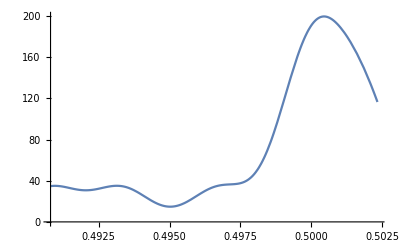

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[data5,.001],x],{x,Min[data5],Max[data5]}]
```

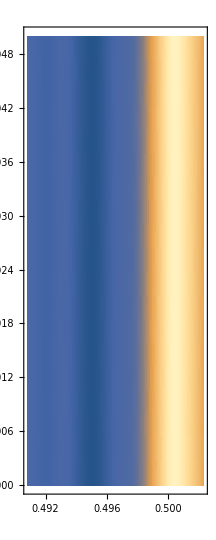

```mathematica
DensityPlot[Evaluate[{PDF[SmoothKernelDistribution[data5,.001],x],0}],{x,Min[data5],Max[data5]},{y,0,.05},AspectRatio->Automatic,PlotPoints->{1000,20}]
```